```mathematica
Comm[A_,B_]=A.B-B.A
Comm[PauliMatrix[1],PauliMatrix[2]]
```

A.B-B.A

{{2 ⅈ,0},{0,-2 ⅈ}}

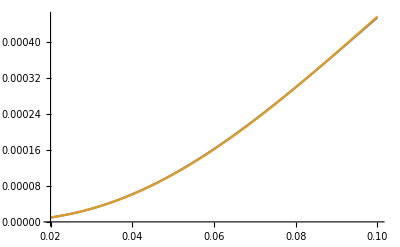

```mathematica
Clear["Global`*"]
A0[κ_,ω_]:={{0,-2I ω,0},{-2I ω,-2κ,0},{0,0,-2κ}}
A1t[t_,κ_,ω_,θ_]:=((ω θ)/(2π)){{0,0,-2Sin[2ω t]},{0,0,-2I Cos[2ω t]},{2Sin[2ω t],-2I Cos[2ω t],0}}

X3noIntegrated[t_,tp_,κ_,ω_,θ_]:=1/(32 π^3 κ^3 (κ^2-4 ω^2)^(3/2))ⅇ^(-2 t κ+tp κ-tp √(κ^2-4 ω^2)) θ^3 ω^2 (Sin[2 tp ω] (-2 ω (κ^2-4 ω^2) (-((-1+ⅇ^(2 tp √(κ^2-4 ω^2))) κ^2)+16 (-1+ⅇ^(2 tp √(κ^2-4 ω^2))) ω^2+2 (1+ⅇ^(2 tp √(κ^2-4 ω^2))) κ √(κ^2-4 ω^2)) Cos[4 tp ω]-(1+ⅇ^(2 tp √(κ^2-4 ω^2))) √(κ^2-4 ω^2) (4 κ^3 (-1+tp κ) ω+16 κ (1-2 tp κ) ω^3-(κ^4+12 κ^2 ω^2-64 ω^4) Sin[4 tp ω])+(-1+ⅇ^(2 tp √(κ^2-4 ω^2))) (-2 κ^4 (1+2 tp κ) ω+8 κ^2 (-5+2 tp κ) ω^3+128 ω^5+κ (κ^4-12 κ^2 ω^2+32 ω^4) Sin[4 tp ω]))+2 ⅇ^(tp √(κ^2-4 ω^2)) Cos[2 tp ω] (√(κ^2-4 ω^2) Cosh[tp √(κ^2-4 ω^2)] (-κ^4-4 κ^2 (3+2 tp κ) ω^2+64 ω^4+(κ^2-4 ω^2) ((κ^2+16 ω^2) Cos[4 tp ω]-4 κ ω Sin[4 tp ω]))+(κ^5+4 κ^3 (3+4 tp κ) ω^2-32 κ (1+2 tp κ) ω^4-(κ^2-4 ω^2) (κ (κ^2-8 ω^2) Cos[4 tp ω]+2 ω (κ^2-16 ω^2) Sin[4 tp ω])) Sinh[tp √(κ^2-4 ω^2)]))
x3NumericIntegrated[κ_,ω_,θ_]:=Re[NIntegrate[X3noIntegrated[2π/ω,tp,κ,ω,θ],{tp,0,2π/ω}]]
X3noIntegratedapprox[t_,tp_,κ_,ω_,θ_]:=1/(32 π^3 κ^3 (κ^2-4 ω^2)^(3/2))ⅇ^(-2 t κ+tp κ-tp √(κ^2-4 ω^2)) θ^3 ω^2 (2 κ^3 ω (-((-1+ⅇ^(2 tp √(κ^2-4 ω^2))) κ (1+2 tp κ))-2 (1+ⅇ^(2 tp √(κ^2-4 ω^2))) (-1+tp κ) √(κ^2-4 ω^2)) Sin[2 tp ω]+2 ⅇ^(tp √(κ^2-4 ω^2)) Cos[2 tp ω] (√(κ^2-4 ω^2) Cosh[tp √(κ^2-4 ω^2)] (-κ^4-4 κ^2 (3+2 tp κ) ω^2+(κ^2-4 ω^2) ((κ^2+16 ω^2) Cos[4 tp ω]-4 κ ω Sin[4 tp ω]))+κ (κ^4+4 κ^2 (3+4 tp κ) ω^2-32 (1+2 tp κ) ω^4-κ^4 Cos[4 tp ω]) Sinh[tp √(κ^2-4 ω^2)]))
X3NumericIntegratedapprox[κ_,ω_,θ_]:=Re[NIntegrate[X3noIntegratedapprox[2π/ω,tp,κ,ω,θ],{tp,0,2π/ω}]]
Plot[{x3NumericIntegrated[1,ω,π],X3NumericIntegratedapprox[1,ω,π]},{ω,0.02,0.1}]
```

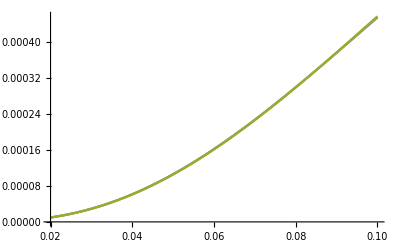

```mathematica
(*Integrate[X3noIntegratedapprox[t,tp,κ,ω,θ],{tp,0,t}]*)
Clear[X3IntegratedApprox]
X3IntegratedApprox[t_,κ_,ω_,θ_]:=1/(32 π^3 κ^3 (κ^2-4 ω^2)^(3/2))θ^3 ω^2 (-1/(4 (9 κ^3 ω+64 κ ω^3))ⅇ^(-2 t κ) (-ω (9 κ^2+64 ω^2) (34 κ^4 √(κ^2-4 ω^2)-56 κ^2 ω^2 √(κ^2-4 ω^2)+128 ω^4 √(κ^2-4 ω^2))+κ ω (14 κ^5 √(κ^2-4 ω^2)+264 κ^3 ω^2 √(κ^2-4 ω^2)-1408 κ ω^4 √(κ^2-4 ω^2)))+1/(4 (9 κ^3 ω+64 κ ω^3))ⅇ^(-t κ-t √(κ^2-4 ω^2)) (-ω (9 κ^2+64 ω^2) (-17 (-1+ⅇ^(2 t √(κ^2-4 ω^2))) κ^5-32 (-1+ⅇ^(2 t √(κ^2-4 ω^2))) κ ω^4+64 (1+ⅇ^(2 t √(κ^2-4 ω^2))) ω^4 √(κ^2-4 ω^2)-4 κ^2 ω^2 (-32 (-1+ⅇ^(2 t √(κ^2-4 ω^2))) t ω^2+7 (1+ⅇ^(2 t √(κ^2-4 ω^2))) √(κ^2-4 ω^2))+κ^4 (-48 (-1+ⅇ^(2 t √(κ^2-4 ω^2))) t ω^2+17 (1+ⅇ^(2 t √(κ^2-4 ω^2))) √(κ^2-4 ω^2))+8 κ^3 ω^2 (-9+2 t √(κ^2-4 ω^2)+ⅇ^(2 t √(κ^2-4 ω^2)) (9+2 t √(κ^2-4 ω^2)))) Cos[2 t ω]+κ ω (-7 (-1+ⅇ^(2 t √(κ^2-4 ω^2))) κ^6+80 (-1+ⅇ^(2 t √(κ^2-4 ω^2))) κ^4 ω^2-544 (-1+ⅇ^(2 t √(κ^2-4 ω^2))) κ^2 ω^4+1024 (-1+ⅇ^(2 t √(κ^2-4 ω^2))) ω^6+7 (1+ⅇ^(2 t √(κ^2-4 ω^2))) κ^5 √(κ^2-4 ω^2)+132 (1+ⅇ^(2 t √(κ^2-4 ω^2))) κ^3 ω^2 √(κ^2-4 ω^2)-704 (1+ⅇ^(2 t √(κ^2-4 ω^2))) κ ω^4 √(κ^2-4 ω^2)) Cos[6 t ω]+2 (3 (-1+ⅇ^(2 t √(κ^2-4 ω^2))) κ^8-4096 (-1+ⅇ^(2 t √(κ^2-4 ω^2))) ω^8-2304 (1+ⅇ^(2 t √(κ^2-4 ω^2))) κ ω^6 √(κ^2-4 ω^2)-3 κ^7 (-24 (-1+ⅇ^(2 t √(κ^2-4 ω^2))) t ω^2+(1+ⅇ^(2 t √(κ^2-4 ω^2))) √(κ^2-4 ω^2))+20 κ^5 ω^2 (4 (-1+ⅇ^(2 t √(κ^2-4 ω^2))) t ω^2+3 (1+ⅇ^(2 t √(κ^2-4 ω^2))) √(κ^2-4 ω^2))+16 κ^3 ω^4 (-192 (-1+ⅇ^(2 t √(κ^2-4 ω^2))) t ω^2+31 (1+ⅇ^(2 t √(κ^2-4 ω^2))) √(κ^2-4 ω^2))-48 κ^6 ω^2 (-1+3 t √(κ^2-4 ω^2)+ⅇ^(2 t √(κ^2-4 ω^2)) (1+3 t √(κ^2-4 ω^2)))+128 κ^2 ω^6 (-11+16 t √(κ^2-4 ω^2)+ⅇ^(2 t √(κ^2-4 ω^2)) (11+16 t √(κ^2-4 ω^2)))-8 κ^4 ω^4 (11+92 t √(κ^2-4 ω^2)+ⅇ^(2 t √(κ^2-4 ω^2)) (-11+92 t √(κ^2-4 ω^2)))+κ (-3 (-1+ⅇ^(2 t √(κ^2-4 ω^2))) κ^7-52 (-1+ⅇ^(2 t √(κ^2-4 ω^2))) κ^5 ω^2+296 (-1+ⅇ^(2 t √(κ^2-4 ω^2))) κ^3 ω^4-640 (-1+ⅇ^(2 t √(κ^2-4 ω^2))) κ ω^6+3 (1+ⅇ^(2 t √(κ^2-4 ω^2))) κ^6 √(κ^2-4 ω^2)+22 (1+ⅇ^(2 t √(κ^2-4 ω^2))) κ^4 ω^2 √(κ^2-4 ω^2)+272 (1+ⅇ^(2 t √(κ^2-4 ω^2))) κ^2 ω^4 √(κ^2-4 ω^2)-1536 (1+ⅇ^(2 t √(κ^2-4 ω^2))) ω^6 √(κ^2-4 ω^2)) Cos[4 t ω]) Sin[2 t ω]))
Plot[{x3NumericIntegrated[1,ω,π],X3NumericIntegratedapprox[1,ω,π],X3IntegratedApprox[(2π)/ω,1,ω,π]},{ω,0.02,0.1}]
```

Now for x4

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tp near {tp} = {372.986}. NIntegrate obtained 0.0000351822+0. ⅈ and 4.66568×10^-8 for the integral and error estimates.

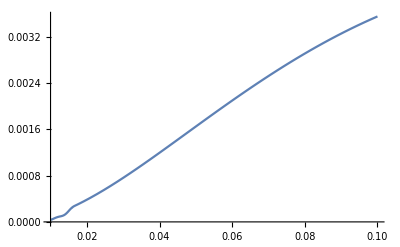

```mathematica
x4NumeIntegratedOnω[κ_,ω_,θ_]:=NIntegrate[(MatrixExp[A0[κ,ω]*((2π)/ω-tp)].A1t[tp,κ,ω,θ].{0,0,X3IntegratedApprox[tp,κ,ω,θ]})[[1]],{tp,0,(2π)/ω}]
Plot[x4NumeIntegratedOnω[1,ω,π],{ω,0.01,0.1}]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tp near {tp} = {372.681}. NIntegrate obtained 0.0000352788+0. ⅈ and 5.78032×10^-8 for the integral and error estimates.

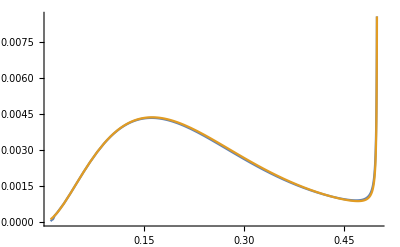

```mathematica
X3IntegratedApp2[t_,κ_,ω_,θ_]:=1/(64 π^3 κ^3 (κ^2-4 ω^2)^(3/2) (9 κ^2+64 ω^2))ⅇ^(-t κ) θ^3 ω (√(κ^2-4 ω^2) Cosh[t √(κ^2-4 ω^2)] (-κ ω (9 κ^2+64 ω^2) (17 κ^2+4 (-7+4 t κ) ω^2) Cos[2 t ω]+(-9 κ^6+2 κ^4 (49-144 t κ) ω^2+16 κ^2 (45-92 t κ) ω^4+512 (-9+8 t κ) ω^6) Sin[2 t ω]+κ^2 (3 κ^4+22 κ^2 ω^2) Sin[6 t ω])+(ω (9 κ^2+64 ω^2) (17 κ^4+24 κ^2 (-3+2 t κ) ω^2+32 (1-4 t κ) ω^4) Cos[2 t ω]+κ (9 κ^6+4 κ^4 (-11+36 t κ) ω^2+40 κ^2 (-3+4 t κ) ω^4+384 (9-16 t κ) ω^6) Sin[2 t ω]-κ (3 κ^6+52 κ^4 ω^2) Sin[6 t ω]) Sinh[t √(κ^2-4 ω^2)])

x4NumeIntegratedOnωApp2[κ_,ω_,θ_]:=NIntegrate[(MatrixExp[A0[κ,ω]*((2π)/ω-tp)].A1t[tp,κ,ω,θ].{0,0,X3IntegratedApp2[tp,κ,ω,θ]})[[1]],{tp,0,(2π)/ω}]
Plot[{x4NumeIntegratedOnω[1,ω,π],x4NumeIntegratedOnωApp2[1,ω,π]},{ω,0.01,0.5}]
```

```mathematica
FullSimplify[1/(32 π^3 κ^3 (κ^2-4 ω^2)^(3/2))θ^3 ω^2 (1/(4 (9 κ^3 ω+64 κ ω^3))ⅇ^(-t κ-t √(κ^2-4 ω^2)) (-ω (9 κ^2+64 ω^2) (-17 (-1+ⅇ^(2 t √(κ^2-4 ω^2))) κ^5-32 (-1+ⅇ^(2 t √(κ^2-4 ω^2))) κ ω^4-4 κ^2 ω^2 (-32 (-1+ⅇ^(2 t √(κ^2-4 ω^2))) t ω^2+7 (1+ⅇ^(2 t √(κ^2-4 ω^2))) √(κ^2-4 ω^2))+κ^4 (-48 (-1+ⅇ^(2 t √(κ^2-4 ω^2))) t ω^2+17 (1+ⅇ^(2 t √(κ^2-4 ω^2))) √(κ^2-4 ω^2))+8 κ^3 ω^2 (-9+2 t √(κ^2-4 ω^2)+ⅇ^(2 t √(κ^2-4 ω^2)) (9+2 t √(κ^2-4 ω^2)))) Cos[2 t ω]+2 (3 (-1+ⅇ^(2 t √(κ^2-4 ω^2))) κ^8-2304 (1+ⅇ^(2 t √(κ^2-4 ω^2))) κ ω^6 √(κ^2-4 ω^2)-3 κ^7 (-24 (-1+ⅇ^(2 t √(κ^2-4 ω^2))) t ω^2+(1+ⅇ^(2 t √(κ^2-4 ω^2))) √(κ^2-4 ω^2))+20 κ^5 ω^2 (4 (-1+ⅇ^(2 t √(κ^2-4 ω^2))) t ω^2+3 (1+ⅇ^(2 t √(κ^2-4 ω^2))) √(κ^2-4 ω^2))+16 κ^3 ω^4 (-192 (-1+ⅇ^(2 t √(κ^2-4 ω^2))) t ω^2+31 (1+ⅇ^(2 t √(κ^2-4 ω^2))) √(κ^2-4 ω^2))-48 κ^6 ω^2 (-1+3 t √(κ^2-4 ω^2)+ⅇ^(2 t √(κ^2-4 ω^2)) (1+3 t √(κ^2-4 ω^2)))+128 κ^2 ω^6 (-11+16 t √(κ^2-4 ω^2)+ⅇ^(2 t √(κ^2-4 ω^2)) (11+16 t √(κ^2-4 ω^2)))-8 κ^4 ω^4 (11+92 t √(κ^2-4 ω^2)+ⅇ^(2 t √(κ^2-4 ω^2)) (-11+92 t √(κ^2-4 ω^2)))+κ (-3 (-1+ⅇ^(2 t √(κ^2-4 ω^2))) κ^7-52 (-1+ⅇ^(2 t √(κ^2-4 ω^2))) κ^5 ω^2+296 (-1+ⅇ^(2 t √(κ^2-4 ω^2))) κ^3 ω^4-640 (-1+ⅇ^(2 t √(κ^2-4 ω^2))) κ ω^6+3 (1+ⅇ^(2 t √(κ^2-4 ω^2))) κ^6 √(κ^2-4 ω^2)+22 (1+ⅇ^(2 t √(κ^2-4 ω^2))) κ^4 ω^2 √(κ^2-4 ω^2)+272 (1+ⅇ^(2 t √(κ^2-4 ω^2))) κ^2 ω^4 √(κ^2-4 ω^2)) Cos[4 t ω]) Sin[2 t ω]))
]
```

1/(64 π^3 κ^3 (κ^2-4 ω^2)^(3/2) (9 κ^2+64 ω^2))ⅇ^(-t κ) θ^3 ω (√(κ^2-4 ω^2) Cosh[t √(κ^2-4 ω^2)] (-κ ω (9 κ^2+64 ω^2) (17 κ^2+4 (-7+4 t κ) ω^2) Cos[2 t ω]+(-9 κ^6+2 κ^4 (49-144 t κ) ω^2+16 κ^2 (45-92 t κ) ω^4+512 (-9+8 t κ) ω^6) Sin[2 t ω]+κ^2 (3 κ^4+22 κ^2 ω^2+272 ω^4) Sin[6 t ω])+(ω (9 κ^2+64 ω^2) (17 κ^4+24 κ^2 (-3+2 t κ) ω^2+32 (1-4 t κ) ω^4) Cos[2 t ω]+κ (9 κ^6+4 κ^4 (-11+36 t κ) ω^2+40 κ^2 (-3+4 t κ) ω^4+384 (9-16 t κ) ω^6) Sin[2 t ω]-κ (3 κ^6+52 κ^4 ω^2-296 κ^2 ω^4+640 ω^6) Sin[6 t ω]) Sinh[t √(κ^2-4 ω^2)])

```mathematica
Integrate[(MatrixExp[A0[κ,ω]*((2π)/ω-tp)].A1t[tp,κ,ω,θ].{0,0,X3IntegratedApp2[tp,κ,ω,θ]})[[1]],{tp,0,(2π)/ω}]
```

1/(64 π^4 κ^5 (κ^2-4 ω^2)^(5/2) (κ^2+12 ω^2) (9 κ^2+64 ω^2))ⅇ^(-(2 π (κ+√(κ^2-4 ω^2)))/ω) θ^4 ω^2 ((-1+ⅇ^((4 π √(κ^2-4 ω^2))/ω)) ω^2 (153 κ^10+2408 κ^8 ω^2+992 κ^6 ω^4-66560 κ^4 ω^6+32000 κ^2 ω^8+319488 ω^10)+4 π^2 κ^3 (9 κ^6+136 κ^4 ω^2+80 κ^2 ω^4-3072 ω^6) ((-1+ⅇ^((4 π √(κ^2-4 ω^2))/ω)) κ^3+4 (-1+ⅇ^((4 π √(κ^2-4 ω^2))/ω)) κ ω^2+(1+ⅇ^((4 π √(κ^2-4 ω^2))/ω)) κ^2 √(κ^2-4 ω^2)-8 (1+ⅇ^((4 π √(κ^2-4 ω^2))/ω)) ω^2 √(κ^2-4 ω^2))-π κ ω (κ^2+12 ω^2) (-45 (-1+ⅇ^((4 π √(κ^2-4 ω^2))/ω)) κ^8-680 (-1+ⅇ^((4 π √(κ^2-4 ω^2))/ω)) κ^6 ω^2+80 (-1+ⅇ^((4 π √(κ^2-4 ω^2))/ω)) κ^4 ω^4+21632 (-1+ⅇ^((4 π √(κ^2-4 ω^2))/ω)) κ^2 ω^6-32768 (-1+ⅇ^((4 π √(κ^2-4 ω^2))/ω)) ω^8+63 (1+ⅇ^((4 π √(κ^2-4 ω^2))/ω)) κ^7 √(κ^2-4 ω^2)+664 (1+ⅇ^((4 π √(κ^2-4 ω^2))/ω)) κ^5 ω^2 √(κ^2-4 ω^2)-288 (1+ⅇ^((4 π √(κ^2-4 ω^2))/ω)) κ^3 ω^4 √(κ^2-4 ω^2)-6656 (1+ⅇ^((4 π √(κ^2-4 ω^2))/ω)) κ ω^6 √(κ^2-4 ω^2)))

```mathematica
FullSimplify[1/(64 π^4 κ^5 (κ^2-4 ω^2)^(5/2) (κ^2+12 ω^2) (9 κ^2+64 ω^2))ⅇ^(-(2 π (κ+√(κ^2-4 ω^2)))/ω) θ^4 ω^2 ((-1+ⅇ^((4 π √(κ^2-4 ω^2))/ω)) ω^2 (153 κ^10+2408 κ^8 ω^2+992 κ^6 ω^4-66560 κ^4 ω^6+32000 κ^2 ω^8+319488 ω^10)+4 π^2 κ^3 (9 κ^6+136 κ^4 ω^2+80 κ^2 ω^4-3072 ω^6) ((-1+ⅇ^((4 π √(κ^2-4 ω^2))/ω)) κ^3+4 (-1+ⅇ^((4 π √(κ^2-4 ω^2))/ω)) κ ω^2+(1+ⅇ^((4 π √(κ^2-4 ω^2))/ω)) κ^2 √(κ^2-4 ω^2)-8 (1+ⅇ^((4 π √(κ^2-4 ω^2))/ω)) ω^2 √(κ^2-4 ω^2))-π κ ω (κ^2+12 ω^2) (-45 (-1+ⅇ^((4 π √(κ^2-4 ω^2))/ω)) κ^8-680 (-1+ⅇ^((4 π √(κ^2-4 ω^2))/ω)) κ^6 ω^2+80 (-1+ⅇ^((4 π √(κ^2-4 ω^2))/ω)) κ^4 ω^4+21632 (-1+ⅇ^((4 π √(κ^2-4 ω^2))/ω)) κ^2 ω^6-32768 (-1+ⅇ^((4 π √(κ^2-4 ω^2))/ω)) ω^8+63 (1+ⅇ^((4 π √(κ^2-4 ω^2))/ω)) κ^7 √(κ^2-4 ω^2)+664 (1+ⅇ^((4 π √(κ^2-4 ω^2))/ω)) κ^5 ω^2 √(κ^2-4 ω^2)-288 (1+ⅇ^((4 π √(κ^2-4 ω^2))/ω)) κ^3 ω^4 √(κ^2-4 ω^2)-6656 (1+ⅇ^((4 π √(κ^2-4 ω^2))/ω)) κ ω^6 √(κ^2-4 ω^2)))]
```

1/(64 π^4 κ^5 (κ^2-4 ω^2)^(5/2) (κ^2+12 ω^2) (9 κ^2+64 ω^2))ⅇ^(-(2 π (κ+√(κ^2-4 ω^2)))/ω) θ^4 ω^2 ((1+ⅇ^((4 π √(κ^2-4 ω^2))/ω)) π κ^2 √(κ^2-4 ω^2) (κ^2+12 ω^2) (-63 κ^6 ω-664 κ^4 ω^3+288 κ^2 ω^5+6656 ω^7+4 π κ (κ-2 ω) (κ+2 ω) (κ^2-8 ω^2) (9 κ^2+64 ω^2))+(-1+ⅇ^((4 π √(κ^2-4 ω^2))/ω)) (4 π^2 κ^4 (κ-2 ω) (κ+2 ω) (κ^2+4 ω^2) (κ^2+12 ω^2) (9 κ^2+64 ω^2)+π κ (κ-2 ω) ω (κ+2 ω) (κ^2+12 ω^2) (45 κ^6+860 κ^4 ω^2+3360 κ^2 ω^4-8192 ω^6)+ω^2 (153 κ^10+2408 κ^8 ω^2+992 κ^6 ω^4-66560 κ^4 ω^6+32000 κ^2 ω^8+319488 ω^10)))

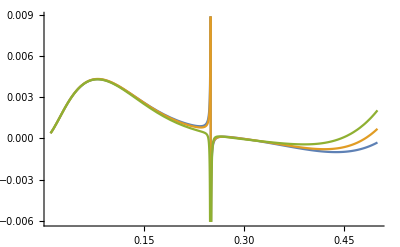

```mathematica
x4IntegratedAnalyt[κ_,ω_,θ_]:=1/(64 π^4 κ^5 (κ^2-4 ω^2)^(5/2) (κ^2+12 ω^2) (9 κ^2+64 ω^2))ⅇ^(-(2 π (κ+√(κ^2-4 ω^2)))/ω) θ^4 ω^2 ((1+ⅇ^((4 π √(κ^2-4 ω^2))/ω)) π κ^2 √(κ^2-4 ω^2) (κ^2+12 ω^2) (-63 κ^6 ω-664 κ^4 ω^3+288 κ^2 ω^5+6656 ω^7+4 π κ (κ-2 ω) (κ+2 ω) (κ^2-8 ω^2) (9 κ^2+64 ω^2))+(-1+ⅇ^((4 π √(κ^2-4 ω^2))/ω)) (4 π^2 κ^4 (κ-2 ω) (κ+2 ω) (κ^2+4 ω^2) (κ^2+12 ω^2) (9 κ^2+64 ω^2)+π κ (κ-2 ω) ω (κ+2 ω) (κ^2+12 ω^2) (45 κ^6+860 κ^4 ω^2)+ω^2 (153 κ^10+2408 κ^8 ω^2+992 κ^6 ω^4-66560 κ^4 ω^6+32000 κ^2 ω^8+319488 ω^10)))
x4IntegratedAnalytApp3[κ_,ω_,θ_]:=1/(64 π^4 κ^5 (κ^2-4 ω^2)^(5/2)  (9 κ^2+64 ω^2))ⅇ^(-(2 π (κ+√(κ^2-4 ω^2)))/ω) θ^4 ω^2 ((1+ⅇ^((4 π √(κ^2-4 ω^2))/ω)) π κ^2 √(κ^2-4 ω^2)  (-63 κ^6 ω-664 κ^4 ω^3+4 π κ (κ-2 ω) (κ+2 ω) (κ^2-8 ω^2) (9 κ^2+64 ω^2))+(-1+ⅇ^((4 π √(κ^2-4 ω^2))/ω)) (4 π^2 κ^4 (κ-2 ω) (κ+2 ω) (κ^2+4 ω^2) (9 κ^2+64 ω^2)+π κ (κ-2 ω) ω (κ+2 ω) (45 κ^6+860 κ^4 ω^2)))

Plot[{x4NumeIntegratedOnω[1/2,ω,π],x4IntegratedAnalyt[1/2,ω,π],x4IntegratedAnalytApp3[1/2,ω,π]},{ω,0.01,0.5}]
(*x4NumeIntegratedOnωApp2[1,ω,π],*)
```

```mathematica
664/7//N
```

94.8571

```mathematica
64*7
```

448

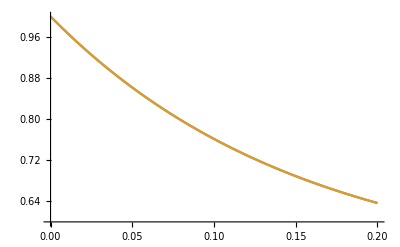

0.745794

```mathematica
Fid[κ_,ω_,θ_]:=1/2(1+(1-(ω θ^2)/(2π κ))Exp[-(4π ω)/κ])
FidCorrect[κ_,ω_,θ_]:=1/2(1+(1-(ω θ^2)/(2π κ))Exp[-(4π ω)/κ])
Plot[{Fid[2,ω,π/2],FidCorrect[2,ω,π/2]},{ω,0,0.2},PlotRange->{0.6,1}]
Fid[2,0.1,π]
```

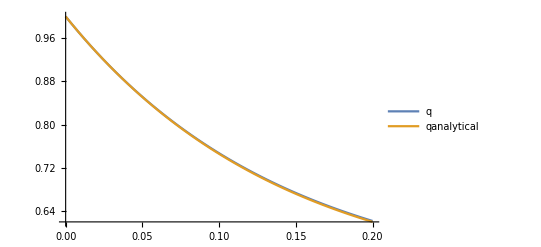

```mathematica
A0[κ_,ω_]:={{0,-2I ω,0},{-2I ω,-2κ,0},{0,0,-2κ}}
A1t[t_,κ_,ω_,θ_]:=((ω θ)/(2π)){{0,0,-2Sin[2ω t]},{0,0,-2I Cos[2ω t]},{2Sin[2ω t],-2I Cos[2ω t],0}}
A[t_,κ_,ω_,θ_]:=A0[κ,ω]+A1t[t,κ,ω,θ]
q[κ_,ω_,θ_]:=Module[{s,g},s=NDSolve[{v'[t]==A[t,κ,ω,θ].v[t],v[0]=={1,0,0}},v,{t,0,(2π)/ω}];
g=Evaluate[v[2π/ω]/.s][[1,1]];
Re[(1+g)/2]]
Fid[κ_,ω_,θ_]:=1/2(1+(1-(ω θ^2)/(2π κ))Exp[-(4π ω)/κ])
qanalyticaluptofourth[κ_,ω_,θ_]:=1/2(1+Exp[-4π ω/κ](1-(ω θ^2)/(κ 2π)+(θ^4 κ ω^2 (9 κ^2+ω^2) (κ^2+12 ω^2))/(8 π^2 (κ^2-4 ω^2)^(5/2) (9 κ^2+172 ω^2)) ))
qanalyticalExact[κ_,ω_,θ_]:=1/2(1+Exp[-4π ω/κ]Exp[-θ^2/(2π)ω/κ])
Plot[{q[2,ω,π],Fid[2,ω,π]},{ω,0,0.2},PlotLegends->{"q","qanalytical"}]
```

## Comenzar desde zero

```mathematica
g={KroneckerProduct[PauliMatrix[3],PauliMatrix[3],IdentityMatrix[2]],KroneckerProduct[PauliMatrix[3],IdentityMatrix[2],PauliMatrix[3]]};
H=KroneckerProduct[PauliMatrix[1],PauliMatrix[1],PauliMatrix[1]];
X=KroneckerProduct[PauliMatrix[1],IdentityMatrix[2],PauliMatrix[3]];
ψ0=Basis[8,1];
θ=π/2;
V[t_]:=MatrixExp[I*(θ*ω*t)/(2π)*H].MatrixExp[I*ω*t*X];
g1[t_]:=V[t].(g[[1]].ConjugateTranspose[V[t]]);
g2[t_]:=V[t].(g[[2]].ConjugateTranspose[V[t]]);
Refine[g1[t],Assumptions->{ω>0,t>0}]//FullSimplify//MatrixForm
Refine[g2[t],Assumptions->{ω>0,t>0}]//FullSimplify//MatrixForm
```

(Cos[2 t ω] | 0 | 0 | -Sin[(t ω)/2] Sin[2 t ω] | -1/2 ⅈ (Sin[(3 t ω)/2]+Sin[(5 t ω)/2]) | 0 | 0 | 0
0 | Cos[2 t ω] | Sin[(t ω)/2] Sin[2 t ω] | 0 | 0 | 1/2 ⅈ (Sin[(3 t ω)/2]+Sin[(5 t ω)/2]) | 0 | 0
0 | Sin[(t ω)/2] Sin[2 t ω] | -Cos[2 t ω] | 0 | 0 | 0 | 1/2 ⅈ (Sin[(3 t ω)/2]+Sin[(5 t ω)/2]) | 0
-Sin[(t ω)/2] Sin[2 t ω] | 0 | 0 | -Cos[2 t ω] | 0 | 0 | 0 | -1/2 ⅈ (Sin[(3 t ω)/2]+Sin[(5 t ω)/2])
1/2 ⅈ (Sin[(3 t ω)/2]+Sin[(5 t ω)/2]) | 0 | 0 | 0 | -Cos[2 t ω] | 0 | 0 | Sin[(t ω)/2] Sin[2 t ω]
0 | -1/2 ⅈ (Sin[(3 t ω)/2]+Sin[(5 t ω)/2]) | 0 | 0 | 0 | -Cos[2 t ω] | -Sin[(t ω)/2] Sin[2 t ω] | 0
0 | 0 | -1/2 ⅈ (Sin[(3 t ω)/2]+Sin[(5 t ω)/2]) | 0 | 0 | -Sin[(t ω)/2] Sin[2 t ω] | Cos[2 t ω] | 0
0 | 0 | 0 | 1/2 ⅈ (Sin[(3 t ω)/2]+Sin[(5 t ω)/2]) | Sin[(t ω)/2] Sin[2 t ω] | 0 | 0 | Cos[2 t ω])

(Cos[2 t ω] | 0 | 0 | -Sin[(t ω)/2] Sin[2 t ω] | -1/2 ⅈ (Sin[(3 t ω)/2]+Sin[(5 t ω)/2]) | 0 | 0 | 0
0 | -Cos[2 t ω] | -Sin[(t ω)/2] Sin[2 t ω] | 0 | 0 | -1/2 ⅈ (Sin[(3 t ω)/2]+Sin[(5 t ω)/2]) | 0 | 0
0 | -Sin[(t ω)/2] Sin[2 t ω] | Cos[2 t ω] | 0 | 0 | 0 | -1/2 ⅈ (Sin[(3 t ω)/2]+Sin[(5 t ω)/2]) | 0
-Sin[(t ω)/2] Sin[2 t ω] | 0 | 0 | -Cos[2 t ω] | 0 | 0 | 0 | -1/2 ⅈ (Sin[(3 t ω)/2]+Sin[(5 t ω)/2])
1/2 ⅈ (Sin[(3 t ω)/2]+Sin[(5 t ω)/2]) | 0 | 0 | 0 | -Cos[2 t ω] | 0 | 0 | Sin[(t ω)/2] Sin[2 t ω]
0 | 1/2 ⅈ (Sin[(3 t ω)/2]+Sin[(5 t ω)/2]) | 0 | 0 | 0 | Cos[2 t ω] | Sin[(t ω)/2] Sin[2 t ω] | 0
0 | 0 | 1/2 ⅈ (Sin[(3 t ω)/2]+Sin[(5 t ω)/2]) | 0 | 0 | Sin[(t ω)/2] Sin[2 t ω] | -Cos[2 t ω] | 0
0 | 0 | 0 | 1/2 ⅈ (Sin[(3 t ω)/2]+Sin[(5 t ω)/2]) | Sin[(t ω)/2] Sin[2 t ω] | 0 | 0 | Cos[2 t ω])

```mathematica
Outer[Times,ψ0,ψ0]//MatrixForm
```

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
Refine[g2[0],Assumptions->{ω>0,t>0}]//FullSimplify//MatrixForm
```

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1)

```mathematica
Table[Subscript[ρ,IntegerDigits[i-1, 2,3],IntegerDigits[j-1, 2,3]],{i,9},{j,8}]//MatrixForm
```

(ρ_({0,0,0},{0,0,0}) | ρ_({0,0,0},{0,0,1}) | ρ_({0,0,0},{0,1,0}) | ρ_({0,0,0},{0,1,1}) | ρ_({0,0,0},{1,0,0}) | ρ_({0,0,0},{1,0,1}) | ρ_({0,0,0},{1,1,0}) | ρ_({0,0,0},{1,1,1})
ρ_({0,0,1},{0,0,0}) | ρ_({0,0,1},{0,0,1}) | ρ_({0,0,1},{0,1,0}) | ρ_({0,0,1},{0,1,1}) | ρ_({0,0,1},{1,0,0}) | ρ_({0,0,1},{1,0,1}) | ρ_({0,0,1},{1,1,0}) | ρ_({0,0,1},{1,1,1})
ρ_({0,1,0},{0,0,0}) | ρ_({0,1,0},{0,0,1}) | ρ_({0,1,0},{0,1,0}) | ρ_({0,1,0},{0,1,1}) | ρ_({0,1,0},{1,0,0}) | ρ_({0,1,0},{1,0,1}) | ρ_({0,1,0},{1,1,0}) | ρ_({0,1,0},{1,1,1})
ρ_({0,1,1},{0,0,0}) | ρ_({0,1,1},{0,0,1}) | ρ_({0,1,1},{0,1,0}) | ρ_({0,1,1},{0,1,1}) | ρ_({0,1,1},{1,0,0}) | ρ_({0,1,1},{1,0,1}) | ρ_({0,1,1},{1,1,0}) | ρ_({0,1,1},{1,1,1})
ρ_({1,0,0},{0,0,0}) | ρ_({1,0,0},{0,0,1}) | ρ_({1,0,0},{0,1,0}) | ρ_({1,0,0},{0,1,1}) | ρ_({1,0,0},{1,0,0}) | ρ_({1,0,0},{1,0,1}) | ρ_({1,0,0},{1,1,0}) | ρ_({1,0,0},{1,1,1})
ρ_({1,0,1},{0,0,0}) | ρ_({1,0,1},{0,0,1}) | ρ_({1,0,1},{0,1,0}) | ρ_({1,0,1},{0,1,1}) | ρ_({1,0,1},{1,0,0}) | ρ_({1,0,1},{1,0,1}) | ρ_({1,0,1},{1,1,0}) | ρ_({1,0,1},{1,1,1})
ρ_({1,1,0},{0,0,0}) | ρ_({1,1,0},{0,0,1}) | ρ_({1,1,0},{0,1,0}) | ρ_({1,1,0},{0,1,1}) | ρ_({1,1,0},{1,0,0}) | ρ_({1,1,0},{1,0,1}) | ρ_({1,1,0},{1,1,0}) | ρ_({1,1,0},{1,1,1})
ρ_({1,1,1},{0,0,0}) | ρ_({1,1,1},{0,0,1}) | ρ_({1,1,1},{0,1,0}) | ρ_({1,1,1},{0,1,1}) | ρ_({1,1,1},{1,0,0}) | ρ_({1,1,1},{1,0,1}) | ρ_({1,1,1},{1,1,0}) | ρ_({1,1,1},{1,1,1})
ρ_({0,0,0},{0,0,0}) | ρ_({0,0,0},{0,0,1}) | ρ_({0,0,0},{0,1,0}) | ρ_({0,0,0},{0,1,1}) | ρ_({0,0,0},{1,0,0}) | ρ_({0,0,0},{1,0,1}) | ρ_({0,0,0},{1,1,0}) | ρ_({0,0,0},{1,1,1}))

```mathematica
(Refine[g1[t],Assumptions->{ω>0,t>0}].Table[Subscript[ρ,IntegerDigits[i-1, 2,3],IntegerDigits[j-1, 2,3]],{i,8},{j,8}].Refine[g1[t],Assumptions->{ω>0,t>0}]+Refine[g2[t],Assumptions->{ω>0,t>0}].Table[Subscript[ρ,IntegerDigits[i-1, 2,3],IntegerDigits[j-1, 2,3]],{i,8},{j,8}].Refine[g2[t],Assumptions->{ω>0,t>0}])//MatrixForm
```

(2 (Cos[(t ω)/4]^2 Cos[t ω]^2+Cos[t ω]^2 Sin[(t ω)/4]^2-Cos[(t ω)/4]^2 Sin[t ω]^2-Sin[(t ω)/4]^2 Sin[t ω]^2) ((Cos[(t ω)/4]^2 Cos[t ω]^2+Cos[t ω]^2 Sin[(t ω)/4]^2-Cos[(t ω)/4]^2 Sin[t ω]^2-Sin[(t ω)/4]^2 Sin[t ω]^2) ρ_({0,0,0},{0,0,0})-4 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] ρ_({0,1,1},{0,0,0})+(-2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]+2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ρ_({1,0,0},{0,0,0}))-8 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] ((Cos[(t ω)/4]^2 Cos[t ω]^2+Cos[t ω]^2 Sin[(t ω)/4]^2-Cos[(t ω)/4]^2 Sin[t ω]^2-Sin[(t ω)/4]^2 Sin[t ω]^2) ρ_({0,0,0},{0,1,1})-4 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] ρ_({0,1,1},{0,1,1})+(-2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]+2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ρ_({1,0,0},{0,1,1}))+2 (2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]-2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ((Cos[(t ω)/4]^2 Cos[t ω]^2+Cos[t ω]^2 Sin[(t ω)/4]^2-Cos[(t ω)/4]^2 Sin[t ω]^2-Sin[(t ω)/4]^2 Sin[t ω]^2) ρ_({0,0,0},{1,0,0})-4 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] ρ_({0,1,1},{1,0,0})+(-2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]+2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ρ_({1,0,0},{1,0,0})) | (Cos[(t ω)/4]^2 Cos[t ω]^2+Cos[t ω]^2 Sin[(t ω)/4]^2-Cos[(t ω)/4]^2 Sin[t ω]^2-Sin[(t ω)/4]^2 Sin[t ω]^2) ((Cos[(t ω)/4]^2 Cos[t ω]^2+Cos[t ω]^2 Sin[(t ω)/4]^2-Cos[(t ω)/4]^2 Sin[t ω]^2-Sin[(t ω)/4]^2 Sin[t ω]^2) ρ_({0,0,0},{0,0,1})-4 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] ρ_({0,1,1},{0,0,1})+(-2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]+2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ρ_({1,0,0},{0,0,1}))+(-Cos[(t ω)/4]^2 Cos[t ω]^2-Cos[t ω]^2 Sin[(t ω)/4]^2+Cos[(t ω)/4]^2 Sin[t ω]^2+Sin[(t ω)/4]^2 Sin[t ω]^2) ((Cos[(t ω)/4]^2 Cos[t ω]^2+Cos[t ω]^2 Sin[(t ω)/4]^2-Cos[(t ω)/4]^2 Sin[t ω]^2-Sin[(t ω)/4]^2 Sin[t ω]^2) ρ_({0,0,0},{0,0,1})-4 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] ρ_({0,1,1},{0,0,1})+(-2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]+2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ρ_({1,0,0},{0,0,1}))+(2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]-2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ((Cos[(t ω)/4]^2 Cos[t ω]^2+Cos[t ω]^2 Sin[(t ω)/4]^2-Cos[(t ω)/4]^2 Sin[t ω]^2-Sin[(t ω)/4]^2 Sin[t ω]^2) ρ_({0,0,0},{1,0,1})-4 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] ρ_({0,1,1},{1,0,1})+(-2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]+2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ρ_({1,0,0},{1,0,1}))+(-2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]+2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ((Cos[(t ω)/4]^2 Cos[t ω]^2+Cos[t ω]^2 Sin[(t ω)/4]^2-Cos[(t ω)/4]^2 Sin[t ω]^2-Sin[(t ω)/4]^2 Sin[t ω]^2) ρ_({0,0,0},{1,0,1})-4 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] ρ_({0,1,1},{1,0,1})+(-2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]+2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ρ_({1,0,0},{1,0,1})) | (Cos[(t ω)/4]^2 Cos[t ω]^2+Cos[t ω]^2 Sin[(t ω)/4]^2-Cos[(t ω)/4]^2 Sin[t ω]^2-Sin[(t ω)/4]^2 Sin[t ω]^2) ((Cos[(t ω)/4]^2 Cos[t ω]^2+Cos[t ω]^2 Sin[(t ω)/4]^2-Cos[(t ω)/4]^2 Sin[t ω]^2-Sin[(t ω)/4]^2 Sin[t ω]^2) ρ_({0,0,0},{0,1,0})-4 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] ρ_({0,1,1},{0,1,0})+(-2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]+2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ρ_({1,0,0},{0,1,0}))+(-Cos[(t ω)/4]^2 Cos[t ω]^2-Cos[t ω]^2 Sin[(t ω)/4]^2+Cos[(t ω)/4]^2 Sin[t ω]^2+Sin[(t ω)/4]^2 Sin[t ω]^2) ((Cos[(t ω)/4]^2 Cos[t ω]^2+Cos[t ω]^2 Sin[(t ω)/4]^2-Cos[(t ω)/4]^2 Sin[t ω]^2-Sin[(t ω)/4]^2 Sin[t ω]^2) ρ_({0,0,0},{0,1,0})-4 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] ρ_({0,1,1},{0,1,0})+(-2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]+2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ρ_({1,0,0},{0,1,0}))+(2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]-2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ((Cos[(t ω)/4]^2 Cos[t ω]^2+Cos[t ω]^2 Sin[(t ω)/4]^2-Cos[(t ω)/4]^2 Sin[t ω]^2-Sin[(t ω)/4]^2 Sin[t ω]^2) ρ_({0,0,0},{1,1,0})-4 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] ρ_({0,1,1},{1,1,0})+(-2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]+2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ρ_({1,0,0},{1,1,0}))+(-2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]+2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ((Cos[(t ω)/4]^2 Cos[t ω]^2+Cos[t ω]^2 Sin[(t ω)/4]^2-Cos[(t ω)/4]^2 Sin[t ω]^2-Sin[(t ω)/4]^2 Sin[t ω]^2) ρ_({0,0,0},{1,1,0})-4 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] ρ_({0,1,1},{1,1,0})+(-2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]+2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ρ_({1,0,0},{1,1,0})) | -8 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] ((Cos[(t ω)/4]^2 Cos[t ω]^2+Cos[t ω]^2 Sin[(t ω)/4]^2-Cos[(t ω)/4]^2 Sin[t ω]^2-Sin[(t ω)/4]^2 Sin[t ω]^2) ρ_({0,0,0},{0,0,0})-4 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] ρ_({0,1,1},{0,0,0})+(-2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]+2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ρ_({1,0,0},{0,0,0}))+2 (-Cos[(t ω)/4]^2 Cos[t ω]^2-Cos[t ω]^2 Sin[(t ω)/4]^2+Cos[(t ω)/4]^2 Sin[t ω]^2+Sin[(t ω)/4]^2 Sin[t ω]^2) ((Cos[(t ω)/4]^2 Cos[t ω]^2+Cos[t ω]^2 Sin[(t ω)/4]^2-Cos[(t ω)/4]^2 Sin[t ω]^2-Sin[(t ω)/4]^2 Sin[t ω]^2) ρ_({0,0,0},{0,1,1})-4 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] ρ_({0,1,1},{0,1,1})+(-2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]+2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ρ_({1,0,0},{0,1,1}))+2 (2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]-2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ((Cos[(t ω)/4]^2 Cos[t ω]^2+Cos[t ω]^2 Sin[(t ω)/4]^2-Cos[(t ω)/4]^2 Sin[t ω]^2-Sin[(t ω)/4]^2 Sin[t ω]^2) ρ_({0,0,0},{1,1,1})-4 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] ρ_({0,1,1},{1,1,1})+(-2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]+2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ρ_({1,0,0},{1,1,1})) | 2 (-2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]+2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ((Cos[(t ω)/4]^2 Cos[t ω]^2+Cos[t ω]^2 Sin[(t ω)/4]^2-Cos[(t ω)/4]^2 Sin[t ω]^2-Sin[(t ω)/4]^2 Sin[t ω]^2) ρ_({0,0,0},{0,0,0})-4 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] ρ_({0,1,1},{0,0,0})+(-2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]+2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ρ_({1,0,0},{0,0,0}))+2 (-Cos[(t ω)/4]^2 Cos[t ω]^2-Cos[t ω]^2 Sin[(t ω)/4]^2+Cos[(t ω)/4]^2 Sin[t ω]^2+Sin[(t ω)/4]^2 Sin[t ω]^2) ((Cos[(t ω)/4]^2 Cos[t ω]^2+Cos[t ω]^2 Sin[(t ω)/4]^2-Cos[(t ω)/4]^2 Sin[t ω]^2-Sin[(t ω)/4]^2 Sin[t ω]^2) ρ_({0,0,0},{1,0,0})-4 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] ρ_({0,1,1},{1,0,0})+(-2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]+2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ρ_({1,0,0},{1,0,0}))+8 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] ((Cos[(t ω)/4]^2 Cos[t ω]^2+Cos[t ω]^2 Sin[(t ω)/4]^2-Cos[(t ω)/4]^2 Sin[t ω]^2-Sin[(t ω)/4]^2 Sin[t ω]^2) ρ_({0,0,0},{1,1,1})-4 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] ρ_({0,1,1},{1,1,1})+(-2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]+2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ρ_({1,0,0},{1,1,1})) | (2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]-2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ((Cos[(t ω)/4]^2 Cos[t ω]^2+Cos[t ω]^2 Sin[(t ω)/4]^2-Cos[(t ω)/4]^2 Sin[t ω]^2-Sin[(t ω)/4]^2 Sin[t ω]^2) ρ_({0,0,0},{0,0,1})-4 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] ρ_({0,1,1},{0,0,1})+(-2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]+2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ρ_({1,0,0},{0,0,1}))+(-2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]+2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ((Cos[(t ω)/4]^2 Cos[t ω]^2+Cos[t ω]^2 Sin[(t ω)/4]^2-Cos[(t ω)/4]^2 Sin[t ω]^2-Sin[(t ω)/4]^2 Sin[t ω]^2) ρ_({0,0,0},{0,0,1})-4 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] ρ_({0,1,1},{0,0,1})+(-2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]+2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ρ_({1,0,0},{0,0,1}))+(Cos[(t ω)/4]^2 Cos[t ω]^2+Cos[t ω]^2 Sin[(t ω)/4]^2-Cos[(t ω)/4]^2 Sin[t ω]^2-Sin[(t ω)/4]^2 Sin[t ω]^2) ((Cos[(t ω)/4]^2 Cos[t ω]^2+Cos[t ω]^2 Sin[(t ω)/4]^2-Cos[(t ω)/4]^2 Sin[t ω]^2-Sin[(t ω)/4]^2 Sin[t ω]^2) ρ_({0,0,0},{1,0,1})-4 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] ρ_({0,1,1},{1,0,1})+(-2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]+2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ρ_({1,0,0},{1,0,1}))+(-Cos[(t ω)/4]^2 Cos[t ω]^2-Cos[t ω]^2 Sin[(t ω)/4]^2+Cos[(t ω)/4]^2 Sin[t ω]^2+Sin[(t ω)/4]^2 Sin[t ω]^2) ((Cos[(t ω)/4]^2 Cos[t ω]^2+Cos[t ω]^2 Sin[(t ω)/4]^2-Cos[(t ω)/4]^2 Sin[t ω]^2-Sin[(t ω)/4]^2 Sin[t ω]^2) ρ_({0,0,0},{1,0,1})-4 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] ρ_({0,1,1},{1,0,1})+(-2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]+2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ρ_({1,0,0},{1,0,1})) | (2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]-2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ((Cos[(t ω)/4]^2 Cos[t ω]^2+Cos[t ω]^2 Sin[(t ω)/4]^2-Cos[(t ω)/4]^2 Sin[t ω]^2-Sin[(t ω)/4]^2 Sin[t ω]^2) ρ_({0,0,0},{0,1,0})-4 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] ρ_({0,1,1},{0,1,0})+(-2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]+2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ρ_({1,0,0},{0,1,0}))+(-2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]+2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ((Cos[(t ω)/4]^2 Cos[t ω]^2+Cos[t ω]^2 Sin[(t ω)/4]^2-Cos[(t ω)/4]^2 Sin[t ω]^2-Sin[(t ω)/4]^2 Sin[t ω]^2) ρ_({0,0,0},{0,1,0})-4 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] ρ_({0,1,1},{0,1,0})+(-2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]+2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ρ_({1,0,0},{0,1,0}))+(Cos[(t ω)/4]^2 Cos[t ω]^2+Cos[t ω]^2 Sin[(t ω)/4]^2-Cos[(t ω)/4]^2 Sin[t ω]^2-Sin[(t ω)/4]^2 Sin[t ω]^2) ((Cos[(t ω)/4]^2 Cos[t ω]^2+Cos[t ω]^2 Sin[(t ω)/4]^2-Cos[(t ω)/4]^2 Sin[t ω]^2-Sin[(t ω)/4]^2 Sin[t ω]^2) ρ_({0,0,0},{1,1,0})-4 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] ρ_({0,1,1},{1,1,0})+(-2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]+2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ρ_({1,0,0},{1,1,0}))+(-Cos[(t ω)/4]^2 Cos[t ω]^2-Cos[t ω]^2 Sin[(t ω)/4]^2+Cos[(t ω)/4]^2 Sin[t ω]^2+Sin[(t ω)/4]^2 Sin[t ω]^2) ((Cos[(t ω)/4]^2 Cos[t ω]^2+Cos[t ω]^2 Sin[(t ω)/4]^2-Cos[(t ω)/4]^2 Sin[t ω]^2-Sin[(t ω)/4]^2 Sin[t ω]^2) ρ_({0,0,0},{1,1,0})-4 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] ρ_({0,1,1},{1,1,0})+(-2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]+2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ρ_({1,0,0},{1,1,0})) | 2 (-2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]+2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ((Cos[(t ω)/4]^2 Cos[t ω]^2+Cos[t ω]^2 Sin[(t ω)/4]^2-Cos[(t ω)/4]^2 Sin[t ω]^2-Sin[(t ω)/4]^2 Sin[t ω]^2) ρ_({0,0,0},{0,1,1})-4 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] ρ_({0,1,1},{0,1,1})+(-2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]+2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ρ_({1,0,0},{0,1,1}))+8 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] ((Cos[(t ω)/4]^2 Cos[t ω]^2+Cos[t ω]^2 Sin[(t ω)/4]^2-Cos[(t ω)/4]^2 Sin[t ω]^2-Sin[(t ω)/4]^2 Sin[t ω]^2) ρ_({0,0,0},{1,0,0})-4 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] ρ_({0,1,1},{1,0,0})+(-2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]+2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ρ_({1,0,0},{1,0,0}))+2 (Cos[(t ω)/4]^2 Cos[t ω]^2+Cos[t ω]^2 Sin[(t ω)/4]^2-Cos[(t ω)/4]^2 Sin[t ω]^2-Sin[(t ω)/4]^2 Sin[t ω]^2) ((Cos[(t ω)/4]^2 Cos[t ω]^2+Cos[t ω]^2 Sin[(t ω)/4]^2-Cos[(t ω)/4]^2 Sin[t ω]^2-Sin[(t ω)/4]^2 Sin[t ω]^2) ρ_({0,0,0},{1,1,1})-4 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] ρ_({0,1,1},{1,1,1})+(-2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]+2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ρ_({1,0,0},{1,1,1}))
(Cos[(t ω)/4]^2 Cos[t ω]^2+Cos[t ω]^2 Sin[(t ω)/4]^2-Cos[(t ω)/4]^2 Sin[t ω]^2-Sin[(t ω)/4]^2 Sin[t ω]^2) ((Cos[(t ω)/4]^2 Cos[t ω]^2+Cos[t ω]^2 Sin[(t ω)/4]^2-Cos[(t ω)/4]^2 Sin[t ω]^2-Sin[(t ω)/4]^2 Sin[t ω]^2) ρ_({0,0,1},{0,0,0})+4 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] ρ_({0,1,0},{0,0,0})+(2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]-2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ρ_({1,0,1},{0,0,0}))+(Cos[(t ω)/4]^2 Cos[t ω]^2+Cos[t ω]^2 Sin[(t ω)/4]^2-Cos[(t ω)/4]^2 Sin[t ω]^2-Sin[(t ω)/4]^2 Sin[t ω]^2) ((-Cos[(t ω)/4]^2 Cos[t ω]^2-Cos[t ω]^2 Sin[(t ω)/4]^2+Cos[(t ω)/4]^2 Sin[t ω]^2+Sin[(t ω)/4]^2 Sin[t ω]^2) ρ_({0,0,1},{0,0,0})-4 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] ρ_({0,1,0},{0,0,0})+(-2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]+2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ρ_({1,0,1},{0,0,0}))-4 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] ((Cos[(t ω)/4]^2 Cos[t ω]^2+Cos[t ω]^2 Sin[(t ω)/4]^2-Cos[(t ω)/4]^2 Sin[t ω]^2-Sin[(t ω)/4]^2 Sin[t ω]^2) ρ_({0,0,1},{0,1,1})+4 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] ρ_({0,1,0},{0,1,1})+(2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]-2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ρ_({1,0,1},{0,1,1}))-4 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] ((-Cos[(t ω)/4]^2 Cos[t ω]^2-Cos[t ω]^2 Sin[(t ω)/4]^2+Cos[(t ω)/4]^2 Sin[t ω]^2+Sin[(t ω)/4]^2 Sin[t ω]^2) ρ_({0,0,1},{0,1,1})-4 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] ρ_({0,1,0},{0,1,1})+(-2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]+2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ρ_({1,0,1},{0,1,1}))+(2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]-2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ((Cos[(t ω)/4]^2 Cos[t ω]^2+Cos[t ω]^2 Sin[(t ω)/4]^2-Cos[(t ω)/4]^2 Sin[t ω]^2-Sin[(t ω)/4]^2 Sin[t ω]^2) ρ_({0,0,1},{1,0,0})+4 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] ρ_({0,1,0},{1,0,0})+(2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]-2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ρ_({1,0,1},{1,0,0}))+(2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]-2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ((-Cos[(t ω)/4]^2 Cos[t ω]^2-Cos[t ω]^2 Sin[(t ω)/4]^2+Cos[(t ω)/4]^2 Sin[t ω]^2+Sin[(t ω)/4]^2 Sin[t ω]^2) ρ_({0,0,1},{1,0,0})-4 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] ρ_({0,1,0},{1,0,0})+(-2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]+2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ρ_({1,0,1},{1,0,0})) | (Cos[(t ω)/4]^2 Cos[t ω]^2+Cos[t ω]^2 Sin[(t ω)/4]^2-Cos[(t ω)/4]^2 Sin[t ω]^2-Sin[(t ω)/4]^2 Sin[t ω]^2) ((Cos[(t ω)/4]^2 Cos[t ω]^2+Cos[t ω]^2 Sin[(t ω)/4]^2-Cos[(t ω)/4]^2 Sin[t ω]^2-Sin[(t ω)/4]^2 Sin[t ω]^2) ρ_({0,0,1},{0,0,1})+4 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] ρ_({0,1,0},{0,0,1})+(2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]-2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ρ_({1,0,1},{0,0,1}))+(-Cos[(t ω)/4]^2 Cos[t ω]^2-Cos[t ω]^2 Sin[(t ω)/4]^2+Cos[(t ω)/4]^2 Sin[t ω]^2+Sin[(t ω)/4]^2 Sin[t ω]^2) ((-Cos[(t ω)/4]^2 Cos[t ω]^2-Cos[t ω]^2 Sin[(t ω)/4]^2+Cos[(t ω)/4]^2 Sin[t ω]^2+Sin[(t ω)/4]^2 Sin[t ω]^2) ρ_({0,0,1},{0,0,1})-4 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] ρ_({0,1,0},{0,0,1})+(-2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]+2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ρ_({1,0,1},{0,0,1}))+4 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] ((Cos[(t ω)/4]^2 Cos[t ω]^2+Cos[t ω]^2 Sin[(t ω)/4]^2-Cos[(t ω)/4]^2 Sin[t ω]^2-Sin[(t ω)/4]^2 Sin[t ω]^2) ρ_({0,0,1},{0,1,0})+4 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] ρ_({0,1,0},{0,1,0})+(2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]-2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ρ_({1,0,1},{0,1,0}))-4 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] ((-Cos[(t ω)/4]^2 Cos[t ω]^2-Cos[t ω]^2 Sin[(t ω)/4]^2+Cos[(t ω)/4]^2 Sin[t ω]^2+Sin[(t ω)/4]^2 Sin[t ω]^2) ρ_({0,0,1},{0,1,0})-4 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] ρ_({0,1,0},{0,1,0})+(-2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]+2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ρ_({1,0,1},{0,1,0}))+(-2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]+2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ((Cos[(t ω)/4]^2 Cos[t ω]^2+Cos[t ω]^2 Sin[(t ω)/4]^2-Cos[(t ω)/4]^2 Sin[t ω]^2-Sin[(t ω)/4]^2 Sin[t ω]^2) ρ_({0,0,1},{1,0,1})+4 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] ρ_({0,1,0},{1,0,1})+(2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]-2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ρ_({1,0,1},{1,0,1}))+(2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]-2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ((-Cos[(t ω)/4]^2 Cos[t ω]^2-Cos[t ω]^2 Sin[(t ω)/4]^2+Cos[(t ω)/4]^2 Sin[t ω]^2+Sin[(t ω)/4]^2 Sin[t ω]^2) ρ_({0,0,1},{1,0,1})-4 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] ρ_({0,1,0},{1,0,1})+(-2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]+2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ρ_({1,0,1},{1,0,1})) | 4 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] ((Cos[(t ω)/4]^2 Cos[t ω]^2+Cos[t ω]^2 Sin[(t ω)/4]^2-Cos[(t ω)/4]^2 Sin[t ω]^2-Sin[(t ω)/4]^2 Sin[t ω]^2) ρ_({0,0,1},{0,0,1})+4 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] ρ_({0,1,0},{0,0,1})+(2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]-2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ρ_({1,0,1},{0,0,1}))-4 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] ((-Cos[(t ω)/4]^2 Cos[t ω]^2-Cos[t ω]^2 Sin[(t ω)/4]^2+Cos[(t ω)/4]^2 Sin[t ω]^2+Sin[(t ω)/4]^2 Sin[t ω]^2) ρ_({0,0,1},{0,0,1})-4 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] ρ_({0,1,0},{0,0,1})+(-2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]+2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ρ_({1,0,1},{0,0,1}))+(-Cos[(t ω)/4]^2 Cos[t ω]^2-Cos[t ω]^2 Sin[(t ω)/4]^2+Cos[(t ω)/4]^2 Sin[t ω]^2+Sin[(t ω)/4]^2 Sin[t ω]^2) ((Cos[(t ω)/4]^2 Cos[t ω]^2+Cos[t ω]^2 Sin[(t ω)/4]^2-Cos[(t ω)/4]^2 Sin[t ω]^2-Sin[(t ω)/4]^2 Sin[t ω]^2) ρ_({0,0,1},{0,1,0})+4 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] ρ_({0,1,0},{0,1,0})+(2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]-2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ρ_({1,0,1},{0,1,0}))+(Cos[(t ω)/4]^2 Cos[t ω]^2+Cos[t ω]^2 Sin[(t ω)/4]^2-Cos[(t ω)/4]^2 Sin[t ω]^2-Sin[(t ω)/4]^2 Sin[t ω]^2) ((-Cos[(t ω)/4]^2 Cos[t ω]^2-Cos[t ω]^2 Sin[(t ω)/4]^2+Cos[(t ω)/4]^2 Sin[t ω]^2+Sin[(t ω)/4]^2 Sin[t ω]^2) ρ_({0,0,1},{0,1,0})-4 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] ρ_({0,1,0},{0,1,0})+(-2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]+2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ρ_({1,0,1},{0,1,0}))+(-2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]+2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ((Cos[(t ω)/4]^2 Cos[t ω]^2+Cos[t ω]^2 Sin[(t ω)/4]^2-Cos[(t ω)/4]^2 Sin[t ω]^2-Sin[(t ω)/4]^2 Sin[t ω]^2) ρ_({0,0,1},{1,1,0})+4 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] ρ_({0,1,0},{1,1,0})+(2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]-2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ρ_({1,0,1},{1,1,0}))+(2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]-2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ((-Cos[(t ω)/4]^2 Cos[t ω]^2-Cos[t ω]^2 Sin[(t ω)/4]^2+Cos[(t ω)/4]^2 Sin[t ω]^2+Sin[(t ω)/4]^2 Sin[t ω]^2) ρ_({0,0,1},{1,1,0})-4 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] ρ_({0,1,0},{1,1,0})+(-2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]+2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ρ_({1,0,1},{1,1,0})) | -4 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] ((Cos[(t ω)/4]^2 Cos[t ω]^2+Cos[t ω]^2 Sin[(t ω)/4]^2-Cos[(t ω)/4]^2 Sin[t ω]^2-Sin[(t ω)/4]^2 Sin[t ω]^2) ρ_({0,0,1},{0,0,0})+4 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] ρ_({0,1,0},{0,0,0})+(2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]-2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ρ_({1,0,1},{0,0,0}))-4 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] ((-Cos[(t ω)/4]^2 Cos[t ω]^2-Cos[t ω]^2 Sin[(t ω)/4]^2+Cos[(t ω)/4]^2 Sin[t ω]^2+Sin[(t ω)/4]^2 Sin[t ω]^2) ρ_({0,0,1},{0,0,0})-4 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] ρ_({0,1,0},{0,0,0})+(-2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]+2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ρ_({1,0,1},{0,0,0}))+(-Cos[(t ω)/4]^2 Cos[t ω]^2-Cos[t ω]^2 Sin[(t ω)/4]^2+Cos[(t ω)/4]^2 Sin[t ω]^2+Sin[(t ω)/4]^2 Sin[t ω]^2) ((Cos[(t ω)/4]^2 Cos[t ω]^2+Cos[t ω]^2 Sin[(t ω)/4]^2-Cos[(t ω)/4]^2 Sin[t ω]^2-Sin[(t ω)/4]^2 Sin[t ω]^2) ρ_({0,0,1},{0,1,1})+4 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] ρ_({0,1,0},{0,1,1})+(2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]-2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ρ_({1,0,1},{0,1,1}))+(-Cos[(t ω)/4]^2 Cos[t ω]^2-Cos[t ω]^2 Sin[(t ω)/4]^2+Cos[(t ω)/4]^2 Sin[t ω]^2+Sin[(t ω)/4]^2 Sin[t ω]^2) ((-Cos[(t ω)/4]^2 Cos[t ω]^2-Cos[t ω]^2 Sin[(t ω)/4]^2+Cos[(t ω)/4]^2 Sin[t ω]^2+Sin[(t ω)/4]^2 Sin[t ω]^2) ρ_({0,0,1},{0,1,1})-4 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] ρ_({0,1,0},{0,1,1})+(-2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]+2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ρ_({1,0,1},{0,1,1}))+(2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]-2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ((Cos[(t ω)/4]^2 Cos[t ω]^2+Cos[t ω]^2 Sin[(t ω)/4]^2-Cos[(t ω)/4]^2 Sin[t ω]^2-Sin[(t ω)/4]^2 Sin[t ω]^2) ρ_({0,0,1},{1,1,1})+4 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] ρ_({0,1,0},{1,1,1})+(2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]-2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ρ_({1,0,1},{1,1,1}))+(2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]-2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ((-Cos[(t ω)/4]^2 Cos[t ω]^2-Cos[t ω]^2 Sin[(t ω)/4]^2+Cos[(t ω)/4]^2 Sin[t ω]^2+Sin[(t ω)/4]^2 Sin[t ω]^2) ρ_({0,0,1},{1,1,1})-4 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] ρ_({0,1,0},{1,1,1})+(-2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]+2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ρ_({1,0,1},{1,1,1})) | (-2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]+2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ((Cos[(t ω)/4]^2 Cos[t ω]^2+Cos[t ω]^2 Sin[(t ω)/4]^2-Cos[(t ω)/4]^2 Sin[t ω]^2-Sin[(t ω)/4]^2 Sin[t ω]^2) ρ_({0,0,1},{0,0,0})+4 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] ρ_({0,1,0},{0,0,0})+(2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]-2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ρ_({1,0,1},{0,0,0}))+(-2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]+2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ((-Cos[(t ω)/4]^2 Cos[t ω]^2-Cos[t ω]^2 Sin[(t ω)/4]^2+Cos[(t ω)/4]^2 Sin[t ω]^2+Sin[(t ω)/4]^2 Sin[t ω]^2) ρ_({0,0,1},{0,0,0})-4 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] ρ_({0,1,0},{0,0,0})+(-2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]+2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ρ_({1,0,1},{0,0,0}))+(-Cos[(t ω)/4]^2 Cos[t ω]^2-Cos[t ω]^2 Sin[(t ω)/4]^2+Cos[(t ω)/4]^2 Sin[t ω]^2+Sin[(t ω)/4]^2 Sin[t ω]^2) ((Cos[(t ω)/4]^2 Cos[t ω]^2+Cos[t ω]^2 Sin[(t ω)/4]^2-Cos[(t ω)/4]^2 Sin[t ω]^2-Sin[(t ω)/4]^2 Sin[t ω]^2) ρ_({0,0,1},{1,0,0})+4 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] ρ_({0,1,0},{1,0,0})+(2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]-2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ρ_({1,0,1},{1,0,0}))+(-Cos[(t ω)/4]^2 Cos[t ω]^2-Cos[t ω]^2 Sin[(t ω)/4]^2+Cos[(t ω)/4]^2 Sin[t ω]^2+Sin[(t ω)/4]^2 Sin[t ω]^2) ((-Cos[(t ω)/4]^2 Cos[t ω]^2-Cos[t ω]^2 Sin[(t ω)/4]^2+Cos[(t ω)/4]^2 Sin[t ω]^2+Sin[(t ω)/4]^2 Sin[t ω]^2) ρ_({0,0,1},{1,0,0})-4 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] ρ_({0,1,0},{1,0,0})+(-2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]+2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ρ_({1,0,1},{1,0,0}))+4 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] ((Cos[(t ω)/4]^2 Cos[t ω]^2+Cos[t ω]^2 Sin[(t ω)/4]^2-Cos[(t ω)/4]^2 Sin[t ω]^2-Sin[(t ω)/4]^2 Sin[t ω]^2) ρ_({0,0,1},{1,1,1})+4 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] ρ_({0,1,0},{1,1,1})+(2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]-2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ρ_({1,0,1},{1,1,1}))+4 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] ((-Cos[(t ω)/4]^2 Cos[t ω]^2-Cos[t ω]^2 Sin[(t ω)/4]^2+Cos[(t ω)/4]^2 Sin[t ω]^2+Sin[(t ω)/4]^2 Sin[t ω]^2) ρ_({0,0,1},{1,1,1})-4 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] ρ_({0,1,0},{1,1,1})+(-2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]+2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ρ_({1,0,1},{1,1,1})) | (2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]-2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ((Cos[(t ω)/4]^2 Cos[t ω]^2+Cos[t ω]^2 Sin[(t ω)/4]^2-Cos[(t ω)/4]^2 Sin[t ω]^2-Sin[(t ω)/4]^2 Sin[t ω]^2) ρ_({0,0,1},{0,0,1})+4 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] ρ_({0,1,0},{0,0,1})+(2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]-2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ρ_({1,0,1},{0,0,1}))+(-2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]+2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ((-Cos[(t ω)/4]^2 Cos[t ω]^2-Cos[t ω]^2 Sin[(t ω)/4]^2+Cos[(t ω)/4]^2 Sin[t ω]^2+Sin[(t ω)/4]^2 Sin[t ω]^2) ρ_({0,0,1},{0,0,1})-4 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] ρ_({0,1,0},{0,0,1})+(-2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]+2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ρ_({1,0,1},{0,0,1}))+(-Cos[(t ω)/4]^2 Cos[t ω]^2-Cos[t ω]^2 Sin[(t ω)/4]^2+Cos[(t ω)/4]^2 Sin[t ω]^2+Sin[(t ω)/4]^2 Sin[t ω]^2) ((Cos[(t ω)/4]^2 Cos[t ω]^2+Cos[t ω]^2 Sin[(t ω)/4]^2-Cos[(t ω)/4]^2 Sin[t ω]^2-Sin[(t ω)/4]^2 Sin[t ω]^2) ρ_({0,0,1},{1,0,1})+4 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] ρ_({0,1,0},{1,0,1})+(2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]-2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ρ_({1,0,1},{1,0,1}))+(Cos[(t ω)/4]^2 Cos[t ω]^2+Cos[t ω]^2 Sin[(t ω)/4]^2-Cos[(t ω)/4]^2 Sin[t ω]^2-Sin[(t ω)/4]^2 Sin[t ω]^2) ((-Cos[(t ω)/4]^2 Cos[t ω]^2-Cos[t ω]^2 Sin[(t ω)/4]^2+Cos[(t ω)/4]^2 Sin[t ω]^2+Sin[(t ω)/4]^2 Sin[t ω]^2) ρ_({0,0,1},{1,0,1})-4 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] ρ_({0,1,0},{1,0,1})+(-2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]+2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ρ_({1,0,1},{1,0,1}))-4 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] ((Cos[(t ω)/4]^2 Cos[t ω]^2+Cos[t ω]^2 Sin[(t ω)/4]^2-Cos[(t ω)/4]^2 Sin[t ω]^2-Sin[(t ω)/4]^2 Sin[t ω]^2) ρ_({0,0,1},{1,1,0})+4 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] ρ_({0,1,0},{1,1,0})+(2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]-2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ρ_({1,0,1},{1,1,0}))+4 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] ((-Cos[(t ω)/4]^2 Cos[t ω]^2-Cos[t ω]^2 Sin[(t ω)/4]^2+Cos[(t ω)/4]^2 Sin[t ω]^2+Sin[(t ω)/4]^2 Sin[t ω]^2) ρ_({0,0,1},{1,1,0})-4 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] ρ_({0,1,0},{1,1,0})+(-2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]+2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ρ_({1,0,1},{1,1,0})) | (2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]-2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ((Cos[(t ω)/4]^2 Cos[t ω]^2+Cos[t ω]^2 Sin[(t ω)/4]^2-Cos[(t ω)/4]^2 Sin[t ω]^2-Sin[(t ω)/4]^2 Sin[t ω]^2) ρ_({0,0,1},{0,1,0})+4 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] ρ_({0,1,0},{0,1,0})+(2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]-2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ρ_({1,0,1},{0,1,0}))+(-2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]+2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ((-Cos[(t ω)/4]^2 Cos[t ω]^2-Cos[t ω]^2 Sin[(t ω)/4]^2+Cos[(t ω)/4]^2 Sin[t ω]^2+Sin[(t ω)/4]^2 Sin[t ω]^2) ρ_({0,0,1},{0,1,0})-4 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] ρ_({0,1,0},{0,1,0})+(-2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]+2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ρ_({1,0,1},{0,1,0}))-4 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] ((Cos[(t ω)/4]^2 Cos[t ω]^2+Cos[t ω]^2 Sin[(t ω)/4]^2-Cos[(t ω)/4]^2 Sin[t ω]^2-Sin[(t ω)/4]^2 Sin[t ω]^2) ρ_({0,0,1},{1,0,1})+4 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] ρ_({0,1,0},{1,0,1})+(2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]-2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ρ_({1,0,1},{1,0,1}))+4 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] ((-Cos[(t ω)/4]^2 Cos[t ω]^2-Cos[t ω]^2 Sin[(t ω)/4]^2+Cos[(t ω)/4]^2 Sin[t ω]^2+Sin[(t ω)/4]^2 Sin[t ω]^2) ρ_({0,0,1},{1,0,1})-4 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] ρ_({0,1,0},{1,0,1})+(-2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]+2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ρ_({1,0,1},{1,0,1}))+(Cos[(t ω)/4]^2 Cos[t ω]^2+Cos[t ω]^2 Sin[(t ω)/4]^2-Cos[(t ω)/4]^2 Sin[t ω]^2-Sin[(t ω)/4]^2 Sin[t ω]^2) ((Cos[(t ω)/4]^2 Cos[t ω]^2+Cos[t ω]^2 Sin[(t ω)/4]^2-Cos[(t ω)/4]^2 Sin[t ω]^2-Sin[(t ω)/4]^2 Sin[t ω]^2) ρ_({0,0,1},{1,1,0})+4 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] ρ_({0,1,0},{1,1,0})+(2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]-2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ρ_({1,0,1},{1,1,0}))+(-Cos[(t ω)/4]^2 Cos[t ω]^2-Cos[t ω]^2 Sin[(t ω)/4]^2+Cos[(t ω)/4]^2 Sin[t ω]^2+Sin[(t ω)/4]^2 Sin[t ω]^2) ((-Cos[(t ω)/4]^2 Cos[t ω]^2-Cos[t ω]^2 Sin[(t ω)/4]^2+Cos[(t ω)/4]^2 Sin[t ω]^2+Sin[(t ω)/4]^2 Sin[t ω]^2) ρ_({0,0,1},{1,1,0})-4 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] ρ_({0,1,0},{1,1,0})+(-2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]+2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ρ_({1,0,1},{1,1,0})) | (-2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]+2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ((Cos[(t ω)/4]^2 Cos[t ω]^2+Cos[t ω]^2 Sin[(t ω)/4]^2-Cos[(t ω)/4]^2 Sin[t ω]^2-Sin[(t ω)/4]^2 Sin[t ω]^2) ρ_({0,0,1},{0,1,1})+4 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] ρ_({0,1,0},{0,1,1})+(2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]-2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ρ_({1,0,1},{0,1,1}))+(-2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]+2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ((-Cos[(t ω)/4]^2 Cos[t ω]^2-Cos[t ω]^2 Sin[(t ω)/4]^2+Cos[(t ω)/4]^2 Sin[t ω]^2+Sin[(t ω)/4]^2 Sin[t ω]^2) ρ_({0,0,1},{0,1,1})-4 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] ρ_({0,1,0},{0,1,1})+(-2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]+2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ρ_({1,0,1},{0,1,1}))+4 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] ((Cos[(t ω)/4]^2 Cos[t ω]^2+Cos[t ω]^2 Sin[(t ω)/4]^2-Cos[(t ω)/4]^2 Sin[t ω]^2-Sin[(t ω)/4]^2 Sin[t ω]^2) ρ_({0,0,1},{1,0,0})+4 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] ρ_({0,1,0},{1,0,0})+(2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]-2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ρ_({1,0,1},{1,0,0}))+4 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] ((-Cos[(t ω)/4]^2 Cos[t ω]^2-Cos[t ω]^2 Sin[(t ω)/4]^2+Cos[(t ω)/4]^2 Sin[t ω]^2+Sin[(t ω)/4]^2 Sin[t ω]^2) ρ_({0,0,1},{1,0,0})-4 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] ρ_({0,1,0},{1,0,0})+(-2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]+2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ρ_({1,0,1},{1,0,0}))+(Cos[(t ω)/4]^2 Cos[t ω]^2+Cos[t ω]^2 Sin[(t ω)/4]^2-Cos[(t ω)/4]^2 Sin[t ω]^2-Sin[(t ω)/4]^2 Sin[t ω]^2) ((Cos[(t ω)/4]^2 Cos[t ω]^2+Cos[t ω]^2 Sin[(t ω)/4]^2-Cos[(t ω)/4]^2 Sin[t ω]^2-Sin[(t ω)/4]^2 Sin[t ω]^2) ρ_({0,0,1},{1,1,1})+4 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] ρ_({0,1,0},{1,1,1})+(2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]-2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ρ_({1,0,1},{1,1,1}))+(Cos[(t ω)/4]^2 Cos[t ω]^2+Cos[t ω]^2 Sin[(t ω)/4]^2-Cos[(t ω)/4]^2 Sin[t ω]^2-Sin[(t ω)/4]^2 Sin[t ω]^2) ((-Cos[(t ω)/4]^2 Cos[t ω]^2-Cos[t ω]^2 Sin[(t ω)/4]^2+Cos[(t ω)/4]^2 Sin[t ω]^2+Sin[(t ω)/4]^2 Sin[t ω]^2) ρ_({0,0,1},{1,1,1})-4 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] ρ_({0,1,0},{1,1,1})+(-2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]+2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ρ_({1,0,1},{1,1,1}))
(Cos[(t ω)/4]^2 Cos[t ω]^2+Cos[t ω]^2 Sin[(t ω)/4]^2-Cos[(t ω)/4]^2 Sin[t ω]^2-Sin[(t ω)/4]^2 Sin[t ω]^2) (4 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] ρ_({0,0,1},{0,0,0})+(-Cos[(t ω)/4]^2 Cos[t ω]^2-Cos[t ω]^2 Sin[(t ω)/4]^2+Cos[(t ω)/4]^2 Sin[t ω]^2+Sin[(t ω)/4]^2 Sin[t ω]^2) ρ_({0,1,0},{0,0,0})+(2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]-2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ρ_({1,1,0},{0,0,0}))+(Cos[(t ω)/4]^2 Cos[t ω]^2+Cos[t ω]^2 Sin[(t ω)/4]^2-Cos[(t ω)/4]^2 Sin[t ω]^2-Sin[(t ω)/4]^2 Sin[t ω]^2) (-4 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] ρ_({0,0,1},{0,0,0})+(Cos[(t ω)/4]^2 Cos[t ω]^2+Cos[t ω]^2 Sin[(t ω)/4]^2-Cos[(t ω)/4]^2 Sin[t ω]^2-Sin[(t ω)/4]^2 Sin[t ω]^2) ρ_({0,1,0},{0,0,0})+(-2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]+2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ρ_({1,1,0},{0,0,0}))-4 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] (4 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] ρ_({0,0,1},{0,1,1})+(-Cos[(t ω)/4]^2 Cos[t ω]^2-Cos[t ω]^2 Sin[(t ω)/4]^2+Cos[(t ω)/4]^2 Sin[t ω]^2+Sin[(t ω)/4]^2 Sin[t ω]^2) ρ_({0,1,0},{0,1,1})+(2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]-2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ρ_({1,1,0},{0,1,1}))-4 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] (-4 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] ρ_({0,0,1},{0,1,1})+(Cos[(t ω)/4]^2 Cos[t ω]^2+Cos[t ω]^2 Sin[(t ω)/4]^2-Cos[(t ω)/4]^2 Sin[t ω]^2-Sin[(t ω)/4]^2 Sin[t ω]^2) ρ_({0,1,0},{0,1,1})+(-2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]+2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ρ_({1,1,0},{0,1,1}))+(2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]-2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) (4 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] ρ_({0,0,1},{1,0,0})+(-Cos[(t ω)/4]^2 Cos[t ω]^2-Cos[t ω]^2 Sin[(t ω)/4]^2+Cos[(t ω)/4]^2 Sin[t ω]^2+Sin[(t ω)/4]^2 Sin[t ω]^2) ρ_({0,1,0},{1,0,0})+(2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]-2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ρ_({1,1,0},{1,0,0}))+(2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]-2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) (-4 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] ρ_({0,0,1},{1,0,0})+(Cos[(t ω)/4]^2 Cos[t ω]^2+Cos[t ω]^2 Sin[(t ω)/4]^2-Cos[(t ω)/4]^2 Sin[t ω]^2-Sin[(t ω)/4]^2 Sin[t ω]^2) ρ_({0,1,0},{1,0,0})+(-2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]+2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ρ_({1,1,0},{1,0,0})) | (Cos[(t ω)/4]^2 Cos[t ω]^2+Cos[t ω]^2 Sin[(t ω)/4]^2-Cos[(t ω)/4]^2 Sin[t ω]^2-Sin[(t ω)/4]^2 Sin[t ω]^2) (4 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] ρ_({0,0,1},{0,0,1})+(-Cos[(t ω)/4]^2 Cos[t ω]^2-Cos[t ω]^2 Sin[(t ω)/4]^2+Cos[(t ω)/4]^2 Sin[t ω]^2+Sin[(t ω)/4]^2 Sin[t ω]^2) ρ_({0,1,0},{0,0,1})+(2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]-2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ρ_({1,1,0},{0,0,1}))+(-Cos[(t ω)/4]^2 Cos[t ω]^2-Cos[t ω]^2 Sin[(t ω)/4]^2+Cos[(t ω)/4]^2 Sin[t ω]^2+Sin[(t ω)/4]^2 Sin[t ω]^2) (-4 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] ρ_({0,0,1},{0,0,1})+(Cos[(t ω)/4]^2 Cos[t ω]^2+Cos[t ω]^2 Sin[(t ω)/4]^2-Cos[(t ω)/4]^2 Sin[t ω]^2-Sin[(t ω)/4]^2 Sin[t ω]^2) ρ_({0,1,0},{0,0,1})+(-2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]+2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ρ_({1,1,0},{0,0,1}))+4 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] (4 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] ρ_({0,0,1},{0,1,0})+(-Cos[(t ω)/4]^2 Cos[t ω]^2-Cos[t ω]^2 Sin[(t ω)/4]^2+Cos[(t ω)/4]^2 Sin[t ω]^2+Sin[(t ω)/4]^2 Sin[t ω]^2) ρ_({0,1,0},{0,1,0})+(2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]-2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ρ_({1,1,0},{0,1,0}))-4 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] (-4 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] ρ_({0,0,1},{0,1,0})+(Cos[(t ω)/4]^2 Cos[t ω]^2+Cos[t ω]^2 Sin[(t ω)/4]^2-Cos[(t ω)/4]^2 Sin[t ω]^2-Sin[(t ω)/4]^2 Sin[t ω]^2) ρ_({0,1,0},{0,1,0})+(-2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]+2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ρ_({1,1,0},{0,1,0}))+(-2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]+2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) (4 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] ρ_({0,0,1},{1,0,1})+(-Cos[(t ω)/4]^2 Cos[t ω]^2-Cos[t ω]^2 Sin[(t ω)/4]^2+Cos[(t ω)/4]^2 Sin[t ω]^2+Sin[(t ω)/4]^2 Sin[t ω]^2) ρ_({0,1,0},{1,0,1})+(2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]-2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ρ_({1,1,0},{1,0,1}))+(2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]-2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) (-4 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] ρ_({0,0,1},{1,0,1})+(Cos[(t ω)/4]^2 Cos[t ω]^2+Cos[t ω]^2 Sin[(t ω)/4]^2-Cos[(t ω)/4]^2 Sin[t ω]^2-Sin[(t ω)/4]^2 Sin[t ω]^2) ρ_({0,1,0},{1,0,1})+(-2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]+2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ρ_({1,1,0},{1,0,1})) | 4 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] (4 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] ρ_({0,0,1},{0,0,1})+(-Cos[(t ω)/4]^2 Cos[t ω]^2-Cos[t ω]^2 Sin[(t ω)/4]^2+Cos[(t ω)/4]^2 Sin[t ω]^2+Sin[(t ω)/4]^2 Sin[t ω]^2) ρ_({0,1,0},{0,0,1})+(2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]-2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ρ_({1,1,0},{0,0,1}))-4 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] (-4 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] ρ_({0,0,1},{0,0,1})+(Cos[(t ω)/4]^2 Cos[t ω]^2+Cos[t ω]^2 Sin[(t ω)/4]^2-Cos[(t ω)/4]^2 Sin[t ω]^2-Sin[(t ω)/4]^2 Sin[t ω]^2) ρ_({0,1,0},{0,0,1})+(-2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]+2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ρ_({1,1,0},{0,0,1}))+(-Cos[(t ω)/4]^2 Cos[t ω]^2-Cos[t ω]^2 Sin[(t ω)/4]^2+Cos[(t ω)/4]^2 Sin[t ω]^2+Sin[(t ω)/4]^2 Sin[t ω]^2) (4 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] ρ_({0,0,1},{0,1,0})+(-Cos[(t ω)/4]^2 Cos[t ω]^2-Cos[t ω]^2 Sin[(t ω)/4]^2+Cos[(t ω)/4]^2 Sin[t ω]^2+Sin[(t ω)/4]^2 Sin[t ω]^2) ρ_({0,1,0},{0,1,0})+(2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]-2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ρ_({1,1,0},{0,1,0}))+(Cos[(t ω)/4]^2 Cos[t ω]^2+Cos[t ω]^2 Sin[(t ω)/4]^2-Cos[(t ω)/4]^2 Sin[t ω]^2-Sin[(t ω)/4]^2 Sin[t ω]^2) (-4 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] ρ_({0,0,1},{0,1,0})+(Cos[(t ω)/4]^2 Cos[t ω]^2+Cos[t ω]^2 Sin[(t ω)/4]^2-Cos[(t ω)/4]^2 Sin[t ω]^2-Sin[(t ω)/4]^2 Sin[t ω]^2) ρ_({0,1,0},{0,1,0})+(-2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]+2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ρ_({1,1,0},{0,1,0}))+(-2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]+2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) (4 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] ρ_({0,0,1},{1,1,0})+(-Cos[(t ω)/4]^2 Cos[t ω]^2-Cos[t ω]^2 Sin[(t ω)/4]^2+Cos[(t ω)/4]^2 Sin[t ω]^2+Sin[(t ω)/4]^2 Sin[t ω]^2) ρ_({0,1,0},{1,1,0})+(2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]-2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ρ_({1,1,0},{1,1,0}))+(2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]-2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) (-4 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] ρ_({0,0,1},{1,1,0})+(Cos[(t ω)/4]^2 Cos[t ω]^2+Cos[t ω]^2 Sin[(t ω)/4]^2-Cos[(t ω)/4]^2 Sin[t ω]^2-Sin[(t ω)/4]^2 Sin[t ω]^2) ρ_({0,1,0},{1,1,0})+(-2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]+2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ρ_({1,1,0},{1,1,0})) | -4 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] (4 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] ρ_({0,0,1},{0,0,0})+(-Cos[(t ω)/4]^2 Cos[t ω]^2-Cos[t ω]^2 Sin[(t ω)/4]^2+Cos[(t ω)/4]^2 Sin[t ω]^2+Sin[(t ω)/4]^2 Sin[t ω]^2) ρ_({0,1,0},{0,0,0})+(2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]-2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ρ_({1,1,0},{0,0,0}))-4 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] (-4 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] ρ_({0,0,1},{0,0,0})+(Cos[(t ω)/4]^2 Cos[t ω]^2+Cos[t ω]^2 Sin[(t ω)/4]^2-Cos[(t ω)/4]^2 Sin[t ω]^2-Sin[(t ω)/4]^2 Sin[t ω]^2) ρ_({0,1,0},{0,0,0})+(-2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]+2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ρ_({1,1,0},{0,0,0}))+(-Cos[(t ω)/4]^2 Cos[t ω]^2-Cos[t ω]^2 Sin[(t ω)/4]^2+Cos[(t ω)/4]^2 Sin[t ω]^2+Sin[(t ω)/4]^2 Sin[t ω]^2) (4 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] ρ_({0,0,1},{0,1,1})+(-Cos[(t ω)/4]^2 Cos[t ω]^2-Cos[t ω]^2 Sin[(t ω)/4]^2+Cos[(t ω)/4]^2 Sin[t ω]^2+Sin[(t ω)/4]^2 Sin[t ω]^2) ρ_({0,1,0},{0,1,1})+(2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]-2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ρ_({1,1,0},{0,1,1}))+(-Cos[(t ω)/4]^2 Cos[t ω]^2-Cos[t ω]^2 Sin[(t ω)/4]^2+Cos[(t ω)/4]^2 Sin[t ω]^2+Sin[(t ω)/4]^2 Sin[t ω]^2) (-4 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] ρ_({0,0,1},{0,1,1})+(Cos[(t ω)/4]^2 Cos[t ω]^2+Cos[t ω]^2 Sin[(t ω)/4]^2-Cos[(t ω)/4]^2 Sin[t ω]^2-Sin[(t ω)/4]^2 Sin[t ω]^2) ρ_({0,1,0},{0,1,1})+(-2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]+2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ρ_({1,1,0},{0,1,1}))+(2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]-2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) (4 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] ρ_({0,0,1},{1,1,1})+(-Cos[(t ω)/4]^2 Cos[t ω]^2-Cos[t ω]^2 Sin[(t ω)/4]^2+Cos[(t ω)/4]^2 Sin[t ω]^2+Sin[(t ω)/4]^2 Sin[t ω]^2) ρ_({0,1,0},{1,1,1})+(2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]-2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ρ_({1,1,0},{1,1,1}))+(2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]-2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) (-4 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] ρ_({0,0,1},{1,1,1})+(Cos[(t ω)/4]^2 Cos[t ω]^2+Cos[t ω]^2 Sin[(t ω)/4]^2-Cos[(t ω)/4]^2 Sin[t ω]^2-Sin[(t ω)/4]^2 Sin[t ω]^2) ρ_({0,1,0},{1,1,1})+(-2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]+2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ρ_({1,1,0},{1,1,1})) | (-2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]+2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) (4 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] ρ_({0,0,1},{0,0,0})+(-Cos[(t ω)/4]^2 Cos[t ω]^2-Cos[t ω]^2 Sin[(t ω)/4]^2+Cos[(t ω)/4]^2 Sin[t ω]^2+Sin[(t ω)/4]^2 Sin[t ω]^2) ρ_({0,1,0},{0,0,0})+(2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]-2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ρ_({1,1,0},{0,0,0}))+(-2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]+2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) (-4 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] ρ_({0,0,1},{0,0,0})+(Cos[(t ω)/4]^2 Cos[t ω]^2+Cos[t ω]^2 Sin[(t ω)/4]^2-Cos[(t ω)/4]^2 Sin[t ω]^2-Sin[(t ω)/4]^2 Sin[t ω]^2) ρ_({0,1,0},{0,0,0})+(-2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]+2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ρ_({1,1,0},{0,0,0}))+(-Cos[(t ω)/4]^2 Cos[t ω]^2-Cos[t ω]^2 Sin[(t ω)/4]^2+Cos[(t ω)/4]^2 Sin[t ω]^2+Sin[(t ω)/4]^2 Sin[t ω]^2) (4 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] ρ_({0,0,1},{1,0,0})+(-Cos[(t ω)/4]^2 Cos[t ω]^2-Cos[t ω]^2 Sin[(t ω)/4]^2+Cos[(t ω)/4]^2 Sin[t ω]^2+Sin[(t ω)/4]^2 Sin[t ω]^2) ρ_({0,1,0},{1,0,0})+(2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]-2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ρ_({1,1,0},{1,0,0}))+(-Cos[(t ω)/4]^2 Cos[t ω]^2-Cos[t ω]^2 Sin[(t ω)/4]^2+Cos[(t ω)/4]^2 Sin[t ω]^2+Sin[(t ω)/4]^2 Sin[t ω]^2) (-4 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] ρ_({0,0,1},{1,0,0})+(Cos[(t ω)/4]^2 Cos[t ω]^2+Cos[t ω]^2 Sin[(t ω)/4]^2-Cos[(t ω)/4]^2 Sin[t ω]^2-Sin[(t ω)/4]^2 Sin[t ω]^2) ρ_({0,1,0},{1,0,0})+(-2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]+2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ρ_({1,1,0},{1,0,0}))+4 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] (4 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] ρ_({0,0,1},{1,1,1})+(-Cos[(t ω)/4]^2 Cos[t ω]^2-Cos[t ω]^2 Sin[(t ω)/4]^2+Cos[(t ω)/4]^2 Sin[t ω]^2+Sin[(t ω)/4]^2 Sin[t ω]^2) ρ_({0,1,0},{1,1,1})+(2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]-2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ρ_({1,1,0},{1,1,1}))+4 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] (-4 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] ρ_({0,0,1},{1,1,1})+(Cos[(t ω)/4]^2 Cos[t ω]^2+Cos[t ω]^2 Sin[(t ω)/4]^2-Cos[(t ω)/4]^2 Sin[t ω]^2-Sin[(t ω)/4]^2 Sin[t ω]^2) ρ_({0,1,0},{1,1,1})+(-2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]+2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ρ_({1,1,0},{1,1,1})) | (2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]-2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) (4 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] ρ_({0,0,1},{0,0,1})+(-Cos[(t ω)/4]^2 Cos[t ω]^2-Cos[t ω]^2 Sin[(t ω)/4]^2+Cos[(t ω)/4]^2 Sin[t ω]^2+Sin[(t ω)/4]^2 Sin[t ω]^2) ρ_({0,1,0},{0,0,1})+(2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]-2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ρ_({1,1,0},{0,0,1}))+(-2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]+2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) (-4 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] ρ_({0,0,1},{0,0,1})+(Cos[(t ω)/4]^2 Cos[t ω]^2+Cos[t ω]^2 Sin[(t ω)/4]^2-Cos[(t ω)/4]^2 Sin[t ω]^2-Sin[(t ω)/4]^2 Sin[t ω]^2) ρ_({0,1,0},{0,0,1})+(-2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]+2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ρ_({1,1,0},{0,0,1}))+(-Cos[(t ω)/4]^2 Cos[t ω]^2-Cos[t ω]^2 Sin[(t ω)/4]^2+Cos[(t ω)/4]^2 Sin[t ω]^2+Sin[(t ω)/4]^2 Sin[t ω]^2) (4 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] ρ_({0,0,1},{1,0,1})+(-Cos[(t ω)/4]^2 Cos[t ω]^2-Cos[t ω]^2 Sin[(t ω)/4]^2+Cos[(t ω)/4]^2 Sin[t ω]^2+Sin[(t ω)/4]^2 Sin[t ω]^2) ρ_({0,1,0},{1,0,1})+(2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]-2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ρ_({1,1,0},{1,0,1}))+(Cos[(t ω)/4]^2 Cos[t ω]^2+Cos[t ω]^2 Sin[(t ω)/4]^2-Cos[(t ω)/4]^2 Sin[t ω]^2-Sin[(t ω)/4]^2 Sin[t ω]^2) (-4 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] ρ_({0,0,1},{1,0,1})+(Cos[(t ω)/4]^2 Cos[t ω]^2+Cos[t ω]^2 Sin[(t ω)/4]^2-Cos[(t ω)/4]^2 Sin[t ω]^2-Sin[(t ω)/4]^2 Sin[t ω]^2) ρ_({0,1,0},{1,0,1})+(-2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]+2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ρ_({1,1,0},{1,0,1}))-4 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] (4 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] ρ_({0,0,1},{1,1,0})+(-Cos[(t ω)/4]^2 Cos[t ω]^2-Cos[t ω]^2 Sin[(t ω)/4]^2+Cos[(t ω)/4]^2 Sin[t ω]^2+Sin[(t ω)/4]^2 Sin[t ω]^2) ρ_({0,1,0},{1,1,0})+(2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]-2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ρ_({1,1,0},{1,1,0}))+4 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] (-4 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] ρ_({0,0,1},{1,1,0})+(Cos[(t ω)/4]^2 Cos[t ω]^2+Cos[t ω]^2 Sin[(t ω)/4]^2-Cos[(t ω)/4]^2 Sin[t ω]^2-Sin[(t ω)/4]^2 Sin[t ω]^2) ρ_({0,1,0},{1,1,0})+(-2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]+2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ρ_({1,1,0},{1,1,0})) | (2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]-2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) (4 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] ρ_({0,0,1},{0,1,0})+(-Cos[(t ω)/4]^2 Cos[t ω]^2-Cos[t ω]^2 Sin[(t ω)/4]^2+Cos[(t ω)/4]^2 Sin[t ω]^2+Sin[(t ω)/4]^2 Sin[t ω]^2) ρ_({0,1,0},{0,1,0})+(2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]-2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ρ_({1,1,0},{0,1,0}))+(-2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]+2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) (-4 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] ρ_({0,0,1},{0,1,0})+(Cos[(t ω)/4]^2 Cos[t ω]^2+Cos[t ω]^2 Sin[(t ω)/4]^2-Cos[(t ω)/4]^2 Sin[t ω]^2-Sin[(t ω)/4]^2 Sin[t ω]^2) ρ_({0,1,0},{0,1,0})+(-2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]+2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ρ_({1,1,0},{0,1,0}))-4 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] (4 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] ρ_({0,0,1},{1,0,1})+(-Cos[(t ω)/4]^2 Cos[t ω]^2-Cos[t ω]^2 Sin[(t ω)/4]^2+Cos[(t ω)/4]^2 Sin[t ω]^2+Sin[(t ω)/4]^2 Sin[t ω]^2) ρ_({0,1,0},{1,0,1})+(2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]-2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ρ_({1,1,0},{1,0,1}))+4 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] (-4 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] ρ_({0,0,1},{1,0,1})+(Cos[(t ω)/4]^2 Cos[t ω]^2+Cos[t ω]^2 Sin[(t ω)/4]^2-Cos[(t ω)/4]^2 Sin[t ω]^2-Sin[(t ω)/4]^2 Sin[t ω]^2) ρ_({0,1,0},{1,0,1})+(-2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]+2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ρ_({1,1,0},{1,0,1}))+(Cos[(t ω)/4]^2 Cos[t ω]^2+Cos[t ω]^2 Sin[(t ω)/4]^2-Cos[(t ω)/4]^2 Sin[t ω]^2-Sin[(t ω)/4]^2 Sin[t ω]^2) (4 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] ρ_({0,0,1},{1,1,0})+(-Cos[(t ω)/4]^2 Cos[t ω]^2-Cos[t ω]^2 Sin[(t ω)/4]^2+Cos[(t ω)/4]^2 Sin[t ω]^2+Sin[(t ω)/4]^2 Sin[t ω]^2) ρ_({0,1,0},{1,1,0})+(2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]-2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ρ_({1,1,0},{1,1,0}))+(-Cos[(t ω)/4]^2 Cos[t ω]^2-Cos[t ω]^2 Sin[(t ω)/4]^2+Cos[(t ω)/4]^2 Sin[t ω]^2+Sin[(t ω)/4]^2 Sin[t ω]^2) (-4 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] ρ_({0,0,1},{1,1,0})+(Cos[(t ω)/4]^2 Cos[t ω]^2+Cos[t ω]^2 Sin[(t ω)/4]^2-Cos[(t ω)/4]^2 Sin[t ω]^2-Sin[(t ω)/4]^2 Sin[t ω]^2) ρ_({0,1,0},{1,1,0})+(-2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]+2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ρ_({1,1,0},{1,1,0})) | (-2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]+2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) (4 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] ρ_({0,0,1},{0,1,1})+(-Cos[(t ω)/4]^2 Cos[t ω]^2-Cos[t ω]^2 Sin[(t ω)/4]^2+Cos[(t ω)/4]^2 Sin[t ω]^2+Sin[(t ω)/4]^2 Sin[t ω]^2) ρ_({0,1,0},{0,1,1})+(2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]-2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ρ_({1,1,0},{0,1,1}))+(-2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]+2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) (-4 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] ρ_({0,0,1},{0,1,1})+(Cos[(t ω)/4]^2 Cos[t ω]^2+Cos[t ω]^2 Sin[(t ω)/4]^2-Cos[(t ω)/4]^2 Sin[t ω]^2-Sin[(t ω)/4]^2 Sin[t ω]^2) ρ_({0,1,0},{0,1,1})+(-2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]+2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ρ_({1,1,0},{0,1,1}))+4 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] (4 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] ρ_({0,0,1},{1,0,0})+(-Cos[(t ω)/4]^2 Cos[t ω]^2-Cos[t ω]^2 Sin[(t ω)/4]^2+Cos[(t ω)/4]^2 Sin[t ω]^2+Sin[(t ω)/4]^2 Sin[t ω]^2) ρ_({0,1,0},{1,0,0})+(2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]-2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ρ_({1,1,0},{1,0,0}))+4 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] (-4 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] ρ_({0,0,1},{1,0,0})+(Cos[(t ω)/4]^2 Cos[t ω]^2+Cos[t ω]^2 Sin[(t ω)/4]^2-Cos[(t ω)/4]^2 Sin[t ω]^2-Sin[(t ω)/4]^2 Sin[t ω]^2) ρ_({0,1,0},{1,0,0})+(-2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]+2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ρ_({1,1,0},{1,0,0}))+(Cos[(t ω)/4]^2 Cos[t ω]^2+Cos[t ω]^2 Sin[(t ω)/4]^2-Cos[(t ω)/4]^2 Sin[t ω]^2-Sin[(t ω)/4]^2 Sin[t ω]^2) (4 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] ρ_({0,0,1},{1,1,1})+(-Cos[(t ω)/4]^2 Cos[t ω]^2-Cos[t ω]^2 Sin[(t ω)/4]^2+Cos[(t ω)/4]^2 Sin[t ω]^2+Sin[(t ω)/4]^2 Sin[t ω]^2) ρ_({0,1,0},{1,1,1})+(2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]-2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ρ_({1,1,0},{1,1,1}))+(Cos[(t ω)/4]^2 Cos[t ω]^2+Cos[t ω]^2 Sin[(t ω)/4]^2-Cos[(t ω)/4]^2 Sin[t ω]^2-Sin[(t ω)/4]^2 Sin[t ω]^2) (-4 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] ρ_({0,0,1},{1,1,1})+(Cos[(t ω)/4]^2 Cos[t ω]^2+Cos[t ω]^2 Sin[(t ω)/4]^2-Cos[(t ω)/4]^2 Sin[t ω]^2-Sin[(t ω)/4]^2 Sin[t ω]^2) ρ_({0,1,0},{1,1,1})+(-2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]+2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ρ_({1,1,0},{1,1,1}))
2 (Cos[(t ω)/4]^2 Cos[t ω]^2+Cos[t ω]^2 Sin[(t ω)/4]^2-Cos[(t ω)/4]^2 Sin[t ω]^2-Sin[(t ω)/4]^2 Sin[t ω]^2) (-4 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] ρ_({0,0,0},{0,0,0})+(-Cos[(t ω)/4]^2 Cos[t ω]^2-Cos[t ω]^2 Sin[(t ω)/4]^2+Cos[(t ω)/4]^2 Sin[t ω]^2+Sin[(t ω)/4]^2 Sin[t ω]^2) ρ_({0,1,1},{0,0,0})+(-2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]+2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ρ_({1,1,1},{0,0,0}))-8 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] (-4 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] ρ_({0,0,0},{0,1,1})+(-Cos[(t ω)/4]^2 Cos[t ω]^2-Cos[t ω]^2 Sin[(t ω)/4]^2+Cos[(t ω)/4]^2 Sin[t ω]^2+Sin[(t ω)/4]^2 Sin[t ω]^2) ρ_({0,1,1},{0,1,1})+(-2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]+2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ρ_({1,1,1},{0,1,1}))+2 (2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]-2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) (-4 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] ρ_({0,0,0},{1,0,0})+(-Cos[(t ω)/4]^2 Cos[t ω]^2-Cos[t ω]^2 Sin[(t ω)/4]^2+Cos[(t ω)/4]^2 Sin[t ω]^2+Sin[(t ω)/4]^2 Sin[t ω]^2) ρ_({0,1,1},{1,0,0})+(-2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]+2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ρ_({1,1,1},{1,0,0})) | (Cos[(t ω)/4]^2 Cos[t ω]^2+Cos[t ω]^2 Sin[(t ω)/4]^2-Cos[(t ω)/4]^2 Sin[t ω]^2-Sin[(t ω)/4]^2 Sin[t ω]^2) (-4 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] ρ_({0,0,0},{0,0,1})+(-Cos[(t ω)/4]^2 Cos[t ω]^2-Cos[t ω]^2 Sin[(t ω)/4]^2+Cos[(t ω)/4]^2 Sin[t ω]^2+Sin[(t ω)/4]^2 Sin[t ω]^2) ρ_({0,1,1},{0,0,1})+(-2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]+2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ρ_({1,1,1},{0,0,1}))+(-Cos[(t ω)/4]^2 Cos[t ω]^2-Cos[t ω]^2 Sin[(t ω)/4]^2+Cos[(t ω)/4]^2 Sin[t ω]^2+Sin[(t ω)/4]^2 Sin[t ω]^2) (-4 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] ρ_({0,0,0},{0,0,1})+(-Cos[(t ω)/4]^2 Cos[t ω]^2-Cos[t ω]^2 Sin[(t ω)/4]^2+Cos[(t ω)/4]^2 Sin[t ω]^2+Sin[(t ω)/4]^2 Sin[t ω]^2) ρ_({0,1,1},{0,0,1})+(-2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]+2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ρ_({1,1,1},{0,0,1}))+(2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]-2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) (-4 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] ρ_({0,0,0},{1,0,1})+(-Cos[(t ω)/4]^2 Cos[t ω]^2-Cos[t ω]^2 Sin[(t ω)/4]^2+Cos[(t ω)/4]^2 Sin[t ω]^2+Sin[(t ω)/4]^2 Sin[t ω]^2) ρ_({0,1,1},{1,0,1})+(-2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]+2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ρ_({1,1,1},{1,0,1}))+(-2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]+2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) (-4 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] ρ_({0,0,0},{1,0,1})+(-Cos[(t ω)/4]^2 Cos[t ω]^2-Cos[t ω]^2 Sin[(t ω)/4]^2+Cos[(t ω)/4]^2 Sin[t ω]^2+Sin[(t ω)/4]^2 Sin[t ω]^2) ρ_({0,1,1},{1,0,1})+(-2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]+2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ρ_({1,1,1},{1,0,1})) | (Cos[(t ω)/4]^2 Cos[t ω]^2+Cos[t ω]^2 Sin[(t ω)/4]^2-Cos[(t ω)/4]^2 Sin[t ω]^2-Sin[(t ω)/4]^2 Sin[t ω]^2) (-4 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] ρ_({0,0,0},{0,1,0})+(-Cos[(t ω)/4]^2 Cos[t ω]^2-Cos[t ω]^2 Sin[(t ω)/4]^2+Cos[(t ω)/4]^2 Sin[t ω]^2+Sin[(t ω)/4]^2 Sin[t ω]^2) ρ_({0,1,1},{0,1,0})+(-2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]+2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ρ_({1,1,1},{0,1,0}))+(-Cos[(t ω)/4]^2 Cos[t ω]^2-Cos[t ω]^2 Sin[(t ω)/4]^2+Cos[(t ω)/4]^2 Sin[t ω]^2+Sin[(t ω)/4]^2 Sin[t ω]^2) (-4 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] ρ_({0,0,0},{0,1,0})+(-Cos[(t ω)/4]^2 Cos[t ω]^2-Cos[t ω]^2 Sin[(t ω)/4]^2+Cos[(t ω)/4]^2 Sin[t ω]^2+Sin[(t ω)/4]^2 Sin[t ω]^2) ρ_({0,1,1},{0,1,0})+(-2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]+2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ρ_({1,1,1},{0,1,0}))+(2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]-2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) (-4 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] ρ_({0,0,0},{1,1,0})+(-Cos[(t ω)/4]^2 Cos[t ω]^2-Cos[t ω]^2 Sin[(t ω)/4]^2+Cos[(t ω)/4]^2 Sin[t ω]^2+Sin[(t ω)/4]^2 Sin[t ω]^2) ρ_({0,1,1},{1,1,0})+(-2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]+2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ρ_({1,1,1},{1,1,0}))+(-2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]+2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) (-4 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] ρ_({0,0,0},{1,1,0})+(-Cos[(t ω)/4]^2 Cos[t ω]^2-Cos[t ω]^2 Sin[(t ω)/4]^2+Cos[(t ω)/4]^2 Sin[t ω]^2+Sin[(t ω)/4]^2 Sin[t ω]^2) ρ_({0,1,1},{1,1,0})+(-2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]+2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ρ_({1,1,1},{1,1,0})) | -8 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] (-4 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] ρ_({0,0,0},{0,0,0})+(-Cos[(t ω)/4]^2 Cos[t ω]^2-Cos[t ω]^2 Sin[(t ω)/4]^2+Cos[(t ω)/4]^2 Sin[t ω]^2+Sin[(t ω)/4]^2 Sin[t ω]^2) ρ_({0,1,1},{0,0,0})+(-2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]+2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ρ_({1,1,1},{0,0,0}))+2 (-Cos[(t ω)/4]^2 Cos[t ω]^2-Cos[t ω]^2 Sin[(t ω)/4]^2+Cos[(t ω)/4]^2 Sin[t ω]^2+Sin[(t ω)/4]^2 Sin[t ω]^2) (-4 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] ρ_({0,0,0},{0,1,1})+(-Cos[(t ω)/4]^2 Cos[t ω]^2-Cos[t ω]^2 Sin[(t ω)/4]^2+Cos[(t ω)/4]^2 Sin[t ω]^2+Sin[(t ω)/4]^2 Sin[t ω]^2) ρ_({0,1,1},{0,1,1})+(-2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]+2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ρ_({1,1,1},{0,1,1}))+2 (2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]-2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) (-4 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] ρ_({0,0,0},{1,1,1})+(-Cos[(t ω)/4]^2 Cos[t ω]^2-Cos[t ω]^2 Sin[(t ω)/4]^2+Cos[(t ω)/4]^2 Sin[t ω]^2+Sin[(t ω)/4]^2 Sin[t ω]^2) ρ_({0,1,1},{1,1,1})+(-2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]+2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ρ_({1,1,1},{1,1,1})) | 2 (-2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]+2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) (-4 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] ρ_({0,0,0},{0,0,0})+(-Cos[(t ω)/4]^2 Cos[t ω]^2-Cos[t ω]^2 Sin[(t ω)/4]^2+Cos[(t ω)/4]^2 Sin[t ω]^2+Sin[(t ω)/4]^2 Sin[t ω]^2) ρ_({0,1,1},{0,0,0})+(-2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]+2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ρ_({1,1,1},{0,0,0}))+2 (-Cos[(t ω)/4]^2 Cos[t ω]^2-Cos[t ω]^2 Sin[(t ω)/4]^2+Cos[(t ω)/4]^2 Sin[t ω]^2+Sin[(t ω)/4]^2 Sin[t ω]^2) (-4 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] ρ_({0,0,0},{1,0,0})+(-Cos[(t ω)/4]^2 Cos[t ω]^2-Cos[t ω]^2 Sin[(t ω)/4]^2+Cos[(t ω)/4]^2 Sin[t ω]^2+Sin[(t ω)/4]^2 Sin[t ω]^2) ρ_({0,1,1},{1,0,0})+(-2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]+2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ρ_({1,1,1},{1,0,0}))+8 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] (-4 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] ρ_({0,0,0},{1,1,1})+(-Cos[(t ω)/4]^2 Cos[t ω]^2-Cos[t ω]^2 Sin[(t ω)/4]^2+Cos[(t ω)/4]^2 Sin[t ω]^2+Sin[(t ω)/4]^2 Sin[t ω]^2) ρ_({0,1,1},{1,1,1})+(-2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]+2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ρ_({1,1,1},{1,1,1})) | (2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]-2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) (-4 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] ρ_({0,0,0},{0,0,1})+(-Cos[(t ω)/4]^2 Cos[t ω]^2-Cos[t ω]^2 Sin[(t ω)/4]^2+Cos[(t ω)/4]^2 Sin[t ω]^2+Sin[(t ω)/4]^2 Sin[t ω]^2) ρ_({0,1,1},{0,0,1})+(-2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]+2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ρ_({1,1,1},{0,0,1}))+(-2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]+2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) (-4 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] ρ_({0,0,0},{0,0,1})+(-Cos[(t ω)/4]^2 Cos[t ω]^2-Cos[t ω]^2 Sin[(t ω)/4]^2+Cos[(t ω)/4]^2 Sin[t ω]^2+Sin[(t ω)/4]^2 Sin[t ω]^2) ρ_({0,1,1},{0,0,1})+(-2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]+2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ρ_({1,1,1},{0,0,1}))+(Cos[(t ω)/4]^2 Cos[t ω]^2+Cos[t ω]^2 Sin[(t ω)/4]^2-Cos[(t ω)/4]^2 Sin[t ω]^2-Sin[(t ω)/4]^2 Sin[t ω]^2) (-4 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] ρ_({0,0,0},{1,0,1})+(-Cos[(t ω)/4]^2 Cos[t ω]^2-Cos[t ω]^2 Sin[(t ω)/4]^2+Cos[(t ω)/4]^2 Sin[t ω]^2+Sin[(t ω)/4]^2 Sin[t ω]^2) ρ_({0,1,1},{1,0,1})+(-2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]+2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ρ_({1,1,1},{1,0,1}))+(-Cos[(t ω)/4]^2 Cos[t ω]^2-Cos[t ω]^2 Sin[(t ω)/4]^2+Cos[(t ω)/4]^2 Sin[t ω]^2+Sin[(t ω)/4]^2 Sin[t ω]^2) (-4 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] ρ_({0,0,0},{1,0,1})+(-Cos[(t ω)/4]^2 Cos[t ω]^2-Cos[t ω]^2 Sin[(t ω)/4]^2+Cos[(t ω)/4]^2 Sin[t ω]^2+Sin[(t ω)/4]^2 Sin[t ω]^2) ρ_({0,1,1},{1,0,1})+(-2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]+2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ρ_({1,1,1},{1,0,1})) | (2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]-2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) (-4 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] ρ_({0,0,0},{0,1,0})+(-Cos[(t ω)/4]^2 Cos[t ω]^2-Cos[t ω]^2 Sin[(t ω)/4]^2+Cos[(t ω)/4]^2 Sin[t ω]^2+Sin[(t ω)/4]^2 Sin[t ω]^2) ρ_({0,1,1},{0,1,0})+(-2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]+2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ρ_({1,1,1},{0,1,0}))+(-2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]+2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) (-4 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] ρ_({0,0,0},{0,1,0})+(-Cos[(t ω)/4]^2 Cos[t ω]^2-Cos[t ω]^2 Sin[(t ω)/4]^2+Cos[(t ω)/4]^2 Sin[t ω]^2+Sin[(t ω)/4]^2 Sin[t ω]^2) ρ_({0,1,1},{0,1,0})+(-2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]+2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ρ_({1,1,1},{0,1,0}))+(Cos[(t ω)/4]^2 Cos[t ω]^2+Cos[t ω]^2 Sin[(t ω)/4]^2-Cos[(t ω)/4]^2 Sin[t ω]^2-Sin[(t ω)/4]^2 Sin[t ω]^2) (-4 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] ρ_({0,0,0},{1,1,0})+(-Cos[(t ω)/4]^2 Cos[t ω]^2-Cos[t ω]^2 Sin[(t ω)/4]^2+Cos[(t ω)/4]^2 Sin[t ω]^2+Sin[(t ω)/4]^2 Sin[t ω]^2) ρ_({0,1,1},{1,1,0})+(-2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]+2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ρ_({1,1,1},{1,1,0}))+(-Cos[(t ω)/4]^2 Cos[t ω]^2-Cos[t ω]^2 Sin[(t ω)/4]^2+Cos[(t ω)/4]^2 Sin[t ω]^2+Sin[(t ω)/4]^2 Sin[t ω]^2) (-4 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] ρ_({0,0,0},{1,1,0})+(-Cos[(t ω)/4]^2 Cos[t ω]^2-Cos[t ω]^2 Sin[(t ω)/4]^2+Cos[(t ω)/4]^2 Sin[t ω]^2+Sin[(t ω)/4]^2 Sin[t ω]^2) ρ_({0,1,1},{1,1,0})+(-2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]+2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ρ_({1,1,1},{1,1,0})) | 2 (-2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]+2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) (-4 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] ρ_({0,0,0},{0,1,1})+(-Cos[(t ω)/4]^2 Cos[t ω]^2-Cos[t ω]^2 Sin[(t ω)/4]^2+Cos[(t ω)/4]^2 Sin[t ω]^2+Sin[(t ω)/4]^2 Sin[t ω]^2) ρ_({0,1,1},{0,1,1})+(-2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]+2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ρ_({1,1,1},{0,1,1}))+8 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] (-4 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] ρ_({0,0,0},{1,0,0})+(-Cos[(t ω)/4]^2 Cos[t ω]^2-Cos[t ω]^2 Sin[(t ω)/4]^2+Cos[(t ω)/4]^2 Sin[t ω]^2+Sin[(t ω)/4]^2 Sin[t ω]^2) ρ_({0,1,1},{1,0,0})+(-2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]+2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ρ_({1,1,1},{1,0,0}))+2 (Cos[(t ω)/4]^2 Cos[t ω]^2+Cos[t ω]^2 Sin[(t ω)/4]^2-Cos[(t ω)/4]^2 Sin[t ω]^2-Sin[(t ω)/4]^2 Sin[t ω]^2) (-4 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] ρ_({0,0,0},{1,1,1})+(-Cos[(t ω)/4]^2 Cos[t ω]^2-Cos[t ω]^2 Sin[(t ω)/4]^2+Cos[(t ω)/4]^2 Sin[t ω]^2+Sin[(t ω)/4]^2 Sin[t ω]^2) ρ_({0,1,1},{1,1,1})+(-2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]+2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ρ_({1,1,1},{1,1,1}))
2 (Cos[(t ω)/4]^2 Cos[t ω]^2+Cos[t ω]^2 Sin[(t ω)/4]^2-Cos[(t ω)/4]^2 Sin[t ω]^2-Sin[(t ω)/4]^2 Sin[t ω]^2) ((2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]-2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ρ_({0,0,0},{0,0,0})+(-Cos[(t ω)/4]^2 Cos[t ω]^2-Cos[t ω]^2 Sin[(t ω)/4]^2+Cos[(t ω)/4]^2 Sin[t ω]^2+Sin[(t ω)/4]^2 Sin[t ω]^2) ρ_({1,0,0},{0,0,0})+4 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] ρ_({1,1,1},{0,0,0}))-8 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] ((2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]-2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ρ_({0,0,0},{0,1,1})+(-Cos[(t ω)/4]^2 Cos[t ω]^2-Cos[t ω]^2 Sin[(t ω)/4]^2+Cos[(t ω)/4]^2 Sin[t ω]^2+Sin[(t ω)/4]^2 Sin[t ω]^2) ρ_({1,0,0},{0,1,1})+4 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] ρ_({1,1,1},{0,1,1}))+2 (2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]-2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ((2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]-2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ρ_({0,0,0},{1,0,0})+(-Cos[(t ω)/4]^2 Cos[t ω]^2-Cos[t ω]^2 Sin[(t ω)/4]^2+Cos[(t ω)/4]^2 Sin[t ω]^2+Sin[(t ω)/4]^2 Sin[t ω]^2) ρ_({1,0,0},{1,0,0})+4 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] ρ_({1,1,1},{1,0,0})) | (Cos[(t ω)/4]^2 Cos[t ω]^2+Cos[t ω]^2 Sin[(t ω)/4]^2-Cos[(t ω)/4]^2 Sin[t ω]^2-Sin[(t ω)/4]^2 Sin[t ω]^2) ((2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]-2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ρ_({0,0,0},{0,0,1})+(-Cos[(t ω)/4]^2 Cos[t ω]^2-Cos[t ω]^2 Sin[(t ω)/4]^2+Cos[(t ω)/4]^2 Sin[t ω]^2+Sin[(t ω)/4]^2 Sin[t ω]^2) ρ_({1,0,0},{0,0,1})+4 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] ρ_({1,1,1},{0,0,1}))+(-Cos[(t ω)/4]^2 Cos[t ω]^2-Cos[t ω]^2 Sin[(t ω)/4]^2+Cos[(t ω)/4]^2 Sin[t ω]^2+Sin[(t ω)/4]^2 Sin[t ω]^2) ((2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]-2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ρ_({0,0,0},{0,0,1})+(-Cos[(t ω)/4]^2 Cos[t ω]^2-Cos[t ω]^2 Sin[(t ω)/4]^2+Cos[(t ω)/4]^2 Sin[t ω]^2+Sin[(t ω)/4]^2 Sin[t ω]^2) ρ_({1,0,0},{0,0,1})+4 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] ρ_({1,1,1},{0,0,1}))+(2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]-2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ((2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]-2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ρ_({0,0,0},{1,0,1})+(-Cos[(t ω)/4]^2 Cos[t ω]^2-Cos[t ω]^2 Sin[(t ω)/4]^2+Cos[(t ω)/4]^2 Sin[t ω]^2+Sin[(t ω)/4]^2 Sin[t ω]^2) ρ_({1,0,0},{1,0,1})+4 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] ρ_({1,1,1},{1,0,1}))+(-2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]+2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ((2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]-2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ρ_({0,0,0},{1,0,1})+(-Cos[(t ω)/4]^2 Cos[t ω]^2-Cos[t ω]^2 Sin[(t ω)/4]^2+Cos[(t ω)/4]^2 Sin[t ω]^2+Sin[(t ω)/4]^2 Sin[t ω]^2) ρ_({1,0,0},{1,0,1})+4 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] ρ_({1,1,1},{1,0,1})) | (Cos[(t ω)/4]^2 Cos[t ω]^2+Cos[t ω]^2 Sin[(t ω)/4]^2-Cos[(t ω)/4]^2 Sin[t ω]^2-Sin[(t ω)/4]^2 Sin[t ω]^2) ((2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]-2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ρ_({0,0,0},{0,1,0})+(-Cos[(t ω)/4]^2 Cos[t ω]^2-Cos[t ω]^2 Sin[(t ω)/4]^2+Cos[(t ω)/4]^2 Sin[t ω]^2+Sin[(t ω)/4]^2 Sin[t ω]^2) ρ_({1,0,0},{0,1,0})+4 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] ρ_({1,1,1},{0,1,0}))+(-Cos[(t ω)/4]^2 Cos[t ω]^2-Cos[t ω]^2 Sin[(t ω)/4]^2+Cos[(t ω)/4]^2 Sin[t ω]^2+Sin[(t ω)/4]^2 Sin[t ω]^2) ((2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]-2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ρ_({0,0,0},{0,1,0})+(-Cos[(t ω)/4]^2 Cos[t ω]^2-Cos[t ω]^2 Sin[(t ω)/4]^2+Cos[(t ω)/4]^2 Sin[t ω]^2+Sin[(t ω)/4]^2 Sin[t ω]^2) ρ_({1,0,0},{0,1,0})+4 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] ρ_({1,1,1},{0,1,0}))+(2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]-2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ((2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]-2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ρ_({0,0,0},{1,1,0})+(-Cos[(t ω)/4]^2 Cos[t ω]^2-Cos[t ω]^2 Sin[(t ω)/4]^2+Cos[(t ω)/4]^2 Sin[t ω]^2+Sin[(t ω)/4]^2 Sin[t ω]^2) ρ_({1,0,0},{1,1,0})+4 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] ρ_({1,1,1},{1,1,0}))+(-2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]+2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ((2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]-2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ρ_({0,0,0},{1,1,0})+(-Cos[(t ω)/4]^2 Cos[t ω]^2-Cos[t ω]^2 Sin[(t ω)/4]^2+Cos[(t ω)/4]^2 Sin[t ω]^2+Sin[(t ω)/4]^2 Sin[t ω]^2) ρ_({1,0,0},{1,1,0})+4 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] ρ_({1,1,1},{1,1,0})) | -8 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] ((2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]-2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ρ_({0,0,0},{0,0,0})+(-Cos[(t ω)/4]^2 Cos[t ω]^2-Cos[t ω]^2 Sin[(t ω)/4]^2+Cos[(t ω)/4]^2 Sin[t ω]^2+Sin[(t ω)/4]^2 Sin[t ω]^2) ρ_({1,0,0},{0,0,0})+4 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] ρ_({1,1,1},{0,0,0}))+2 (-Cos[(t ω)/4]^2 Cos[t ω]^2-Cos[t ω]^2 Sin[(t ω)/4]^2+Cos[(t ω)/4]^2 Sin[t ω]^2+Sin[(t ω)/4]^2 Sin[t ω]^2) ((2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]-2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ρ_({0,0,0},{0,1,1})+(-Cos[(t ω)/4]^2 Cos[t ω]^2-Cos[t ω]^2 Sin[(t ω)/4]^2+Cos[(t ω)/4]^2 Sin[t ω]^2+Sin[(t ω)/4]^2 Sin[t ω]^2) ρ_({1,0,0},{0,1,1})+4 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] ρ_({1,1,1},{0,1,1}))+2 (2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]-2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ((2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]-2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ρ_({0,0,0},{1,1,1})+(-Cos[(t ω)/4]^2 Cos[t ω]^2-Cos[t ω]^2 Sin[(t ω)/4]^2+Cos[(t ω)/4]^2 Sin[t ω]^2+Sin[(t ω)/4]^2 Sin[t ω]^2) ρ_({1,0,0},{1,1,1})+4 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] ρ_({1,1,1},{1,1,1})) | 2 (-2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]+2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ((2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]-2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ρ_({0,0,0},{0,0,0})+(-Cos[(t ω)/4]^2 Cos[t ω]^2-Cos[t ω]^2 Sin[(t ω)/4]^2+Cos[(t ω)/4]^2 Sin[t ω]^2+Sin[(t ω)/4]^2 Sin[t ω]^2) ρ_({1,0,0},{0,0,0})+4 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] ρ_({1,1,1},{0,0,0}))+2 (-Cos[(t ω)/4]^2 Cos[t ω]^2-Cos[t ω]^2 Sin[(t ω)/4]^2+Cos[(t ω)/4]^2 Sin[t ω]^2+Sin[(t ω)/4]^2 Sin[t ω]^2) ((2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]-2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ρ_({0,0,0},{1,0,0})+(-Cos[(t ω)/4]^2 Cos[t ω]^2-Cos[t ω]^2 Sin[(t ω)/4]^2+Cos[(t ω)/4]^2 Sin[t ω]^2+Sin[(t ω)/4]^2 Sin[t ω]^2) ρ_({1,0,0},{1,0,0})+4 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] ρ_({1,1,1},{1,0,0}))+8 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] ((2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]-2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ρ_({0,0,0},{1,1,1})+(-Cos[(t ω)/4]^2 Cos[t ω]^2-Cos[t ω]^2 Sin[(t ω)/4]^2+Cos[(t ω)/4]^2 Sin[t ω]^2+Sin[(t ω)/4]^2 Sin[t ω]^2) ρ_({1,0,0},{1,1,1})+4 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] ρ_({1,1,1},{1,1,1})) | (2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]-2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ((2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]-2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ρ_({0,0,0},{0,0,1})+(-Cos[(t ω)/4]^2 Cos[t ω]^2-Cos[t ω]^2 Sin[(t ω)/4]^2+Cos[(t ω)/4]^2 Sin[t ω]^2+Sin[(t ω)/4]^2 Sin[t ω]^2) ρ_({1,0,0},{0,0,1})+4 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] ρ_({1,1,1},{0,0,1}))+(-2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]+2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ((2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]-2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ρ_({0,0,0},{0,0,1})+(-Cos[(t ω)/4]^2 Cos[t ω]^2-Cos[t ω]^2 Sin[(t ω)/4]^2+Cos[(t ω)/4]^2 Sin[t ω]^2+Sin[(t ω)/4]^2 Sin[t ω]^2) ρ_({1,0,0},{0,0,1})+4 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] ρ_({1,1,1},{0,0,1}))+(Cos[(t ω)/4]^2 Cos[t ω]^2+Cos[t ω]^2 Sin[(t ω)/4]^2-Cos[(t ω)/4]^2 Sin[t ω]^2-Sin[(t ω)/4]^2 Sin[t ω]^2) ((2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]-2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ρ_({0,0,0},{1,0,1})+(-Cos[(t ω)/4]^2 Cos[t ω]^2-Cos[t ω]^2 Sin[(t ω)/4]^2+Cos[(t ω)/4]^2 Sin[t ω]^2+Sin[(t ω)/4]^2 Sin[t ω]^2) ρ_({1,0,0},{1,0,1})+4 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] ρ_({1,1,1},{1,0,1}))+(-Cos[(t ω)/4]^2 Cos[t ω]^2-Cos[t ω]^2 Sin[(t ω)/4]^2+Cos[(t ω)/4]^2 Sin[t ω]^2+Sin[(t ω)/4]^2 Sin[t ω]^2) ((2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]-2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ρ_({0,0,0},{1,0,1})+(-Cos[(t ω)/4]^2 Cos[t ω]^2-Cos[t ω]^2 Sin[(t ω)/4]^2+Cos[(t ω)/4]^2 Sin[t ω]^2+Sin[(t ω)/4]^2 Sin[t ω]^2) ρ_({1,0,0},{1,0,1})+4 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] ρ_({1,1,1},{1,0,1})) | (2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]-2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ((2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]-2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ρ_({0,0,0},{0,1,0})+(-Cos[(t ω)/4]^2 Cos[t ω]^2-Cos[t ω]^2 Sin[(t ω)/4]^2+Cos[(t ω)/4]^2 Sin[t ω]^2+Sin[(t ω)/4]^2 Sin[t ω]^2) ρ_({1,0,0},{0,1,0})+4 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] ρ_({1,1,1},{0,1,0}))+(-2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]+2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ((2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]-2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ρ_({0,0,0},{0,1,0})+(-Cos[(t ω)/4]^2 Cos[t ω]^2-Cos[t ω]^2 Sin[(t ω)/4]^2+Cos[(t ω)/4]^2 Sin[t ω]^2+Sin[(t ω)/4]^2 Sin[t ω]^2) ρ_({1,0,0},{0,1,0})+4 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] ρ_({1,1,1},{0,1,0}))+(Cos[(t ω)/4]^2 Cos[t ω]^2+Cos[t ω]^2 Sin[(t ω)/4]^2-Cos[(t ω)/4]^2 Sin[t ω]^2-Sin[(t ω)/4]^2 Sin[t ω]^2) ((2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]-2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ρ_({0,0,0},{1,1,0})+(-Cos[(t ω)/4]^2 Cos[t ω]^2-Cos[t ω]^2 Sin[(t ω)/4]^2+Cos[(t ω)/4]^2 Sin[t ω]^2+Sin[(t ω)/4]^2 Sin[t ω]^2) ρ_({1,0,0},{1,1,0})+4 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] ρ_({1,1,1},{1,1,0}))+(-Cos[(t ω)/4]^2 Cos[t ω]^2-Cos[t ω]^2 Sin[(t ω)/4]^2+Cos[(t ω)/4]^2 Sin[t ω]^2+Sin[(t ω)/4]^2 Sin[t ω]^2) ((2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]-2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ρ_({0,0,0},{1,1,0})+(-Cos[(t ω)/4]^2 Cos[t ω]^2-Cos[t ω]^2 Sin[(t ω)/4]^2+Cos[(t ω)/4]^2 Sin[t ω]^2+Sin[(t ω)/4]^2 Sin[t ω]^2) ρ_({1,0,0},{1,1,0})+4 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] ρ_({1,1,1},{1,1,0})) | 2 (-2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]+2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ((2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]-2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ρ_({0,0,0},{0,1,1})+(-Cos[(t ω)/4]^2 Cos[t ω]^2-Cos[t ω]^2 Sin[(t ω)/4]^2+Cos[(t ω)/4]^2 Sin[t ω]^2+Sin[(t ω)/4]^2 Sin[t ω]^2) ρ_({1,0,0},{0,1,1})+4 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] ρ_({1,1,1},{0,1,1}))+8 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] ((2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]-2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ρ_({0,0,0},{1,0,0})+(-Cos[(t ω)/4]^2 Cos[t ω]^2-Cos[t ω]^2 Sin[(t ω)/4]^2+Cos[(t ω)/4]^2 Sin[t ω]^2+Sin[(t ω)/4]^2 Sin[t ω]^2) ρ_({1,0,0},{1,0,0})+4 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] ρ_({1,1,1},{1,0,0}))+2 (Cos[(t ω)/4]^2 Cos[t ω]^2+Cos[t ω]^2 Sin[(t ω)/4]^2-Cos[(t ω)/4]^2 Sin[t ω]^2-Sin[(t ω)/4]^2 Sin[t ω]^2) ((2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]-2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ρ_({0,0,0},{1,1,1})+(-Cos[(t ω)/4]^2 Cos[t ω]^2-Cos[t ω]^2 Sin[(t ω)/4]^2+Cos[(t ω)/4]^2 Sin[t ω]^2+Sin[(t ω)/4]^2 Sin[t ω]^2) ρ_({1,0,0},{1,1,1})+4 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] ρ_({1,1,1},{1,1,1}))
(Cos[(t ω)/4]^2 Cos[t ω]^2+Cos[t ω]^2 Sin[(t ω)/4]^2-Cos[(t ω)/4]^2 Sin[t ω]^2-Sin[(t ω)/4]^2 Sin[t ω]^2) ((-2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]+2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ρ_({0,0,1},{0,0,0})+(-Cos[(t ω)/4]^2 Cos[t ω]^2-Cos[t ω]^2 Sin[(t ω)/4]^2+Cos[(t ω)/4]^2 Sin[t ω]^2+Sin[(t ω)/4]^2 Sin[t ω]^2) ρ_({1,0,1},{0,0,0})-4 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] ρ_({1,1,0},{0,0,0}))+(Cos[(t ω)/4]^2 Cos[t ω]^2+Cos[t ω]^2 Sin[(t ω)/4]^2-Cos[(t ω)/4]^2 Sin[t ω]^2-Sin[(t ω)/4]^2 Sin[t ω]^2) ((2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]-2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ρ_({0,0,1},{0,0,0})+(Cos[(t ω)/4]^2 Cos[t ω]^2+Cos[t ω]^2 Sin[(t ω)/4]^2-Cos[(t ω)/4]^2 Sin[t ω]^2-Sin[(t ω)/4]^2 Sin[t ω]^2) ρ_({1,0,1},{0,0,0})+4 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] ρ_({1,1,0},{0,0,0}))-4 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] ((-2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]+2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ρ_({0,0,1},{0,1,1})+(-Cos[(t ω)/4]^2 Cos[t ω]^2-Cos[t ω]^2 Sin[(t ω)/4]^2+Cos[(t ω)/4]^2 Sin[t ω]^2+Sin[(t ω)/4]^2 Sin[t ω]^2) ρ_({1,0,1},{0,1,1})-4 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] ρ_({1,1,0},{0,1,1}))-4 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] ((2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]-2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ρ_({0,0,1},{0,1,1})+(Cos[(t ω)/4]^2 Cos[t ω]^2+Cos[t ω]^2 Sin[(t ω)/4]^2-Cos[(t ω)/4]^2 Sin[t ω]^2-Sin[(t ω)/4]^2 Sin[t ω]^2) ρ_({1,0,1},{0,1,1})+4 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] ρ_({1,1,0},{0,1,1}))+(2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]-2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ((-2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]+2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ρ_({0,0,1},{1,0,0})+(-Cos[(t ω)/4]^2 Cos[t ω]^2-Cos[t ω]^2 Sin[(t ω)/4]^2+Cos[(t ω)/4]^2 Sin[t ω]^2+Sin[(t ω)/4]^2 Sin[t ω]^2) ρ_({1,0,1},{1,0,0})-4 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] ρ_({1,1,0},{1,0,0}))+(2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]-2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ((2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]-2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ρ_({0,0,1},{1,0,0})+(Cos[(t ω)/4]^2 Cos[t ω]^2+Cos[t ω]^2 Sin[(t ω)/4]^2-Cos[(t ω)/4]^2 Sin[t ω]^2-Sin[(t ω)/4]^2 Sin[t ω]^2) ρ_({1,0,1},{1,0,0})+4 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] ρ_({1,1,0},{1,0,0})) | (Cos[(t ω)/4]^2 Cos[t ω]^2+Cos[t ω]^2 Sin[(t ω)/4]^2-Cos[(t ω)/4]^2 Sin[t ω]^2-Sin[(t ω)/4]^2 Sin[t ω]^2) ((-2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]+2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ρ_({0,0,1},{0,0,1})+(-Cos[(t ω)/4]^2 Cos[t ω]^2-Cos[t ω]^2 Sin[(t ω)/4]^2+Cos[(t ω)/4]^2 Sin[t ω]^2+Sin[(t ω)/4]^2 Sin[t ω]^2) ρ_({1,0,1},{0,0,1})-4 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] ρ_({1,1,0},{0,0,1}))+(-Cos[(t ω)/4]^2 Cos[t ω]^2-Cos[t ω]^2 Sin[(t ω)/4]^2+Cos[(t ω)/4]^2 Sin[t ω]^2+Sin[(t ω)/4]^2 Sin[t ω]^2) ((2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]-2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ρ_({0,0,1},{0,0,1})+(Cos[(t ω)/4]^2 Cos[t ω]^2+Cos[t ω]^2 Sin[(t ω)/4]^2-Cos[(t ω)/4]^2 Sin[t ω]^2-Sin[(t ω)/4]^2 Sin[t ω]^2) ρ_({1,0,1},{0,0,1})+4 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] ρ_({1,1,0},{0,0,1}))+4 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] ((-2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]+2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ρ_({0,0,1},{0,1,0})+(-Cos[(t ω)/4]^2 Cos[t ω]^2-Cos[t ω]^2 Sin[(t ω)/4]^2+Cos[(t ω)/4]^2 Sin[t ω]^2+Sin[(t ω)/4]^2 Sin[t ω]^2) ρ_({1,0,1},{0,1,0})-4 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] ρ_({1,1,0},{0,1,0}))-4 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] ((2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]-2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ρ_({0,0,1},{0,1,0})+(Cos[(t ω)/4]^2 Cos[t ω]^2+Cos[t ω]^2 Sin[(t ω)/4]^2-Cos[(t ω)/4]^2 Sin[t ω]^2-Sin[(t ω)/4]^2 Sin[t ω]^2) ρ_({1,0,1},{0,1,0})+4 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] ρ_({1,1,0},{0,1,0}))+(-2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]+2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ((-2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]+2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ρ_({0,0,1},{1,0,1})+(-Cos[(t ω)/4]^2 Cos[t ω]^2-Cos[t ω]^2 Sin[(t ω)/4]^2+Cos[(t ω)/4]^2 Sin[t ω]^2+Sin[(t ω)/4]^2 Sin[t ω]^2) ρ_({1,0,1},{1,0,1})-4 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] ρ_({1,1,0},{1,0,1}))+(2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]-2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ((2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]-2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ρ_({0,0,1},{1,0,1})+(Cos[(t ω)/4]^2 Cos[t ω]^2+Cos[t ω]^2 Sin[(t ω)/4]^2-Cos[(t ω)/4]^2 Sin[t ω]^2-Sin[(t ω)/4]^2 Sin[t ω]^2) ρ_({1,0,1},{1,0,1})+4 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] ρ_({1,1,0},{1,0,1})) | 4 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] ((-2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]+2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ρ_({0,0,1},{0,0,1})+(-Cos[(t ω)/4]^2 Cos[t ω]^2-Cos[t ω]^2 Sin[(t ω)/4]^2+Cos[(t ω)/4]^2 Sin[t ω]^2+Sin[(t ω)/4]^2 Sin[t ω]^2) ρ_({1,0,1},{0,0,1})-4 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] ρ_({1,1,0},{0,0,1}))-4 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] ((2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]-2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ρ_({0,0,1},{0,0,1})+(Cos[(t ω)/4]^2 Cos[t ω]^2+Cos[t ω]^2 Sin[(t ω)/4]^2-Cos[(t ω)/4]^2 Sin[t ω]^2-Sin[(t ω)/4]^2 Sin[t ω]^2) ρ_({1,0,1},{0,0,1})+4 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] ρ_({1,1,0},{0,0,1}))+(-Cos[(t ω)/4]^2 Cos[t ω]^2-Cos[t ω]^2 Sin[(t ω)/4]^2+Cos[(t ω)/4]^2 Sin[t ω]^2+Sin[(t ω)/4]^2 Sin[t ω]^2) ((-2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]+2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ρ_({0,0,1},{0,1,0})+(-Cos[(t ω)/4]^2 Cos[t ω]^2-Cos[t ω]^2 Sin[(t ω)/4]^2+Cos[(t ω)/4]^2 Sin[t ω]^2+Sin[(t ω)/4]^2 Sin[t ω]^2) ρ_({1,0,1},{0,1,0})-4 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] ρ_({1,1,0},{0,1,0}))+(Cos[(t ω)/4]^2 Cos[t ω]^2+Cos[t ω]^2 Sin[(t ω)/4]^2-Cos[(t ω)/4]^2 Sin[t ω]^2-Sin[(t ω)/4]^2 Sin[t ω]^2) ((2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]-2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ρ_({0,0,1},{0,1,0})+(Cos[(t ω)/4]^2 Cos[t ω]^2+Cos[t ω]^2 Sin[(t ω)/4]^2-Cos[(t ω)/4]^2 Sin[t ω]^2-Sin[(t ω)/4]^2 Sin[t ω]^2) ρ_({1,0,1},{0,1,0})+4 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] ρ_({1,1,0},{0,1,0}))+(-2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]+2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ((-2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]+2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ρ_({0,0,1},{1,1,0})+(-Cos[(t ω)/4]^2 Cos[t ω]^2-Cos[t ω]^2 Sin[(t ω)/4]^2+Cos[(t ω)/4]^2 Sin[t ω]^2+Sin[(t ω)/4]^2 Sin[t ω]^2) ρ_({1,0,1},{1,1,0})-4 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] ρ_({1,1,0},{1,1,0}))+(2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]-2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ((2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]-2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ρ_({0,0,1},{1,1,0})+(Cos[(t ω)/4]^2 Cos[t ω]^2+Cos[t ω]^2 Sin[(t ω)/4]^2-Cos[(t ω)/4]^2 Sin[t ω]^2-Sin[(t ω)/4]^2 Sin[t ω]^2) ρ_({1,0,1},{1,1,0})+4 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] ρ_({1,1,0},{1,1,0})) | -4 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] ((-2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]+2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ρ_({0,0,1},{0,0,0})+(-Cos[(t ω)/4]^2 Cos[t ω]^2-Cos[t ω]^2 Sin[(t ω)/4]^2+Cos[(t ω)/4]^2 Sin[t ω]^2+Sin[(t ω)/4]^2 Sin[t ω]^2) ρ_({1,0,1},{0,0,0})-4 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] ρ_({1,1,0},{0,0,0}))-4 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] ((2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]-2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ρ_({0,0,1},{0,0,0})+(Cos[(t ω)/4]^2 Cos[t ω]^2+Cos[t ω]^2 Sin[(t ω)/4]^2-Cos[(t ω)/4]^2 Sin[t ω]^2-Sin[(t ω)/4]^2 Sin[t ω]^2) ρ_({1,0,1},{0,0,0})+4 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] ρ_({1,1,0},{0,0,0}))+(-Cos[(t ω)/4]^2 Cos[t ω]^2-Cos[t ω]^2 Sin[(t ω)/4]^2+Cos[(t ω)/4]^2 Sin[t ω]^2+Sin[(t ω)/4]^2 Sin[t ω]^2) ((-2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]+2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ρ_({0,0,1},{0,1,1})+(-Cos[(t ω)/4]^2 Cos[t ω]^2-Cos[t ω]^2 Sin[(t ω)/4]^2+Cos[(t ω)/4]^2 Sin[t ω]^2+Sin[(t ω)/4]^2 Sin[t ω]^2) ρ_({1,0,1},{0,1,1})-4 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] ρ_({1,1,0},{0,1,1}))+(-Cos[(t ω)/4]^2 Cos[t ω]^2-Cos[t ω]^2 Sin[(t ω)/4]^2+Cos[(t ω)/4]^2 Sin[t ω]^2+Sin[(t ω)/4]^2 Sin[t ω]^2) ((2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]-2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ρ_({0,0,1},{0,1,1})+(Cos[(t ω)/4]^2 Cos[t ω]^2+Cos[t ω]^2 Sin[(t ω)/4]^2-Cos[(t ω)/4]^2 Sin[t ω]^2-Sin[(t ω)/4]^2 Sin[t ω]^2) ρ_({1,0,1},{0,1,1})+4 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] ρ_({1,1,0},{0,1,1}))+(2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]-2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ((-2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]+2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ρ_({0,0,1},{1,1,1})+(-Cos[(t ω)/4]^2 Cos[t ω]^2-Cos[t ω]^2 Sin[(t ω)/4]^2+Cos[(t ω)/4]^2 Sin[t ω]^2+Sin[(t ω)/4]^2 Sin[t ω]^2) ρ_({1,0,1},{1,1,1})-4 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] ρ_({1,1,0},{1,1,1}))+(2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]-2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ((2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]-2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ρ_({0,0,1},{1,1,1})+(Cos[(t ω)/4]^2 Cos[t ω]^2+Cos[t ω]^2 Sin[(t ω)/4]^2-Cos[(t ω)/4]^2 Sin[t ω]^2-Sin[(t ω)/4]^2 Sin[t ω]^2) ρ_({1,0,1},{1,1,1})+4 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] ρ_({1,1,0},{1,1,1})) | (-2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]+2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ((-2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]+2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ρ_({0,0,1},{0,0,0})+(-Cos[(t ω)/4]^2 Cos[t ω]^2-Cos[t ω]^2 Sin[(t ω)/4]^2+Cos[(t ω)/4]^2 Sin[t ω]^2+Sin[(t ω)/4]^2 Sin[t ω]^2) ρ_({1,0,1},{0,0,0})-4 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] ρ_({1,1,0},{0,0,0}))+(-2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]+2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ((2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]-2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ρ_({0,0,1},{0,0,0})+(Cos[(t ω)/4]^2 Cos[t ω]^2+Cos[t ω]^2 Sin[(t ω)/4]^2-Cos[(t ω)/4]^2 Sin[t ω]^2-Sin[(t ω)/4]^2 Sin[t ω]^2) ρ_({1,0,1},{0,0,0})+4 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] ρ_({1,1,0},{0,0,0}))+(-Cos[(t ω)/4]^2 Cos[t ω]^2-Cos[t ω]^2 Sin[(t ω)/4]^2+Cos[(t ω)/4]^2 Sin[t ω]^2+Sin[(t ω)/4]^2 Sin[t ω]^2) ((-2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]+2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ρ_({0,0,1},{1,0,0})+(-Cos[(t ω)/4]^2 Cos[t ω]^2-Cos[t ω]^2 Sin[(t ω)/4]^2+Cos[(t ω)/4]^2 Sin[t ω]^2+Sin[(t ω)/4]^2 Sin[t ω]^2) ρ_({1,0,1},{1,0,0})-4 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] ρ_({1,1,0},{1,0,0}))+(-Cos[(t ω)/4]^2 Cos[t ω]^2-Cos[t ω]^2 Sin[(t ω)/4]^2+Cos[(t ω)/4]^2 Sin[t ω]^2+Sin[(t ω)/4]^2 Sin[t ω]^2) ((2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]-2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ρ_({0,0,1},{1,0,0})+(Cos[(t ω)/4]^2 Cos[t ω]^2+Cos[t ω]^2 Sin[(t ω)/4]^2-Cos[(t ω)/4]^2 Sin[t ω]^2-Sin[(t ω)/4]^2 Sin[t ω]^2) ρ_({1,0,1},{1,0,0})+4 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] ρ_({1,1,0},{1,0,0}))+4 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] ((-2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]+2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ρ_({0,0,1},{1,1,1})+(-Cos[(t ω)/4]^2 Cos[t ω]^2-Cos[t ω]^2 Sin[(t ω)/4]^2+Cos[(t ω)/4]^2 Sin[t ω]^2+Sin[(t ω)/4]^2 Sin[t ω]^2) ρ_({1,0,1},{1,1,1})-4 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] ρ_({1,1,0},{1,1,1}))+4 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] ((2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]-2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ρ_({0,0,1},{1,1,1})+(Cos[(t ω)/4]^2 Cos[t ω]^2+Cos[t ω]^2 Sin[(t ω)/4]^2-Cos[(t ω)/4]^2 Sin[t ω]^2-Sin[(t ω)/4]^2 Sin[t ω]^2) ρ_({1,0,1},{1,1,1})+4 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] ρ_({1,1,0},{1,1,1})) | (2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]-2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ((-2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]+2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ρ_({0,0,1},{0,0,1})+(-Cos[(t ω)/4]^2 Cos[t ω]^2-Cos[t ω]^2 Sin[(t ω)/4]^2+Cos[(t ω)/4]^2 Sin[t ω]^2+Sin[(t ω)/4]^2 Sin[t ω]^2) ρ_({1,0,1},{0,0,1})-4 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] ρ_({1,1,0},{0,0,1}))+(-2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]+2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ((2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]-2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ρ_({0,0,1},{0,0,1})+(Cos[(t ω)/4]^2 Cos[t ω]^2+Cos[t ω]^2 Sin[(t ω)/4]^2-Cos[(t ω)/4]^2 Sin[t ω]^2-Sin[(t ω)/4]^2 Sin[t ω]^2) ρ_({1,0,1},{0,0,1})+4 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] ρ_({1,1,0},{0,0,1}))+(-Cos[(t ω)/4]^2 Cos[t ω]^2-Cos[t ω]^2 Sin[(t ω)/4]^2+Cos[(t ω)/4]^2 Sin[t ω]^2+Sin[(t ω)/4]^2 Sin[t ω]^2) ((-2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]+2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ρ_({0,0,1},{1,0,1})+(-Cos[(t ω)/4]^2 Cos[t ω]^2-Cos[t ω]^2 Sin[(t ω)/4]^2+Cos[(t ω)/4]^2 Sin[t ω]^2+Sin[(t ω)/4]^2 Sin[t ω]^2) ρ_({1,0,1},{1,0,1})-4 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] ρ_({1,1,0},{1,0,1}))+(Cos[(t ω)/4]^2 Cos[t ω]^2+Cos[t ω]^2 Sin[(t ω)/4]^2-Cos[(t ω)/4]^2 Sin[t ω]^2-Sin[(t ω)/4]^2 Sin[t ω]^2) ((2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]-2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ρ_({0,0,1},{1,0,1})+(Cos[(t ω)/4]^2 Cos[t ω]^2+Cos[t ω]^2 Sin[(t ω)/4]^2-Cos[(t ω)/4]^2 Sin[t ω]^2-Sin[(t ω)/4]^2 Sin[t ω]^2) ρ_({1,0,1},{1,0,1})+4 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] ρ_({1,1,0},{1,0,1}))-4 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] ((-2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]+2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ρ_({0,0,1},{1,1,0})+(-Cos[(t ω)/4]^2 Cos[t ω]^2-Cos[t ω]^2 Sin[(t ω)/4]^2+Cos[(t ω)/4]^2 Sin[t ω]^2+Sin[(t ω)/4]^2 Sin[t ω]^2) ρ_({1,0,1},{1,1,0})-4 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] ρ_({1,1,0},{1,1,0}))+4 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] ((2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]-2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ρ_({0,0,1},{1,1,0})+(Cos[(t ω)/4]^2 Cos[t ω]^2+Cos[t ω]^2 Sin[(t ω)/4]^2-Cos[(t ω)/4]^2 Sin[t ω]^2-Sin[(t ω)/4]^2 Sin[t ω]^2) ρ_({1,0,1},{1,1,0})+4 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] ρ_({1,1,0},{1,1,0})) | (2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]-2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ((-2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]+2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ρ_({0,0,1},{0,1,0})+(-Cos[(t ω)/4]^2 Cos[t ω]^2-Cos[t ω]^2 Sin[(t ω)/4]^2+Cos[(t ω)/4]^2 Sin[t ω]^2+Sin[(t ω)/4]^2 Sin[t ω]^2) ρ_({1,0,1},{0,1,0})-4 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] ρ_({1,1,0},{0,1,0}))+(-2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]+2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ((2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]-2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ρ_({0,0,1},{0,1,0})+(Cos[(t ω)/4]^2 Cos[t ω]^2+Cos[t ω]^2 Sin[(t ω)/4]^2-Cos[(t ω)/4]^2 Sin[t ω]^2-Sin[(t ω)/4]^2 Sin[t ω]^2) ρ_({1,0,1},{0,1,0})+4 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] ρ_({1,1,0},{0,1,0}))-4 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] ((-2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]+2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ρ_({0,0,1},{1,0,1})+(-Cos[(t ω)/4]^2 Cos[t ω]^2-Cos[t ω]^2 Sin[(t ω)/4]^2+Cos[(t ω)/4]^2 Sin[t ω]^2+Sin[(t ω)/4]^2 Sin[t ω]^2) ρ_({1,0,1},{1,0,1})-4 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] ρ_({1,1,0},{1,0,1}))+4 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] ((2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]-2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ρ_({0,0,1},{1,0,1})+(Cos[(t ω)/4]^2 Cos[t ω]^2+Cos[t ω]^2 Sin[(t ω)/4]^2-Cos[(t ω)/4]^2 Sin[t ω]^2-Sin[(t ω)/4]^2 Sin[t ω]^2) ρ_({1,0,1},{1,0,1})+4 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] ρ_({1,1,0},{1,0,1}))+(Cos[(t ω)/4]^2 Cos[t ω]^2+Cos[t ω]^2 Sin[(t ω)/4]^2-Cos[(t ω)/4]^2 Sin[t ω]^2-Sin[(t ω)/4]^2 Sin[t ω]^2) ((-2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]+2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ρ_({0,0,1},{1,1,0})+(-Cos[(t ω)/4]^2 Cos[t ω]^2-Cos[t ω]^2 Sin[(t ω)/4]^2+Cos[(t ω)/4]^2 Sin[t ω]^2+Sin[(t ω)/4]^2 Sin[t ω]^2) ρ_({1,0,1},{1,1,0})-4 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] ρ_({1,1,0},{1,1,0}))+(-Cos[(t ω)/4]^2 Cos[t ω]^2-Cos[t ω]^2 Sin[(t ω)/4]^2+Cos[(t ω)/4]^2 Sin[t ω]^2+Sin[(t ω)/4]^2 Sin[t ω]^2) ((2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]-2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ρ_({0,0,1},{1,1,0})+(Cos[(t ω)/4]^2 Cos[t ω]^2+Cos[t ω]^2 Sin[(t ω)/4]^2-Cos[(t ω)/4]^2 Sin[t ω]^2-Sin[(t ω)/4]^2 Sin[t ω]^2) ρ_({1,0,1},{1,1,0})+4 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] ρ_({1,1,0},{1,1,0})) | (-2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]+2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ((-2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]+2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ρ_({0,0,1},{0,1,1})+(-Cos[(t ω)/4]^2 Cos[t ω]^2-Cos[t ω]^2 Sin[(t ω)/4]^2+Cos[(t ω)/4]^2 Sin[t ω]^2+Sin[(t ω)/4]^2 Sin[t ω]^2) ρ_({1,0,1},{0,1,1})-4 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] ρ_({1,1,0},{0,1,1}))+(-2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]+2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ((2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]-2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ρ_({0,0,1},{0,1,1})+(Cos[(t ω)/4]^2 Cos[t ω]^2+Cos[t ω]^2 Sin[(t ω)/4]^2-Cos[(t ω)/4]^2 Sin[t ω]^2-Sin[(t ω)/4]^2 Sin[t ω]^2) ρ_({1,0,1},{0,1,1})+4 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] ρ_({1,1,0},{0,1,1}))+4 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] ((-2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]+2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ρ_({0,0,1},{1,0,0})+(-Cos[(t ω)/4]^2 Cos[t ω]^2-Cos[t ω]^2 Sin[(t ω)/4]^2+Cos[(t ω)/4]^2 Sin[t ω]^2+Sin[(t ω)/4]^2 Sin[t ω]^2) ρ_({1,0,1},{1,0,0})-4 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] ρ_({1,1,0},{1,0,0}))+4 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] ((2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]-2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ρ_({0,0,1},{1,0,0})+(Cos[(t ω)/4]^2 Cos[t ω]^2+Cos[t ω]^2 Sin[(t ω)/4]^2-Cos[(t ω)/4]^2 Sin[t ω]^2-Sin[(t ω)/4]^2 Sin[t ω]^2) ρ_({1,0,1},{1,0,0})+4 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] ρ_({1,1,0},{1,0,0}))+(Cos[(t ω)/4]^2 Cos[t ω]^2+Cos[t ω]^2 Sin[(t ω)/4]^2-Cos[(t ω)/4]^2 Sin[t ω]^2-Sin[(t ω)/4]^2 Sin[t ω]^2) ((-2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]+2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ρ_({0,0,1},{1,1,1})+(-Cos[(t ω)/4]^2 Cos[t ω]^2-Cos[t ω]^2 Sin[(t ω)/4]^2+Cos[(t ω)/4]^2 Sin[t ω]^2+Sin[(t ω)/4]^2 Sin[t ω]^2) ρ_({1,0,1},{1,1,1})-4 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] ρ_({1,1,0},{1,1,1}))+(Cos[(t ω)/4]^2 Cos[t ω]^2+Cos[t ω]^2 Sin[(t ω)/4]^2-Cos[(t ω)/4]^2 Sin[t ω]^2-Sin[(t ω)/4]^2 Sin[t ω]^2) ((2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]-2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ρ_({0,0,1},{1,1,1})+(Cos[(t ω)/4]^2 Cos[t ω]^2+Cos[t ω]^2 Sin[(t ω)/4]^2-Cos[(t ω)/4]^2 Sin[t ω]^2-Sin[(t ω)/4]^2 Sin[t ω]^2) ρ_({1,0,1},{1,1,1})+4 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] ρ_({1,1,0},{1,1,1}))
(Cos[(t ω)/4]^2 Cos[t ω]^2+Cos[t ω]^2 Sin[(t ω)/4]^2-Cos[(t ω)/4]^2 Sin[t ω]^2-Sin[(t ω)/4]^2 Sin[t ω]^2) ((-2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]+2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ρ_({0,1,0},{0,0,0})-4 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] ρ_({1,0,1},{0,0,0})+(Cos[(t ω)/4]^2 Cos[t ω]^2+Cos[t ω]^2 Sin[(t ω)/4]^2-Cos[(t ω)/4]^2 Sin[t ω]^2-Sin[(t ω)/4]^2 Sin[t ω]^2) ρ_({1,1,0},{0,0,0}))+(Cos[(t ω)/4]^2 Cos[t ω]^2+Cos[t ω]^2 Sin[(t ω)/4]^2-Cos[(t ω)/4]^2 Sin[t ω]^2-Sin[(t ω)/4]^2 Sin[t ω]^2) ((2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]-2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ρ_({0,1,0},{0,0,0})+4 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] ρ_({1,0,1},{0,0,0})+(-Cos[(t ω)/4]^2 Cos[t ω]^2-Cos[t ω]^2 Sin[(t ω)/4]^2+Cos[(t ω)/4]^2 Sin[t ω]^2+Sin[(t ω)/4]^2 Sin[t ω]^2) ρ_({1,1,0},{0,0,0}))-4 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] ((-2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]+2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ρ_({0,1,0},{0,1,1})-4 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] ρ_({1,0,1},{0,1,1})+(Cos[(t ω)/4]^2 Cos[t ω]^2+Cos[t ω]^2 Sin[(t ω)/4]^2-Cos[(t ω)/4]^2 Sin[t ω]^2-Sin[(t ω)/4]^2 Sin[t ω]^2) ρ_({1,1,0},{0,1,1}))-4 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] ((2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]-2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ρ_({0,1,0},{0,1,1})+4 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] ρ_({1,0,1},{0,1,1})+(-Cos[(t ω)/4]^2 Cos[t ω]^2-Cos[t ω]^2 Sin[(t ω)/4]^2+Cos[(t ω)/4]^2 Sin[t ω]^2+Sin[(t ω)/4]^2 Sin[t ω]^2) ρ_({1,1,0},{0,1,1}))+(2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]-2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ((-2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]+2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ρ_({0,1,0},{1,0,0})-4 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] ρ_({1,0,1},{1,0,0})+(Cos[(t ω)/4]^2 Cos[t ω]^2+Cos[t ω]^2 Sin[(t ω)/4]^2-Cos[(t ω)/4]^2 Sin[t ω]^2-Sin[(t ω)/4]^2 Sin[t ω]^2) ρ_({1,1,0},{1,0,0}))+(2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]-2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ((2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]-2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ρ_({0,1,0},{1,0,0})+4 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] ρ_({1,0,1},{1,0,0})+(-Cos[(t ω)/4]^2 Cos[t ω]^2-Cos[t ω]^2 Sin[(t ω)/4]^2+Cos[(t ω)/4]^2 Sin[t ω]^2+Sin[(t ω)/4]^2 Sin[t ω]^2) ρ_({1,1,0},{1,0,0})) | (Cos[(t ω)/4]^2 Cos[t ω]^2+Cos[t ω]^2 Sin[(t ω)/4]^2-Cos[(t ω)/4]^2 Sin[t ω]^2-Sin[(t ω)/4]^2 Sin[t ω]^2) ((-2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]+2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ρ_({0,1,0},{0,0,1})-4 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] ρ_({1,0,1},{0,0,1})+(Cos[(t ω)/4]^2 Cos[t ω]^2+Cos[t ω]^2 Sin[(t ω)/4]^2-Cos[(t ω)/4]^2 Sin[t ω]^2-Sin[(t ω)/4]^2 Sin[t ω]^2) ρ_({1,1,0},{0,0,1}))+(-Cos[(t ω)/4]^2 Cos[t ω]^2-Cos[t ω]^2 Sin[(t ω)/4]^2+Cos[(t ω)/4]^2 Sin[t ω]^2+Sin[(t ω)/4]^2 Sin[t ω]^2) ((2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]-2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ρ_({0,1,0},{0,0,1})+4 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] ρ_({1,0,1},{0,0,1})+(-Cos[(t ω)/4]^2 Cos[t ω]^2-Cos[t ω]^2 Sin[(t ω)/4]^2+Cos[(t ω)/4]^2 Sin[t ω]^2+Sin[(t ω)/4]^2 Sin[t ω]^2) ρ_({1,1,0},{0,0,1}))+4 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] ((-2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]+2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ρ_({0,1,0},{0,1,0})-4 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] ρ_({1,0,1},{0,1,0})+(Cos[(t ω)/4]^2 Cos[t ω]^2+Cos[t ω]^2 Sin[(t ω)/4]^2-Cos[(t ω)/4]^2 Sin[t ω]^2-Sin[(t ω)/4]^2 Sin[t ω]^2) ρ_({1,1,0},{0,1,0}))-4 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] ((2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]-2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ρ_({0,1,0},{0,1,0})+4 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] ρ_({1,0,1},{0,1,0})+(-Cos[(t ω)/4]^2 Cos[t ω]^2-Cos[t ω]^2 Sin[(t ω)/4]^2+Cos[(t ω)/4]^2 Sin[t ω]^2+Sin[(t ω)/4]^2 Sin[t ω]^2) ρ_({1,1,0},{0,1,0}))+(-2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]+2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ((-2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]+2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ρ_({0,1,0},{1,0,1})-4 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] ρ_({1,0,1},{1,0,1})+(Cos[(t ω)/4]^2 Cos[t ω]^2+Cos[t ω]^2 Sin[(t ω)/4]^2-Cos[(t ω)/4]^2 Sin[t ω]^2-Sin[(t ω)/4]^2 Sin[t ω]^2) ρ_({1,1,0},{1,0,1}))+(2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]-2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ((2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]-2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ρ_({0,1,0},{1,0,1})+4 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] ρ_({1,0,1},{1,0,1})+(-Cos[(t ω)/4]^2 Cos[t ω]^2-Cos[t ω]^2 Sin[(t ω)/4]^2+Cos[(t ω)/4]^2 Sin[t ω]^2+Sin[(t ω)/4]^2 Sin[t ω]^2) ρ_({1,1,0},{1,0,1})) | 4 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] ((-2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]+2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ρ_({0,1,0},{0,0,1})-4 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] ρ_({1,0,1},{0,0,1})+(Cos[(t ω)/4]^2 Cos[t ω]^2+Cos[t ω]^2 Sin[(t ω)/4]^2-Cos[(t ω)/4]^2 Sin[t ω]^2-Sin[(t ω)/4]^2 Sin[t ω]^2) ρ_({1,1,0},{0,0,1}))-4 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] ((2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]-2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ρ_({0,1,0},{0,0,1})+4 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] ρ_({1,0,1},{0,0,1})+(-Cos[(t ω)/4]^2 Cos[t ω]^2-Cos[t ω]^2 Sin[(t ω)/4]^2+Cos[(t ω)/4]^2 Sin[t ω]^2+Sin[(t ω)/4]^2 Sin[t ω]^2) ρ_({1,1,0},{0,0,1}))+(-Cos[(t ω)/4]^2 Cos[t ω]^2-Cos[t ω]^2 Sin[(t ω)/4]^2+Cos[(t ω)/4]^2 Sin[t ω]^2+Sin[(t ω)/4]^2 Sin[t ω]^2) ((-2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]+2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ρ_({0,1,0},{0,1,0})-4 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] ρ_({1,0,1},{0,1,0})+(Cos[(t ω)/4]^2 Cos[t ω]^2+Cos[t ω]^2 Sin[(t ω)/4]^2-Cos[(t ω)/4]^2 Sin[t ω]^2-Sin[(t ω)/4]^2 Sin[t ω]^2) ρ_({1,1,0},{0,1,0}))+(Cos[(t ω)/4]^2 Cos[t ω]^2+Cos[t ω]^2 Sin[(t ω)/4]^2-Cos[(t ω)/4]^2 Sin[t ω]^2-Sin[(t ω)/4]^2 Sin[t ω]^2) ((2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]-2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ρ_({0,1,0},{0,1,0})+4 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] ρ_({1,0,1},{0,1,0})+(-Cos[(t ω)/4]^2 Cos[t ω]^2-Cos[t ω]^2 Sin[(t ω)/4]^2+Cos[(t ω)/4]^2 Sin[t ω]^2+Sin[(t ω)/4]^2 Sin[t ω]^2) ρ_({1,1,0},{0,1,0}))+(-2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]+2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ((-2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]+2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ρ_({0,1,0},{1,1,0})-4 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] ρ_({1,0,1},{1,1,0})+(Cos[(t ω)/4]^2 Cos[t ω]^2+Cos[t ω]^2 Sin[(t ω)/4]^2-Cos[(t ω)/4]^2 Sin[t ω]^2-Sin[(t ω)/4]^2 Sin[t ω]^2) ρ_({1,1,0},{1,1,0}))+(2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]-2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ((2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]-2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ρ_({0,1,0},{1,1,0})+4 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] ρ_({1,0,1},{1,1,0})+(-Cos[(t ω)/4]^2 Cos[t ω]^2-Cos[t ω]^2 Sin[(t ω)/4]^2+Cos[(t ω)/4]^2 Sin[t ω]^2+Sin[(t ω)/4]^2 Sin[t ω]^2) ρ_({1,1,0},{1,1,0})) | -4 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] ((-2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]+2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ρ_({0,1,0},{0,0,0})-4 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] ρ_({1,0,1},{0,0,0})+(Cos[(t ω)/4]^2 Cos[t ω]^2+Cos[t ω]^2 Sin[(t ω)/4]^2-Cos[(t ω)/4]^2 Sin[t ω]^2-Sin[(t ω)/4]^2 Sin[t ω]^2) ρ_({1,1,0},{0,0,0}))-4 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] ((2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]-2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ρ_({0,1,0},{0,0,0})+4 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] ρ_({1,0,1},{0,0,0})+(-Cos[(t ω)/4]^2 Cos[t ω]^2-Cos[t ω]^2 Sin[(t ω)/4]^2+Cos[(t ω)/4]^2 Sin[t ω]^2+Sin[(t ω)/4]^2 Sin[t ω]^2) ρ_({1,1,0},{0,0,0}))+(-Cos[(t ω)/4]^2 Cos[t ω]^2-Cos[t ω]^2 Sin[(t ω)/4]^2+Cos[(t ω)/4]^2 Sin[t ω]^2+Sin[(t ω)/4]^2 Sin[t ω]^2) ((-2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]+2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ρ_({0,1,0},{0,1,1})-4 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] ρ_({1,0,1},{0,1,1})+(Cos[(t ω)/4]^2 Cos[t ω]^2+Cos[t ω]^2 Sin[(t ω)/4]^2-Cos[(t ω)/4]^2 Sin[t ω]^2-Sin[(t ω)/4]^2 Sin[t ω]^2) ρ_({1,1,0},{0,1,1}))+(-Cos[(t ω)/4]^2 Cos[t ω]^2-Cos[t ω]^2 Sin[(t ω)/4]^2+Cos[(t ω)/4]^2 Sin[t ω]^2+Sin[(t ω)/4]^2 Sin[t ω]^2) ((2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]-2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ρ_({0,1,0},{0,1,1})+4 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] ρ_({1,0,1},{0,1,1})+(-Cos[(t ω)/4]^2 Cos[t ω]^2-Cos[t ω]^2 Sin[(t ω)/4]^2+Cos[(t ω)/4]^2 Sin[t ω]^2+Sin[(t ω)/4]^2 Sin[t ω]^2) ρ_({1,1,0},{0,1,1}))+(2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]-2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ((-2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]+2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ρ_({0,1,0},{1,1,1})-4 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] ρ_({1,0,1},{1,1,1})+(Cos[(t ω)/4]^2 Cos[t ω]^2+Cos[t ω]^2 Sin[(t ω)/4]^2-Cos[(t ω)/4]^2 Sin[t ω]^2-Sin[(t ω)/4]^2 Sin[t ω]^2) ρ_({1,1,0},{1,1,1}))+(2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]-2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ((2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]-2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ρ_({0,1,0},{1,1,1})+4 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] ρ_({1,0,1},{1,1,1})+(-Cos[(t ω)/4]^2 Cos[t ω]^2-Cos[t ω]^2 Sin[(t ω)/4]^2+Cos[(t ω)/4]^2 Sin[t ω]^2+Sin[(t ω)/4]^2 Sin[t ω]^2) ρ_({1,1,0},{1,1,1})) | (-2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]+2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ((-2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]+2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ρ_({0,1,0},{0,0,0})-4 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] ρ_({1,0,1},{0,0,0})+(Cos[(t ω)/4]^2 Cos[t ω]^2+Cos[t ω]^2 Sin[(t ω)/4]^2-Cos[(t ω)/4]^2 Sin[t ω]^2-Sin[(t ω)/4]^2 Sin[t ω]^2) ρ_({1,1,0},{0,0,0}))+(-2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]+2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ((2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]-2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ρ_({0,1,0},{0,0,0})+4 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] ρ_({1,0,1},{0,0,0})+(-Cos[(t ω)/4]^2 Cos[t ω]^2-Cos[t ω]^2 Sin[(t ω)/4]^2+Cos[(t ω)/4]^2 Sin[t ω]^2+Sin[(t ω)/4]^2 Sin[t ω]^2) ρ_({1,1,0},{0,0,0}))+(-Cos[(t ω)/4]^2 Cos[t ω]^2-Cos[t ω]^2 Sin[(t ω)/4]^2+Cos[(t ω)/4]^2 Sin[t ω]^2+Sin[(t ω)/4]^2 Sin[t ω]^2) ((-2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]+2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ρ_({0,1,0},{1,0,0})-4 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] ρ_({1,0,1},{1,0,0})+(Cos[(t ω)/4]^2 Cos[t ω]^2+Cos[t ω]^2 Sin[(t ω)/4]^2-Cos[(t ω)/4]^2 Sin[t ω]^2-Sin[(t ω)/4]^2 Sin[t ω]^2) ρ_({1,1,0},{1,0,0}))+(-Cos[(t ω)/4]^2 Cos[t ω]^2-Cos[t ω]^2 Sin[(t ω)/4]^2+Cos[(t ω)/4]^2 Sin[t ω]^2+Sin[(t ω)/4]^2 Sin[t ω]^2) ((2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]-2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ρ_({0,1,0},{1,0,0})+4 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] ρ_({1,0,1},{1,0,0})+(-Cos[(t ω)/4]^2 Cos[t ω]^2-Cos[t ω]^2 Sin[(t ω)/4]^2+Cos[(t ω)/4]^2 Sin[t ω]^2+Sin[(t ω)/4]^2 Sin[t ω]^2) ρ_({1,1,0},{1,0,0}))+4 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] ((-2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]+2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ρ_({0,1,0},{1,1,1})-4 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] ρ_({1,0,1},{1,1,1})+(Cos[(t ω)/4]^2 Cos[t ω]^2+Cos[t ω]^2 Sin[(t ω)/4]^2-Cos[(t ω)/4]^2 Sin[t ω]^2-Sin[(t ω)/4]^2 Sin[t ω]^2) ρ_({1,1,0},{1,1,1}))+4 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] ((2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]-2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ρ_({0,1,0},{1,1,1})+4 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] ρ_({1,0,1},{1,1,1})+(-Cos[(t ω)/4]^2 Cos[t ω]^2-Cos[t ω]^2 Sin[(t ω)/4]^2+Cos[(t ω)/4]^2 Sin[t ω]^2+Sin[(t ω)/4]^2 Sin[t ω]^2) ρ_({1,1,0},{1,1,1})) | (2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]-2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ((-2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]+2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ρ_({0,1,0},{0,0,1})-4 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] ρ_({1,0,1},{0,0,1})+(Cos[(t ω)/4]^2 Cos[t ω]^2+Cos[t ω]^2 Sin[(t ω)/4]^2-Cos[(t ω)/4]^2 Sin[t ω]^2-Sin[(t ω)/4]^2 Sin[t ω]^2) ρ_({1,1,0},{0,0,1}))+(-2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]+2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ((2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]-2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ρ_({0,1,0},{0,0,1})+4 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] ρ_({1,0,1},{0,0,1})+(-Cos[(t ω)/4]^2 Cos[t ω]^2-Cos[t ω]^2 Sin[(t ω)/4]^2+Cos[(t ω)/4]^2 Sin[t ω]^2+Sin[(t ω)/4]^2 Sin[t ω]^2) ρ_({1,1,0},{0,0,1}))+(-Cos[(t ω)/4]^2 Cos[t ω]^2-Cos[t ω]^2 Sin[(t ω)/4]^2+Cos[(t ω)/4]^2 Sin[t ω]^2+Sin[(t ω)/4]^2 Sin[t ω]^2) ((-2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]+2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ρ_({0,1,0},{1,0,1})-4 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] ρ_({1,0,1},{1,0,1})+(Cos[(t ω)/4]^2 Cos[t ω]^2+Cos[t ω]^2 Sin[(t ω)/4]^2-Cos[(t ω)/4]^2 Sin[t ω]^2-Sin[(t ω)/4]^2 Sin[t ω]^2) ρ_({1,1,0},{1,0,1}))+(Cos[(t ω)/4]^2 Cos[t ω]^2+Cos[t ω]^2 Sin[(t ω)/4]^2-Cos[(t ω)/4]^2 Sin[t ω]^2-Sin[(t ω)/4]^2 Sin[t ω]^2) ((2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]-2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ρ_({0,1,0},{1,0,1})+4 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] ρ_({1,0,1},{1,0,1})+(-Cos[(t ω)/4]^2 Cos[t ω]^2-Cos[t ω]^2 Sin[(t ω)/4]^2+Cos[(t ω)/4]^2 Sin[t ω]^2+Sin[(t ω)/4]^2 Sin[t ω]^2) ρ_({1,1,0},{1,0,1}))-4 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] ((-2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]+2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ρ_({0,1,0},{1,1,0})-4 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] ρ_({1,0,1},{1,1,0})+(Cos[(t ω)/4]^2 Cos[t ω]^2+Cos[t ω]^2 Sin[(t ω)/4]^2-Cos[(t ω)/4]^2 Sin[t ω]^2-Sin[(t ω)/4]^2 Sin[t ω]^2) ρ_({1,1,0},{1,1,0}))+4 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] ((2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]-2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ρ_({0,1,0},{1,1,0})+4 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] ρ_({1,0,1},{1,1,0})+(-Cos[(t ω)/4]^2 Cos[t ω]^2-Cos[t ω]^2 Sin[(t ω)/4]^2+Cos[(t ω)/4]^2 Sin[t ω]^2+Sin[(t ω)/4]^2 Sin[t ω]^2) ρ_({1,1,0},{1,1,0})) | (2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]-2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ((-2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]+2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ρ_({0,1,0},{0,1,0})-4 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] ρ_({1,0,1},{0,1,0})+(Cos[(t ω)/4]^2 Cos[t ω]^2+Cos[t ω]^2 Sin[(t ω)/4]^2-Cos[(t ω)/4]^2 Sin[t ω]^2-Sin[(t ω)/4]^2 Sin[t ω]^2) ρ_({1,1,0},{0,1,0}))+(-2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]+2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ((2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]-2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ρ_({0,1,0},{0,1,0})+4 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] ρ_({1,0,1},{0,1,0})+(-Cos[(t ω)/4]^2 Cos[t ω]^2-Cos[t ω]^2 Sin[(t ω)/4]^2+Cos[(t ω)/4]^2 Sin[t ω]^2+Sin[(t ω)/4]^2 Sin[t ω]^2) ρ_({1,1,0},{0,1,0}))-4 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] ((-2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]+2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ρ_({0,1,0},{1,0,1})-4 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] ρ_({1,0,1},{1,0,1})+(Cos[(t ω)/4]^2 Cos[t ω]^2+Cos[t ω]^2 Sin[(t ω)/4]^2-Cos[(t ω)/4]^2 Sin[t ω]^2-Sin[(t ω)/4]^2 Sin[t ω]^2) ρ_({1,1,0},{1,0,1}))+4 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] ((2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]-2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ρ_({0,1,0},{1,0,1})+4 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] ρ_({1,0,1},{1,0,1})+(-Cos[(t ω)/4]^2 Cos[t ω]^2-Cos[t ω]^2 Sin[(t ω)/4]^2+Cos[(t ω)/4]^2 Sin[t ω]^2+Sin[(t ω)/4]^2 Sin[t ω]^2) ρ_({1,1,0},{1,0,1}))+(Cos[(t ω)/4]^2 Cos[t ω]^2+Cos[t ω]^2 Sin[(t ω)/4]^2-Cos[(t ω)/4]^2 Sin[t ω]^2-Sin[(t ω)/4]^2 Sin[t ω]^2) ((-2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]+2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ρ_({0,1,0},{1,1,0})-4 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] ρ_({1,0,1},{1,1,0})+(Cos[(t ω)/4]^2 Cos[t ω]^2+Cos[t ω]^2 Sin[(t ω)/4]^2-Cos[(t ω)/4]^2 Sin[t ω]^2-Sin[(t ω)/4]^2 Sin[t ω]^2) ρ_({1,1,0},{1,1,0}))+(-Cos[(t ω)/4]^2 Cos[t ω]^2-Cos[t ω]^2 Sin[(t ω)/4]^2+Cos[(t ω)/4]^2 Sin[t ω]^2+Sin[(t ω)/4]^2 Sin[t ω]^2) ((2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]-2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ρ_({0,1,0},{1,1,0})+4 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] ρ_({1,0,1},{1,1,0})+(-Cos[(t ω)/4]^2 Cos[t ω]^2-Cos[t ω]^2 Sin[(t ω)/4]^2+Cos[(t ω)/4]^2 Sin[t ω]^2+Sin[(t ω)/4]^2 Sin[t ω]^2) ρ_({1,1,0},{1,1,0})) | (-2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]+2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ((-2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]+2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ρ_({0,1,0},{0,1,1})-4 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] ρ_({1,0,1},{0,1,1})+(Cos[(t ω)/4]^2 Cos[t ω]^2+Cos[t ω]^2 Sin[(t ω)/4]^2-Cos[(t ω)/4]^2 Sin[t ω]^2-Sin[(t ω)/4]^2 Sin[t ω]^2) ρ_({1,1,0},{0,1,1}))+(-2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]+2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ((2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]-2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ρ_({0,1,0},{0,1,1})+4 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] ρ_({1,0,1},{0,1,1})+(-Cos[(t ω)/4]^2 Cos[t ω]^2-Cos[t ω]^2 Sin[(t ω)/4]^2+Cos[(t ω)/4]^2 Sin[t ω]^2+Sin[(t ω)/4]^2 Sin[t ω]^2) ρ_({1,1,0},{0,1,1}))+4 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] ((-2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]+2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ρ_({0,1,0},{1,0,0})-4 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] ρ_({1,0,1},{1,0,0})+(Cos[(t ω)/4]^2 Cos[t ω]^2+Cos[t ω]^2 Sin[(t ω)/4]^2-Cos[(t ω)/4]^2 Sin[t ω]^2-Sin[(t ω)/4]^2 Sin[t ω]^2) ρ_({1,1,0},{1,0,0}))+4 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] ((2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]-2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ρ_({0,1,0},{1,0,0})+4 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] ρ_({1,0,1},{1,0,0})+(-Cos[(t ω)/4]^2 Cos[t ω]^2-Cos[t ω]^2 Sin[(t ω)/4]^2+Cos[(t ω)/4]^2 Sin[t ω]^2+Sin[(t ω)/4]^2 Sin[t ω]^2) ρ_({1,1,0},{1,0,0}))+(Cos[(t ω)/4]^2 Cos[t ω]^2+Cos[t ω]^2 Sin[(t ω)/4]^2-Cos[(t ω)/4]^2 Sin[t ω]^2-Sin[(t ω)/4]^2 Sin[t ω]^2) ((-2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]+2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ρ_({0,1,0},{1,1,1})-4 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] ρ_({1,0,1},{1,1,1})+(Cos[(t ω)/4]^2 Cos[t ω]^2+Cos[t ω]^2 Sin[(t ω)/4]^2-Cos[(t ω)/4]^2 Sin[t ω]^2-Sin[(t ω)/4]^2 Sin[t ω]^2) ρ_({1,1,0},{1,1,1}))+(Cos[(t ω)/4]^2 Cos[t ω]^2+Cos[t ω]^2 Sin[(t ω)/4]^2-Cos[(t ω)/4]^2 Sin[t ω]^2-Sin[(t ω)/4]^2 Sin[t ω]^2) ((2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]-2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ρ_({0,1,0},{1,1,1})+4 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] ρ_({1,0,1},{1,1,1})+(-Cos[(t ω)/4]^2 Cos[t ω]^2-Cos[t ω]^2 Sin[(t ω)/4]^2+Cos[(t ω)/4]^2 Sin[t ω]^2+Sin[(t ω)/4]^2 Sin[t ω]^2) ρ_({1,1,0},{1,1,1}))
2 (Cos[(t ω)/4]^2 Cos[t ω]^2+Cos[t ω]^2 Sin[(t ω)/4]^2-Cos[(t ω)/4]^2 Sin[t ω]^2-Sin[(t ω)/4]^2 Sin[t ω]^2) ((2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]-2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ρ_({0,1,1},{0,0,0})+4 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] ρ_({1,0,0},{0,0,0})+(Cos[(t ω)/4]^2 Cos[t ω]^2+Cos[t ω]^2 Sin[(t ω)/4]^2-Cos[(t ω)/4]^2 Sin[t ω]^2-Sin[(t ω)/4]^2 Sin[t ω]^2) ρ_({1,1,1},{0,0,0}))-8 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] ((2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]-2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ρ_({0,1,1},{0,1,1})+4 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] ρ_({1,0,0},{0,1,1})+(Cos[(t ω)/4]^2 Cos[t ω]^2+Cos[t ω]^2 Sin[(t ω)/4]^2-Cos[(t ω)/4]^2 Sin[t ω]^2-Sin[(t ω)/4]^2 Sin[t ω]^2) ρ_({1,1,1},{0,1,1}))+2 (2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]-2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ((2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]-2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ρ_({0,1,1},{1,0,0})+4 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] ρ_({1,0,0},{1,0,0})+(Cos[(t ω)/4]^2 Cos[t ω]^2+Cos[t ω]^2 Sin[(t ω)/4]^2-Cos[(t ω)/4]^2 Sin[t ω]^2-Sin[(t ω)/4]^2 Sin[t ω]^2) ρ_({1,1,1},{1,0,0})) | (Cos[(t ω)/4]^2 Cos[t ω]^2+Cos[t ω]^2 Sin[(t ω)/4]^2-Cos[(t ω)/4]^2 Sin[t ω]^2-Sin[(t ω)/4]^2 Sin[t ω]^2) ((2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]-2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ρ_({0,1,1},{0,0,1})+4 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] ρ_({1,0,0},{0,0,1})+(Cos[(t ω)/4]^2 Cos[t ω]^2+Cos[t ω]^2 Sin[(t ω)/4]^2-Cos[(t ω)/4]^2 Sin[t ω]^2-Sin[(t ω)/4]^2 Sin[t ω]^2) ρ_({1,1,1},{0,0,1}))+(-Cos[(t ω)/4]^2 Cos[t ω]^2-Cos[t ω]^2 Sin[(t ω)/4]^2+Cos[(t ω)/4]^2 Sin[t ω]^2+Sin[(t ω)/4]^2 Sin[t ω]^2) ((2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]-2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ρ_({0,1,1},{0,0,1})+4 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] ρ_({1,0,0},{0,0,1})+(Cos[(t ω)/4]^2 Cos[t ω]^2+Cos[t ω]^2 Sin[(t ω)/4]^2-Cos[(t ω)/4]^2 Sin[t ω]^2-Sin[(t ω)/4]^2 Sin[t ω]^2) ρ_({1,1,1},{0,0,1}))+(2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]-2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ((2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]-2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ρ_({0,1,1},{1,0,1})+4 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] ρ_({1,0,0},{1,0,1})+(Cos[(t ω)/4]^2 Cos[t ω]^2+Cos[t ω]^2 Sin[(t ω)/4]^2-Cos[(t ω)/4]^2 Sin[t ω]^2-Sin[(t ω)/4]^2 Sin[t ω]^2) ρ_({1,1,1},{1,0,1}))+(-2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]+2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ((2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]-2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ρ_({0,1,1},{1,0,1})+4 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] ρ_({1,0,0},{1,0,1})+(Cos[(t ω)/4]^2 Cos[t ω]^2+Cos[t ω]^2 Sin[(t ω)/4]^2-Cos[(t ω)/4]^2 Sin[t ω]^2-Sin[(t ω)/4]^2 Sin[t ω]^2) ρ_({1,1,1},{1,0,1})) | (Cos[(t ω)/4]^2 Cos[t ω]^2+Cos[t ω]^2 Sin[(t ω)/4]^2-Cos[(t ω)/4]^2 Sin[t ω]^2-Sin[(t ω)/4]^2 Sin[t ω]^2) ((2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]-2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ρ_({0,1,1},{0,1,0})+4 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] ρ_({1,0,0},{0,1,0})+(Cos[(t ω)/4]^2 Cos[t ω]^2+Cos[t ω]^2 Sin[(t ω)/4]^2-Cos[(t ω)/4]^2 Sin[t ω]^2-Sin[(t ω)/4]^2 Sin[t ω]^2) ρ_({1,1,1},{0,1,0}))+(-Cos[(t ω)/4]^2 Cos[t ω]^2-Cos[t ω]^2 Sin[(t ω)/4]^2+Cos[(t ω)/4]^2 Sin[t ω]^2+Sin[(t ω)/4]^2 Sin[t ω]^2) ((2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]-2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ρ_({0,1,1},{0,1,0})+4 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] ρ_({1,0,0},{0,1,0})+(Cos[(t ω)/4]^2 Cos[t ω]^2+Cos[t ω]^2 Sin[(t ω)/4]^2-Cos[(t ω)/4]^2 Sin[t ω]^2-Sin[(t ω)/4]^2 Sin[t ω]^2) ρ_({1,1,1},{0,1,0}))+(2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]-2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ((2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]-2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ρ_({0,1,1},{1,1,0})+4 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] ρ_({1,0,0},{1,1,0})+(Cos[(t ω)/4]^2 Cos[t ω]^2+Cos[t ω]^2 Sin[(t ω)/4]^2-Cos[(t ω)/4]^2 Sin[t ω]^2-Sin[(t ω)/4]^2 Sin[t ω]^2) ρ_({1,1,1},{1,1,0}))+(-2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]+2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ((2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]-2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ρ_({0,1,1},{1,1,0})+4 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] ρ_({1,0,0},{1,1,0})+(Cos[(t ω)/4]^2 Cos[t ω]^2+Cos[t ω]^2 Sin[(t ω)/4]^2-Cos[(t ω)/4]^2 Sin[t ω]^2-Sin[(t ω)/4]^2 Sin[t ω]^2) ρ_({1,1,1},{1,1,0})) | -8 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] ((2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]-2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ρ_({0,1,1},{0,0,0})+4 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] ρ_({1,0,0},{0,0,0})+(Cos[(t ω)/4]^2 Cos[t ω]^2+Cos[t ω]^2 Sin[(t ω)/4]^2-Cos[(t ω)/4]^2 Sin[t ω]^2-Sin[(t ω)/4]^2 Sin[t ω]^2) ρ_({1,1,1},{0,0,0}))+2 (-Cos[(t ω)/4]^2 Cos[t ω]^2-Cos[t ω]^2 Sin[(t ω)/4]^2+Cos[(t ω)/4]^2 Sin[t ω]^2+Sin[(t ω)/4]^2 Sin[t ω]^2) ((2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]-2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ρ_({0,1,1},{0,1,1})+4 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] ρ_({1,0,0},{0,1,1})+(Cos[(t ω)/4]^2 Cos[t ω]^2+Cos[t ω]^2 Sin[(t ω)/4]^2-Cos[(t ω)/4]^2 Sin[t ω]^2-Sin[(t ω)/4]^2 Sin[t ω]^2) ρ_({1,1,1},{0,1,1}))+2 (2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]-2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ((2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]-2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ρ_({0,1,1},{1,1,1})+4 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] ρ_({1,0,0},{1,1,1})+(Cos[(t ω)/4]^2 Cos[t ω]^2+Cos[t ω]^2 Sin[(t ω)/4]^2-Cos[(t ω)/4]^2 Sin[t ω]^2-Sin[(t ω)/4]^2 Sin[t ω]^2) ρ_({1,1,1},{1,1,1})) | 2 (-2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]+2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ((2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]-2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ρ_({0,1,1},{0,0,0})+4 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] ρ_({1,0,0},{0,0,0})+(Cos[(t ω)/4]^2 Cos[t ω]^2+Cos[t ω]^2 Sin[(t ω)/4]^2-Cos[(t ω)/4]^2 Sin[t ω]^2-Sin[(t ω)/4]^2 Sin[t ω]^2) ρ_({1,1,1},{0,0,0}))+2 (-Cos[(t ω)/4]^2 Cos[t ω]^2-Cos[t ω]^2 Sin[(t ω)/4]^2+Cos[(t ω)/4]^2 Sin[t ω]^2+Sin[(t ω)/4]^2 Sin[t ω]^2) ((2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]-2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ρ_({0,1,1},{1,0,0})+4 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] ρ_({1,0,0},{1,0,0})+(Cos[(t ω)/4]^2 Cos[t ω]^2+Cos[t ω]^2 Sin[(t ω)/4]^2-Cos[(t ω)/4]^2 Sin[t ω]^2-Sin[(t ω)/4]^2 Sin[t ω]^2) ρ_({1,1,1},{1,0,0}))+8 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] ((2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]-2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ρ_({0,1,1},{1,1,1})+4 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] ρ_({1,0,0},{1,1,1})+(Cos[(t ω)/4]^2 Cos[t ω]^2+Cos[t ω]^2 Sin[(t ω)/4]^2-Cos[(t ω)/4]^2 Sin[t ω]^2-Sin[(t ω)/4]^2 Sin[t ω]^2) ρ_({1,1,1},{1,1,1})) | (2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]-2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ((2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]-2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ρ_({0,1,1},{0,0,1})+4 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] ρ_({1,0,0},{0,0,1})+(Cos[(t ω)/4]^2 Cos[t ω]^2+Cos[t ω]^2 Sin[(t ω)/4]^2-Cos[(t ω)/4]^2 Sin[t ω]^2-Sin[(t ω)/4]^2 Sin[t ω]^2) ρ_({1,1,1},{0,0,1}))+(-2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]+2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ((2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]-2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ρ_({0,1,1},{0,0,1})+4 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] ρ_({1,0,0},{0,0,1})+(Cos[(t ω)/4]^2 Cos[t ω]^2+Cos[t ω]^2 Sin[(t ω)/4]^2-Cos[(t ω)/4]^2 Sin[t ω]^2-Sin[(t ω)/4]^2 Sin[t ω]^2) ρ_({1,1,1},{0,0,1}))+(Cos[(t ω)/4]^2 Cos[t ω]^2+Cos[t ω]^2 Sin[(t ω)/4]^2-Cos[(t ω)/4]^2 Sin[t ω]^2-Sin[(t ω)/4]^2 Sin[t ω]^2) ((2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]-2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ρ_({0,1,1},{1,0,1})+4 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] ρ_({1,0,0},{1,0,1})+(Cos[(t ω)/4]^2 Cos[t ω]^2+Cos[t ω]^2 Sin[(t ω)/4]^2-Cos[(t ω)/4]^2 Sin[t ω]^2-Sin[(t ω)/4]^2 Sin[t ω]^2) ρ_({1,1,1},{1,0,1}))+(-Cos[(t ω)/4]^2 Cos[t ω]^2-Cos[t ω]^2 Sin[(t ω)/4]^2+Cos[(t ω)/4]^2 Sin[t ω]^2+Sin[(t ω)/4]^2 Sin[t ω]^2) ((2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]-2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ρ_({0,1,1},{1,0,1})+4 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] ρ_({1,0,0},{1,0,1})+(Cos[(t ω)/4]^2 Cos[t ω]^2+Cos[t ω]^2 Sin[(t ω)/4]^2-Cos[(t ω)/4]^2 Sin[t ω]^2-Sin[(t ω)/4]^2 Sin[t ω]^2) ρ_({1,1,1},{1,0,1})) | (2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]-2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ((2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]-2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ρ_({0,1,1},{0,1,0})+4 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] ρ_({1,0,0},{0,1,0})+(Cos[(t ω)/4]^2 Cos[t ω]^2+Cos[t ω]^2 Sin[(t ω)/4]^2-Cos[(t ω)/4]^2 Sin[t ω]^2-Sin[(t ω)/4]^2 Sin[t ω]^2) ρ_({1,1,1},{0,1,0}))+(-2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]+2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ((2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]-2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ρ_({0,1,1},{0,1,0})+4 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] ρ_({1,0,0},{0,1,0})+(Cos[(t ω)/4]^2 Cos[t ω]^2+Cos[t ω]^2 Sin[(t ω)/4]^2-Cos[(t ω)/4]^2 Sin[t ω]^2-Sin[(t ω)/4]^2 Sin[t ω]^2) ρ_({1,1,1},{0,1,0}))+(Cos[(t ω)/4]^2 Cos[t ω]^2+Cos[t ω]^2 Sin[(t ω)/4]^2-Cos[(t ω)/4]^2 Sin[t ω]^2-Sin[(t ω)/4]^2 Sin[t ω]^2) ((2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]-2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ρ_({0,1,1},{1,1,0})+4 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] ρ_({1,0,0},{1,1,0})+(Cos[(t ω)/4]^2 Cos[t ω]^2+Cos[t ω]^2 Sin[(t ω)/4]^2-Cos[(t ω)/4]^2 Sin[t ω]^2-Sin[(t ω)/4]^2 Sin[t ω]^2) ρ_({1,1,1},{1,1,0}))+(-Cos[(t ω)/4]^2 Cos[t ω]^2-Cos[t ω]^2 Sin[(t ω)/4]^2+Cos[(t ω)/4]^2 Sin[t ω]^2+Sin[(t ω)/4]^2 Sin[t ω]^2) ((2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]-2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ρ_({0,1,1},{1,1,0})+4 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] ρ_({1,0,0},{1,1,0})+(Cos[(t ω)/4]^2 Cos[t ω]^2+Cos[t ω]^2 Sin[(t ω)/4]^2-Cos[(t ω)/4]^2 Sin[t ω]^2-Sin[(t ω)/4]^2 Sin[t ω]^2) ρ_({1,1,1},{1,1,0})) | 2 (-2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]+2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ((2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]-2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ρ_({0,1,1},{0,1,1})+4 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] ρ_({1,0,0},{0,1,1})+(Cos[(t ω)/4]^2 Cos[t ω]^2+Cos[t ω]^2 Sin[(t ω)/4]^2-Cos[(t ω)/4]^2 Sin[t ω]^2-Sin[(t ω)/4]^2 Sin[t ω]^2) ρ_({1,1,1},{0,1,1}))+8 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] ((2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]-2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ρ_({0,1,1},{1,0,0})+4 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] ρ_({1,0,0},{1,0,0})+(Cos[(t ω)/4]^2 Cos[t ω]^2+Cos[t ω]^2 Sin[(t ω)/4]^2-Cos[(t ω)/4]^2 Sin[t ω]^2-Sin[(t ω)/4]^2 Sin[t ω]^2) ρ_({1,1,1},{1,0,0}))+2 (Cos[(t ω)/4]^2 Cos[t ω]^2+Cos[t ω]^2 Sin[(t ω)/4]^2-Cos[(t ω)/4]^2 Sin[t ω]^2-Sin[(t ω)/4]^2 Sin[t ω]^2) ((2 ⅈ Cos[(t ω)/4]^2 Cos[t ω] Sin[t ω]-2 ⅈ Cos[t ω] Sin[(t ω)/4]^2 Sin[t ω]) ρ_({0,1,1},{1,1,1})+4 Cos[(t ω)/4] Cos[t ω] Sin[(t ω)/4] Sin[t ω] ρ_({1,0,0},{1,1,1})+(Cos[(t ω)/4]^2 Cos[t ω]^2+Cos[t ω]^2 Sin[(t ω)/4]^2-Cos[(t ω)/4]^2 Sin[t ω]^2-Sin[(t ω)/4]^2 Sin[t ω]^2) ρ_({1,1,1},{1,1,1})))

```mathematica
Fαβγ[α_,β_,γ_]:={{α^2-1,I α β,- I α β, β^2,-γ α,-γ α, I β γ,- I β γ, γ^2,0,0,0,0,0,0,0},
{-I α β,-α^2-1, -β^2, I α β,0,I β γ,0,γ α,0,0,-I β γ,γ α,0,0,-γ^2,0},{I α β, -β^2,-α^2-1, -I α β,-I β γ,0,γ α,0,0,I β γ,0,0,γ α,-γ^2,0,0},{β^2,-I α β,I α β, α^2-1,0,0,0,0,0,-γ α,-γ α, I β γ,-I β γ,0,0,γ^2},
{-γ α, 0,I β γ,0,-α^2-1,γ^2,I α β,0,γ α,0,β^2,I α β,0,0,-I β γ,0},{-γ α,-I β γ,0,0, γ^2,-α^2-1,0,-I α β,γ α,β^2,0,0,-I α β,I β γ,0,0},{-I β γ, 0,γ α,0,-I α β,0,α^2-1,0,0,0,-I α β,-β^2,-γ^2,-γ α,0,I β γ},{I β γ, γ α,0,0,0,I α β,0,α^2-1,0,I α β,0,-γ^2,-β^2,0,-γ α,-I β γ},{γ^2,0,0,0,γ α,γ α,0,0,α^2-1,0,0,-I β γ,I β γ,I α β,-I α β,β^2},{0,0,-I β γ,-γ α,0,β^2,0,-I α β,0,-α^2-1,γ^2,0,-I α β,0,I β γ,γ α},{0,I β γ,0,-γ α,β^2,0,I α β,0,0,γ^2,-α^2-1,I α β,0,-I β γ,0,γ α},{0,γ α,0,-I β γ,-I α β,0,-β^2,-γ^2,I β γ,0,-I α β,α^2-1,0,0,-γ α,0},{0,0,γ α,I β γ,0,I α β,-γ^2,-β^2,-I β γ,I α β,0,0,α^2-1,-γ α,0,0},{0,0,-γ^2,0,0,-I β γ,-γ α,0,-I α β,0,I β γ, 0,-γ α,-α^2-1,-β^2,I α β},{0,-γ^2,0,0,I β γ,0,0,-γ α,I α β,-I β γ,0,-γ α,0,-β^2,-α^2-1,-I α β},{0,0,0,γ^2,0,0,-I β γ,I β γ,β^2,γ α,γ α,0,0,-I α β,I α β,α^2-1}}
Fαβγ[α,β,γ]//MatrixForm
```

(-1+α^2 | ⅈ α β | -ⅈ α β | β^2 | -α γ | -α γ | ⅈ β γ | -ⅈ β γ | γ^2 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-ⅈ α β | -1-α^2 | -β^2 | ⅈ α β | 0 | ⅈ β γ | 0 | α γ | 0 | 0 | -ⅈ β γ | α γ | 0 | 0 | -γ^2 | 0
ⅈ α β | -β^2 | -1-α^2 | -ⅈ α β | -ⅈ β γ | 0 | α γ | 0 | 0 | ⅈ β γ | 0 | 0 | α γ | -γ^2 | 0 | 0
β^2 | -ⅈ α β | ⅈ α β | -1+α^2 | 0 | 0 | 0 | 0 | 0 | -α γ | -α γ | ⅈ β γ | -ⅈ β γ | 0 | 0 | γ^2
-α γ | 0 | ⅈ β γ | 0 | -1-α^2 | γ^2 | ⅈ α β | 0 | α γ | 0 | β^2 | ⅈ α β | 0 | 0 | -ⅈ β γ | 0
-α γ | -ⅈ β γ | 0 | 0 | γ^2 | -1-α^2 | 0 | -ⅈ α β | α γ | β^2 | 0 | 0 | -ⅈ α β | ⅈ β γ | 0 | 0
-ⅈ β γ | 0 | α γ | 0 | -ⅈ α β | 0 | -1+α^2 | 0 | 0 | 0 | -ⅈ α β | -β^2 | -γ^2 | -α γ | 0 | ⅈ β γ
ⅈ β γ | α γ | 0 | 0 | 0 | ⅈ α β | 0 | -1+α^2 | 0 | ⅈ α β | 0 | -γ^2 | -β^2 | 0 | -α γ | -ⅈ β γ
γ^2 | 0 | 0 | 0 | α γ | α γ | 0 | 0 | -1+α^2 | 0 | 0 | -ⅈ β γ | ⅈ β γ | ⅈ α β | -ⅈ α β | β^2
0 | 0 | -ⅈ β γ | -α γ | 0 | β^2 | 0 | -ⅈ α β | 0 | -1-α^2 | γ^2 | 0 | -ⅈ α β | 0 | ⅈ β γ | α γ
0 | ⅈ β γ | 0 | -α γ | β^2 | 0 | ⅈ α β | 0 | 0 | γ^2 | -1-α^2 | ⅈ α β | 0 | -ⅈ β γ | 0 | α γ
0 | α γ | 0 | -ⅈ β γ | -ⅈ α β | 0 | -β^2 | -γ^2 | ⅈ β γ | 0 | -ⅈ α β | -1+α^2 | 0 | 0 | -α γ | 0
0 | 0 | α γ | ⅈ β γ | 0 | ⅈ α β | -γ^2 | -β^2 | -ⅈ β γ | ⅈ α β | 0 | 0 | -1+α^2 | -α γ | 0 | 0
0 | 0 | -γ^2 | 0 | 0 | -ⅈ β γ | -α γ | 0 | -ⅈ α β | 0 | ⅈ β γ | 0 | -α γ | -1-α^2 | -β^2 | ⅈ α β
0 | -γ^2 | 0 | 0 | ⅈ β γ | 0 | 0 | -α γ | ⅈ α β | -ⅈ β γ | 0 | -α γ | 0 | -β^2 | -1-α^2 | -ⅈ α β
0 | 0 | 0 | γ^2 | 0 | 0 | -ⅈ β γ | ⅈ β γ | β^2 | α γ | α γ | 0 | 0 | -ⅈ α β | ⅈ α β | -1+α^2)

```mathematica
ConjugateTranspose[Fαβγ[1,5,3]]==Fαβγ[1,5,3]
```

True

```mathematica
MatrixAsFunc[t_,ω_,θ_]:=Transpose[Fαβγ[Cos[2 ω t],Sin[2ω t]Cos[2(ω θ)/(2π)t],Sin[2ω t]Sin[2(ω θ)/(2π)t]]]
MatrixAsFunc[t,ω,π/2]//Dimensions
```

{16,16}

```mathematica
MatrixAsFunc[t,ω,0]//FullSimplify//MatrixForm
```

(-Sin[2 t ω]^2 | -1/2 ⅈ Sin[4 t ω] | 1/2 ⅈ Sin[4 t ω] | Sin[2 t ω]^2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1/2 ⅈ Sin[4 t ω] | -1-Cos[2 t ω]^2 | -Sin[2 t ω]^2 | -1/2 ⅈ Sin[4 t ω] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1/2 ⅈ Sin[4 t ω] | -Sin[2 t ω]^2 | -1-Cos[2 t ω]^2 | 1/2 ⅈ Sin[4 t ω] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
Sin[2 t ω]^2 | 1/2 ⅈ Sin[4 t ω] | -1/2 ⅈ Sin[4 t ω] | -Sin[2 t ω]^2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1-Cos[2 t ω]^2 | 0 | -1/2 ⅈ Sin[4 t ω] | 0 | 0 | 0 | Sin[2 t ω]^2 | -1/2 ⅈ Sin[4 t ω] | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1-Cos[2 t ω]^2 | 0 | 1/2 ⅈ Sin[4 t ω] | 0 | Sin[2 t ω]^2 | 0 | 0 | 1/2 ⅈ Sin[4 t ω] | 0 | 0 | 0
0 | 0 | 0 | 0 | 1/2 ⅈ Sin[4 t ω] | 0 | -Sin[2 t ω]^2 | 0 | 0 | 0 | 1/2 ⅈ Sin[4 t ω] | -Sin[2 t ω]^2 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1/2 ⅈ Sin[4 t ω] | 0 | -Sin[2 t ω]^2 | 0 | -1/2 ⅈ Sin[4 t ω] | 0 | 0 | -Sin[2 t ω]^2 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Sin[2 t ω]^2 | 0 | 0 | 0 | 0 | -1/2 ⅈ Sin[4 t ω] | 1/2 ⅈ Sin[4 t ω] | Sin[2 t ω]^2
0 | 0 | 0 | 0 | 0 | Sin[2 t ω]^2 | 0 | 1/2 ⅈ Sin[4 t ω] | 0 | -1-Cos[2 t ω]^2 | 0 | 0 | 1/2 ⅈ Sin[4 t ω] | 0 | 0 | 0
0 | 0 | 0 | 0 | Sin[2 t ω]^2 | 0 | -1/2 ⅈ Sin[4 t ω] | 0 | 0 | 0 | -1-Cos[2 t ω]^2 | -1/2 ⅈ Sin[4 t ω] | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1/2 ⅈ Sin[4 t ω] | 0 | -Sin[2 t ω]^2 | 0 | 0 | 0 | 1/2 ⅈ Sin[4 t ω] | -Sin[2 t ω]^2 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1/2 ⅈ Sin[4 t ω] | 0 | -Sin[2 t ω]^2 | 0 | -1/2 ⅈ Sin[4 t ω] | 0 | 0 | -Sin[2 t ω]^2 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 ⅈ Sin[4 t ω] | 0 | 0 | 0 | 0 | -1-Cos[2 t ω]^2 | -Sin[2 t ω]^2 | -1/2 ⅈ Sin[4 t ω]
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 ⅈ Sin[4 t ω] | 0 | 0 | 0 | 0 | -Sin[2 t ω]^2 | -1-Cos[2 t ω]^2 | 1/2 ⅈ Sin[4 t ω]
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Sin[2 t ω]^2 | 0 | 0 | 0 | 0 | 1/2 ⅈ Sin[4 t ω] | -1/2 ⅈ Sin[4 t ω] | -Sin[2 t ω]^2)

```mathematica
Eigenvectors[MatrixAsFunc[t,ω,0]]//MatrixForm//FullSimplify
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 2 ⅈ Cot[2 t ω] | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0
0 | 0 | 0 | 0 | 0 | -2 ⅈ Cot[2 t ω] | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 2 ⅈ Cot[2 t ω] | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 2 ⅈ Cot[2 t ω] | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 ⅈ Cot[2 t ω] | 0 | 0 | 0 | 0 | -1 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 2 ⅈ Cot[2 t ω] | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | -2 ⅈ Cot[2 t ω] | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
2 ⅈ Cot[2 t ω] | -1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
Inverse[Eigenvectors[MatrixAsFunc[t,ω,0]]]//FullSimplify//MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0 | -1/2 Sin[2 t ω]^2 | 1/4 ⅈ Sin[4 t ω] | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 Sin[2 t ω]^2 | -1/4 ⅈ Sin[4 t ω]
0 | 0 | 0 | 0 | 0 | 0 | -1/4 ⅈ Sin[4 t ω] | 1/2 Sin[2 t ω]^2 | 0 | 0 | 0 | 0 | 0 | 0 | 1/4 ⅈ Sin[4 t ω] | -1/2 Sin[2 t ω]^2
0 | 0 | 0 | 0 | 0 | 0 | 1/4 ⅈ Sin[4 t ω] | 1/4 (3+Cos[4 t ω]) | 0 | 0 | 0 | 0 | 0 | 0 | -1/4 ⅈ Sin[4 t ω] | 1/2 Sin[2 t ω]^2
0 | 0 | 0 | 0 | 0 | 0 | 1/2 Sin[2 t ω]^2 | -1/4 ⅈ Sin[4 t ω] | 0 | 0 | 0 | 0 | 0 | 0 | 1/4 (3+Cos[4 t ω]) | 1/4 ⅈ Sin[4 t ω]
0 | 0 | 0 | -1/4 ⅈ Sin[4 t ω] | -1/2 Sin[2 t ω]^2 | 0 | 0 | 0 | 0 | 0 | 0 | 1/4 ⅈ Sin[4 t ω] | 1/2 Sin[2 t ω]^2 | 0 | 0 | 0
0 | 0 | 1/4 ⅈ Sin[4 t ω] | 0 | 0 | -1/2 Sin[2 t ω]^2 | 0 | 0 | 0 | 0 | -1/4 ⅈ Sin[4 t ω] | 0 | 0 | 1/2 Sin[2 t ω]^2 | 0 | 0
0 | 0 | 0 | 1/2 Sin[2 t ω]^2 | 1/4 ⅈ Sin[4 t ω] | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 Sin[2 t ω]^2 | -1/4 ⅈ Sin[4 t ω] | 0 | 0 | 0
0 | 0 | 1/2 Sin[2 t ω]^2 | 0 | 0 | -1/4 ⅈ Sin[4 t ω] | 0 | 0 | 0 | 0 | -1/2 Sin[2 t ω]^2 | 0 | 0 | 1/4 ⅈ Sin[4 t ω] | 0 | 0
-1/2 Sin[2 t ω]^2 | 1/4 ⅈ Sin[4 t ω] | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 Sin[2 t ω]^2 | -1/4 ⅈ Sin[4 t ω] | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1/4 ⅈ Sin[4 t ω] | 0 | 0 | 1/4 (3+Cos[4 t ω]) | 0 | 0 | 0 | 0 | -1/4 ⅈ Sin[4 t ω] | 0 | 0 | 1/2 Sin[2 t ω]^2 | 0 | 0
0 | 0 | 0 | -1/4 ⅈ Sin[4 t ω] | 1/4 (3+Cos[4 t ω]) | 0 | 0 | 0 | 0 | 0 | 0 | 1/4 ⅈ Sin[4 t ω] | 1/2 Sin[2 t ω]^2 | 0 | 0 | 0
0 | 0 | 0 | 1/2 Sin[2 t ω]^2 | 1/4 ⅈ Sin[4 t ω] | 0 | 0 | 0 | 0 | 0 | 0 | 1/4 (3+Cos[4 t ω]) | -1/4 ⅈ Sin[4 t ω] | 0 | 0 | 0
0 | 0 | 1/2 Sin[2 t ω]^2 | 0 | 0 | -1/4 ⅈ Sin[4 t ω] | 0 | 0 | 0 | 0 | 1/4 (3+Cos[4 t ω]) | 0 | 0 | 1/4 ⅈ Sin[4 t ω] | 0 | 0
-1/4 ⅈ Sin[4 t ω] | 1/2 Sin[2 t ω]^2 | 0 | 0 | 0 | 0 | 0 | 0 | 1/4 ⅈ Sin[4 t ω] | -1/2 Sin[2 t ω]^2 | 0 | 0 | 0 | 0 | 0 | 0
1/4 ⅈ Sin[4 t ω] | 1/4 (3+Cos[4 t ω]) | 0 | 0 | 0 | 0 | 0 | 0 | -1/4 ⅈ Sin[4 t ω] | 1/2 Sin[2 t ω]^2 | 0 | 0 | 0 | 0 | 0 | 0
1/2 Sin[2 t ω]^2 | -1/4 ⅈ Sin[4 t ω] | 0 | 0 | 0 | 0 | 0 | 0 | 1/4 (3+Cos[4 t ω]) | 1/4 ⅈ Sin[4 t ω] | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
MatrixAsFunc[t,ω,0]//MatrixForm
Inverse[Eigenvectors[MatrixAsFunc[t,ω,0]]].DiagonalMatrix[Eigenvalues[MatrixAsFunc[t,ω,0]]].Eigenvectors[MatrixAsFunc[t,ω,0]]//FullSimplify//MatrixForm
```

(-1+Cos[2 t ω]^2 | -ⅈ Cos[2 t ω] Sin[2 t ω] | ⅈ Cos[2 t ω] Sin[2 t ω] | Sin[2 t ω]^2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
ⅈ Cos[2 t ω] Sin[2 t ω] | -1-Cos[2 t ω]^2 | -Sin[2 t ω]^2 | -ⅈ Cos[2 t ω] Sin[2 t ω] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-ⅈ Cos[2 t ω] Sin[2 t ω] | -Sin[2 t ω]^2 | -1-Cos[2 t ω]^2 | ⅈ Cos[2 t ω] Sin[2 t ω] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
Sin[2 t ω]^2 | ⅈ Cos[2 t ω] Sin[2 t ω] | -ⅈ Cos[2 t ω] Sin[2 t ω] | -1+Cos[2 t ω]^2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1-Cos[2 t ω]^2 | 0 | -ⅈ Cos[2 t ω] Sin[2 t ω] | 0 | 0 | 0 | Sin[2 t ω]^2 | -ⅈ Cos[2 t ω] Sin[2 t ω] | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1-Cos[2 t ω]^2 | 0 | ⅈ Cos[2 t ω] Sin[2 t ω] | 0 | Sin[2 t ω]^2 | 0 | 0 | ⅈ Cos[2 t ω] Sin[2 t ω] | 0 | 0 | 0
0 | 0 | 0 | 0 | ⅈ Cos[2 t ω] Sin[2 t ω] | 0 | -1+Cos[2 t ω]^2 | 0 | 0 | 0 | ⅈ Cos[2 t ω] Sin[2 t ω] | -Sin[2 t ω]^2 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -ⅈ Cos[2 t ω] Sin[2 t ω] | 0 | -1+Cos[2 t ω]^2 | 0 | -ⅈ Cos[2 t ω] Sin[2 t ω] | 0 | 0 | -Sin[2 t ω]^2 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1+Cos[2 t ω]^2 | 0 | 0 | 0 | 0 | -ⅈ Cos[2 t ω] Sin[2 t ω] | ⅈ Cos[2 t ω] Sin[2 t ω] | Sin[2 t ω]^2
0 | 0 | 0 | 0 | 0 | Sin[2 t ω]^2 | 0 | ⅈ Cos[2 t ω] Sin[2 t ω] | 0 | -1-Cos[2 t ω]^2 | 0 | 0 | ⅈ Cos[2 t ω] Sin[2 t ω] | 0 | 0 | 0
0 | 0 | 0 | 0 | Sin[2 t ω]^2 | 0 | -ⅈ Cos[2 t ω] Sin[2 t ω] | 0 | 0 | 0 | -1-Cos[2 t ω]^2 | -ⅈ Cos[2 t ω] Sin[2 t ω] | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | ⅈ Cos[2 t ω] Sin[2 t ω] | 0 | -Sin[2 t ω]^2 | 0 | 0 | 0 | ⅈ Cos[2 t ω] Sin[2 t ω] | -1+Cos[2 t ω]^2 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -ⅈ Cos[2 t ω] Sin[2 t ω] | 0 | -Sin[2 t ω]^2 | 0 | -ⅈ Cos[2 t ω] Sin[2 t ω] | 0 | 0 | -1+Cos[2 t ω]^2 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ Cos[2 t ω] Sin[2 t ω] | 0 | 0 | 0 | 0 | -1-Cos[2 t ω]^2 | -Sin[2 t ω]^2 | -ⅈ Cos[2 t ω] Sin[2 t ω]
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ Cos[2 t ω] Sin[2 t ω] | 0 | 0 | 0 | 0 | -Sin[2 t ω]^2 | -1-Cos[2 t ω]^2 | ⅈ Cos[2 t ω] Sin[2 t ω]
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Sin[2 t ω]^2 | 0 | 0 | 0 | 0 | ⅈ Cos[2 t ω] Sin[2 t ω] | -ⅈ Cos[2 t ω] Sin[2 t ω] | -1+Cos[2 t ω]^2)

(-Sin[2 t ω]^2 | 1/2 ⅈ Sin[4 t ω] | -1/2 ⅈ Sin[4 t ω] | Sin[2 t ω]^2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1/2 ⅈ Sin[4 t ω] | 1/2 (-3-Cos[4 t ω]) | -Sin[2 t ω]^2 | 1/2 ⅈ Sin[4 t ω] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1/2 ⅈ Sin[4 t ω] | -Sin[2 t ω]^2 | 1/2 (-3-Cos[4 t ω]) | -1/2 ⅈ Sin[4 t ω] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
Sin[2 t ω]^2 | -1/2 ⅈ Sin[4 t ω] | 1/2 ⅈ Sin[4 t ω] | -Sin[2 t ω]^2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1/2 (-3-Cos[4 t ω]) | 0 | 1/2 ⅈ Sin[4 t ω] | 0 | 0 | 0 | Sin[2 t ω]^2 | 1/2 ⅈ Sin[4 t ω] | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1/2 (-3-Cos[4 t ω]) | 0 | -1/2 ⅈ Sin[4 t ω] | 0 | Sin[2 t ω]^2 | 0 | 0 | -1/2 ⅈ Sin[4 t ω] | 0 | 0 | 0
0 | 0 | 0 | 0 | -1/2 ⅈ Sin[4 t ω] | 0 | -Sin[2 t ω]^2 | 0 | 0 | 0 | -1/2 ⅈ Sin[4 t ω] | -Sin[2 t ω]^2 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1/2 ⅈ Sin[4 t ω] | 0 | -Sin[2 t ω]^2 | 0 | 1/2 ⅈ Sin[4 t ω] | 0 | 0 | -Sin[2 t ω]^2 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Sin[2 t ω]^2 | 0 | 0 | 0 | 0 | 1/2 ⅈ Sin[4 t ω] | -1/2 ⅈ Sin[4 t ω] | Sin[2 t ω]^2
0 | 0 | 0 | 0 | 0 | Sin[2 t ω]^2 | 0 | -1/2 ⅈ Sin[4 t ω] | 0 | 1/2 (-3-Cos[4 t ω]) | 0 | 0 | -1/2 ⅈ Sin[4 t ω] | 0 | 0 | 0
0 | 0 | 0 | 0 | Sin[2 t ω]^2 | 0 | 1/2 ⅈ Sin[4 t ω] | 0 | 0 | 0 | 1/2 (-3-Cos[4 t ω]) | 1/2 ⅈ Sin[4 t ω] | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1/2 ⅈ Sin[4 t ω] | 0 | -Sin[2 t ω]^2 | 0 | 0 | 0 | -1/2 ⅈ Sin[4 t ω] | -Sin[2 t ω]^2 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1/2 ⅈ Sin[4 t ω] | 0 | -Sin[2 t ω]^2 | 0 | 1/2 ⅈ Sin[4 t ω] | 0 | 0 | -Sin[2 t ω]^2 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 ⅈ Sin[4 t ω] | 0 | 0 | 0 | 0 | 1/2 (-3-Cos[4 t ω]) | -Sin[2 t ω]^2 | 1/2 ⅈ Sin[4 t ω]
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 ⅈ Sin[4 t ω] | 0 | 0 | 0 | 0 | -Sin[2 t ω]^2 | 1/2 (-3-Cos[4 t ω]) | -1/2 ⅈ Sin[4 t ω]
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Sin[2 t ω]^2 | 0 | 0 | 0 | 0 | -1/2 ⅈ Sin[4 t ω] | 1/2 ⅈ Sin[4 t ω] | -Sin[2 t ω]^2)

```mathematica
MatrixAsFunc[t,ω,θ]//FullSimplify//MatrixForm
```

(-Sin[2 t ω]^2 | -ⅈ Cos[(t ω)/2] Cos[2 t ω] Sin[2 t ω] | ⅈ Cos[(t ω)/2] Cos[2 t ω] Sin[2 t ω] | Cos[(t ω)/2]^2 Sin[2 t ω]^2 | -1/2 Sin[(t ω)/2] Sin[4 t ω] | -1/2 Sin[(t ω)/2] Sin[4 t ω] | -2 ⅈ Cos[t ω]^2 Sin[t ω]^3 | 2 ⅈ Cos[t ω]^2 Sin[t ω]^3 | Sin[(t ω)/2]^2 Sin[2 t ω]^2 | 0 | 0 | 0 | 0 | 0 | 0 | 0
ⅈ Cos[(t ω)/2] Cos[2 t ω] Sin[2 t ω] | -1-Cos[2 t ω]^2 | -Cos[(t ω)/2]^2 Sin[2 t ω]^2 | -ⅈ Cos[(t ω)/2] Cos[2 t ω] Sin[2 t ω] | 0 | -2 ⅈ Cos[t ω]^2 Sin[t ω]^3 | 0 | 1/2 Sin[(t ω)/2] Sin[4 t ω] | 0 | 0 | 2 ⅈ Cos[t ω]^2 Sin[t ω]^3 | 1/2 Sin[(t ω)/2] Sin[4 t ω] | 0 | 0 | -Sin[(t ω)/2]^2 Sin[2 t ω]^2 | 0
-ⅈ Cos[(t ω)/2] Cos[2 t ω] Sin[2 t ω] | -Cos[(t ω)/2]^2 Sin[2 t ω]^2 | -1-Cos[2 t ω]^2 | ⅈ Cos[(t ω)/2] Cos[2 t ω] Sin[2 t ω] | 2 ⅈ Cos[t ω]^2 Sin[t ω]^3 | 0 | 1/2 Sin[(t ω)/2] Sin[4 t ω] | 0 | 0 | -2 ⅈ Cos[t ω]^2 Sin[t ω]^3 | 0 | 0 | 1/2 Sin[(t ω)/2] Sin[4 t ω] | -Sin[(t ω)/2]^2 Sin[2 t ω]^2 | 0 | 0
Cos[(t ω)/2]^2 Sin[2 t ω]^2 | ⅈ Cos[(t ω)/2] Cos[2 t ω] Sin[2 t ω] | -ⅈ Cos[(t ω)/2] Cos[2 t ω] Sin[2 t ω] | -Sin[2 t ω]^2 | 0 | 0 | 0 | 0 | 0 | -1/2 Sin[(t ω)/2] Sin[4 t ω] | -1/2 Sin[(t ω)/2] Sin[4 t ω] | -2 ⅈ Cos[t ω]^2 Sin[t ω]^3 | 2 ⅈ Cos[t ω]^2 Sin[t ω]^3 | 0 | 0 | Sin[(t ω)/2]^2 Sin[2 t ω]^2
-1/2 Sin[(t ω)/2] Sin[4 t ω] | 0 | -2 ⅈ Cos[t ω]^2 Sin[t ω]^3 | 0 | -1-Cos[2 t ω]^2 | Sin[(t ω)/2]^2 Sin[2 t ω]^2 | -ⅈ Cos[(t ω)/2] Cos[2 t ω] Sin[2 t ω] | 0 | 1/2 Sin[(t ω)/2] Sin[4 t ω] | 0 | Cos[(t ω)/2]^2 Sin[2 t ω]^2 | -ⅈ Cos[(t ω)/2] Cos[2 t ω] Sin[2 t ω] | 0 | 0 | 2 ⅈ Cos[t ω]^2 Sin[t ω]^3 | 0
-1/2 Sin[(t ω)/2] Sin[4 t ω] | 2 ⅈ Cos[t ω]^2 Sin[t ω]^3 | 0 | 0 | Sin[(t ω)/2]^2 Sin[2 t ω]^2 | -1-Cos[2 t ω]^2 | 0 | ⅈ Cos[(t ω)/2] Cos[2 t ω] Sin[2 t ω] | 1/2 Sin[(t ω)/2] Sin[4 t ω] | Cos[(t ω)/2]^2 Sin[2 t ω]^2 | 0 | 0 | ⅈ Cos[(t ω)/2] Cos[2 t ω] Sin[2 t ω] | -2 ⅈ Cos[t ω]^2 Sin[t ω]^3 | 0 | 0
2 ⅈ Cos[t ω]^2 Sin[t ω]^3 | 0 | 1/2 Sin[(t ω)/2] Sin[4 t ω] | 0 | ⅈ Cos[(t ω)/2] Cos[2 t ω] Sin[2 t ω] | 0 | -Sin[2 t ω]^2 | 0 | 0 | 0 | ⅈ Cos[(t ω)/2] Cos[2 t ω] Sin[2 t ω] | -Cos[(t ω)/2]^2 Sin[2 t ω]^2 | -Sin[(t ω)/2]^2 Sin[2 t ω]^2 | -1/2 Sin[(t ω)/2] Sin[4 t ω] | 0 | -2 ⅈ Cos[t ω]^2 Sin[t ω]^3
-2 ⅈ Cos[t ω]^2 Sin[t ω]^3 | 1/2 Sin[(t ω)/2] Sin[4 t ω] | 0 | 0 | 0 | -ⅈ Cos[(t ω)/2] Cos[2 t ω] Sin[2 t ω] | 0 | -Sin[2 t ω]^2 | 0 | -ⅈ Cos[(t ω)/2] Cos[2 t ω] Sin[2 t ω] | 0 | -Sin[(t ω)/2]^2 Sin[2 t ω]^2 | -Cos[(t ω)/2]^2 Sin[2 t ω]^2 | 0 | -1/2 Sin[(t ω)/2] Sin[4 t ω] | 2 ⅈ Cos[t ω]^2 Sin[t ω]^3
Sin[(t ω)/2]^2 Sin[2 t ω]^2 | 0 | 0 | 0 | 1/2 Sin[(t ω)/2] Sin[4 t ω] | 1/2 Sin[(t ω)/2] Sin[4 t ω] | 0 | 0 | -Sin[2 t ω]^2 | 0 | 0 | 2 ⅈ Cos[t ω]^2 Sin[t ω]^3 | -2 ⅈ Cos[t ω]^2 Sin[t ω]^3 | -ⅈ Cos[(t ω)/2] Cos[2 t ω] Sin[2 t ω] | ⅈ Cos[(t ω)/2] Cos[2 t ω] Sin[2 t ω] | Cos[(t ω)/2]^2 Sin[2 t ω]^2
0 | 0 | 2 ⅈ Cos[t ω]^2 Sin[t ω]^3 | -1/2 Sin[(t ω)/2] Sin[4 t ω] | 0 | Cos[(t ω)/2]^2 Sin[2 t ω]^2 | 0 | ⅈ Cos[(t ω)/2] Cos[2 t ω] Sin[2 t ω] | 0 | -1-Cos[2 t ω]^2 | Sin[(t ω)/2]^2 Sin[2 t ω]^2 | 0 | ⅈ Cos[(t ω)/2] Cos[2 t ω] Sin[2 t ω] | 0 | -2 ⅈ Cos[t ω]^2 Sin[t ω]^3 | 1/2 Sin[(t ω)/2] Sin[4 t ω]
0 | -2 ⅈ Cos[t ω]^2 Sin[t ω]^3 | 0 | -1/2 Sin[(t ω)/2] Sin[4 t ω] | Cos[(t ω)/2]^2 Sin[2 t ω]^2 | 0 | -ⅈ Cos[(t ω)/2] Cos[2 t ω] Sin[2 t ω] | 0 | 0 | Sin[(t ω)/2]^2 Sin[2 t ω]^2 | -1-Cos[2 t ω]^2 | -ⅈ Cos[(t ω)/2] Cos[2 t ω] Sin[2 t ω] | 0 | 2 ⅈ Cos[t ω]^2 Sin[t ω]^3 | 0 | 1/2 Sin[(t ω)/2] Sin[4 t ω]
0 | 1/2 Sin[(t ω)/2] Sin[4 t ω] | 0 | 2 ⅈ Cos[t ω]^2 Sin[t ω]^3 | ⅈ Cos[(t ω)/2] Cos[2 t ω] Sin[2 t ω] | 0 | -Cos[(t ω)/2]^2 Sin[2 t ω]^2 | -Sin[(t ω)/2]^2 Sin[2 t ω]^2 | -2 ⅈ Cos[t ω]^2 Sin[t ω]^3 | 0 | ⅈ Cos[(t ω)/2] Cos[2 t ω] Sin[2 t ω] | -Sin[2 t ω]^2 | 0 | 0 | -1/2 Sin[(t ω)/2] Sin[4 t ω] | 0
0 | 0 | 1/2 Sin[(t ω)/2] Sin[4 t ω] | -2 ⅈ Cos[t ω]^2 Sin[t ω]^3 | 0 | -ⅈ Cos[(t ω)/2] Cos[2 t ω] Sin[2 t ω] | -Sin[(t ω)/2]^2 Sin[2 t ω]^2 | -Cos[(t ω)/2]^2 Sin[2 t ω]^2 | 2 ⅈ Cos[t ω]^2 Sin[t ω]^3 | -ⅈ Cos[(t ω)/2] Cos[2 t ω] Sin[2 t ω] | 0 | 0 | -Sin[2 t ω]^2 | -1/2 Sin[(t ω)/2] Sin[4 t ω] | 0 | 0
0 | 0 | -Sin[(t ω)/2]^2 Sin[2 t ω]^2 | 0 | 0 | 2 ⅈ Cos[t ω]^2 Sin[t ω]^3 | -1/2 Sin[(t ω)/2] Sin[4 t ω] | 0 | ⅈ Cos[(t ω)/2] Cos[2 t ω] Sin[2 t ω] | 0 | -2 ⅈ Cos[t ω]^2 Sin[t ω]^3 | 0 | -1/2 Sin[(t ω)/2] Sin[4 t ω] | -1-Cos[2 t ω]^2 | -Cos[(t ω)/2]^2 Sin[2 t ω]^2 | -ⅈ Cos[(t ω)/2] Cos[2 t ω] Sin[2 t ω]
0 | -Sin[(t ω)/2]^2 Sin[2 t ω]^2 | 0 | 0 | -2 ⅈ Cos[t ω]^2 Sin[t ω]^3 | 0 | 0 | -1/2 Sin[(t ω)/2] Sin[4 t ω] | -ⅈ Cos[(t ω)/2] Cos[2 t ω] Sin[2 t ω] | 2 ⅈ Cos[t ω]^2 Sin[t ω]^3 | 0 | -1/2 Sin[(t ω)/2] Sin[4 t ω] | 0 | -Cos[(t ω)/2]^2 Sin[2 t ω]^2 | -1-Cos[2 t ω]^2 | ⅈ Cos[(t ω)/2] Cos[2 t ω] Sin[2 t ω]
0 | 0 | 0 | Sin[(t ω)/2]^2 Sin[2 t ω]^2 | 0 | 0 | 2 ⅈ Cos[t ω]^2 Sin[t ω]^3 | -2 ⅈ Cos[t ω]^2 Sin[t ω]^3 | Cos[(t ω)/2]^2 Sin[2 t ω]^2 | 1/2 Sin[(t ω)/2] Sin[4 t ω] | 1/2 Sin[(t ω)/2] Sin[4 t ω] | 0 | 0 | ⅈ Cos[(t ω)/2] Cos[2 t ω] Sin[2 t ω] | -ⅈ Cos[(t ω)/2] Cos[2 t ω] Sin[2 t ω] | -Sin[2 t ω]^2)

```mathematica
Eigenvalues[N[MatrixAsFunc[1000,1,θ]]]//FullSimplify//MatrixForm
```

(-2.
-2.
-2.
-2.
-2.
-2.
-2.
-2.
9.84314×10^-16
9.20026×10^-16
6.8551×10^-16
5.23164×10^-16
4.26027×10^-16
-4.22489×10^-16
-2.40993×10^-16
1.43841×10^-16)

```mathematica
Eigenvectors[Fαβγ[α,β,γ]]//MatrixForm
Inverse[Eigenvectors[Fαβγ[α,β,γ]]]//MatrixForm
```

(-β^2/γ^2 | 0 | (2 ⅈ α β)/γ^2 | -(-β^2+γ^2)/γ^2 | 0 | 0 | -(ⅈ β)/γ | (ⅈ β)/γ | 0 | -(2 α)/γ | 0 | 0 | 0 | 0 | 0 | 1
0 | 1-β^2/γ^2 | -β^2/γ^2 | 0 | (ⅈ β)/γ | 0 | 0 | 0 | 0 | -(ⅈ β)/γ | 0 | 0 | 0 | 0 | 1 | 0
0 | β^2/γ^2 | -(-β^2-γ^2)/γ^2 | 0 | -(ⅈ β)/γ | 0 | 0 | 0 | 0 | (ⅈ β)/γ | 0 | 0 | 0 | 1 | 0 | 0
-(ⅈ β)/γ | 0 | -(2 α)/γ | (ⅈ β)/γ | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
(ⅈ β)/γ | -(2 α)/γ | 0 | -(ⅈ β)/γ | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | (ⅈ β)/γ | (ⅈ β)/γ | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 1 | 0 | 0 | 0 | 0 | 0
-(β^2+γ^2)/γ^2 | -(2 ⅈ α β)/γ^2 | 0 | β^2/γ^2 | -(2 α)/γ | 0 | -(ⅈ β)/γ | (ⅈ β)/γ | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -(ⅈ β)/γ | -(ⅈ β)/γ | 0 | -1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-β^2/γ^2 | 0 | 0 | 1-β^2/γ^2 | 0 | 0 | (ⅈ β)/γ | -(ⅈ β)/γ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
(2 ⅈ α β)/γ^2 | -(-β^2+γ^2)/γ^2 | -β^2/γ^2 | 0 | -(ⅈ β)/γ | 0 | 0 | -(2 α)/γ | 0 | (ⅈ β)/γ | 0 | 0 | 0 | 0 | 1 | 0
0 | β^2/γ^2 | -(β^2+γ^2)/γ^2 | -(2 ⅈ α β)/γ^2 | -(ⅈ β)/γ | 0 | -(2 α)/γ | 0 | 0 | (ⅈ β)/γ | 0 | 0 | 0 | 1 | 0 | 0
-(ⅈ β)/γ | 0 | 0 | -(ⅈ β)/γ | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
(ⅈ β)/γ | 0 | 0 | (ⅈ β)/γ | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | -(ⅈ β)/γ | (ⅈ β)/γ | -(2 α)/γ | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0
-(-β^2-γ^2)/γ^2 | 0 | 0 | β^2/γ^2 | 0 | 0 | -(ⅈ β)/γ | (ⅈ β)/γ | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-(2 α)/γ | (ⅈ β)/γ | -(ⅈ β)/γ | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
MatrixAsFunc[1,1,θ]//MatrixForm
```

(-1+Cos[2]^2 | -ⅈ Cos[1/2] Cos[2] Sin[2] | ⅈ Cos[1/2] Cos[2] Sin[2] | Cos[1/2]^2 Sin[2]^2 | -Cos[2] Sin[1/2] Sin[2] | -Cos[2] Sin[1/2] Sin[2] | -ⅈ Cos[1/2] Sin[1/2] Sin[2]^2 | ⅈ Cos[1/2] Sin[1/2] Sin[2]^2 | Sin[1/2]^2 Sin[2]^2 | 0 | 0 | 0 | 0 | 0 | 0 | 0
ⅈ Cos[1/2] Cos[2] Sin[2] | -1-Cos[2]^2 | -Cos[1/2]^2 Sin[2]^2 | -ⅈ Cos[1/2] Cos[2] Sin[2] | 0 | -ⅈ Cos[1/2] Sin[1/2] Sin[2]^2 | 0 | Cos[2] Sin[1/2] Sin[2] | 0 | 0 | ⅈ Cos[1/2] Sin[1/2] Sin[2]^2 | Cos[2] Sin[1/2] Sin[2] | 0 | 0 | -Sin[1/2]^2 Sin[2]^2 | 0
-ⅈ Cos[1/2] Cos[2] Sin[2] | -Cos[1/2]^2 Sin[2]^2 | -1-Cos[2]^2 | ⅈ Cos[1/2] Cos[2] Sin[2] | ⅈ Cos[1/2] Sin[1/2] Sin[2]^2 | 0 | Cos[2] Sin[1/2] Sin[2] | 0 | 0 | -ⅈ Cos[1/2] Sin[1/2] Sin[2]^2 | 0 | 0 | Cos[2] Sin[1/2] Sin[2] | -Sin[1/2]^2 Sin[2]^2 | 0 | 0
Cos[1/2]^2 Sin[2]^2 | ⅈ Cos[1/2] Cos[2] Sin[2] | -ⅈ Cos[1/2] Cos[2] Sin[2] | -1+Cos[2]^2 | 0 | 0 | 0 | 0 | 0 | -Cos[2] Sin[1/2] Sin[2] | -Cos[2] Sin[1/2] Sin[2] | -ⅈ Cos[1/2] Sin[1/2] Sin[2]^2 | ⅈ Cos[1/2] Sin[1/2] Sin[2]^2 | 0 | 0 | Sin[1/2]^2 Sin[2]^2
-Cos[2] Sin[1/2] Sin[2] | 0 | -ⅈ Cos[1/2] Sin[1/2] Sin[2]^2 | 0 | -1-Cos[2]^2 | Sin[1/2]^2 Sin[2]^2 | -ⅈ Cos[1/2] Cos[2] Sin[2] | 0 | Cos[2] Sin[1/2] Sin[2] | 0 | Cos[1/2]^2 Sin[2]^2 | -ⅈ Cos[1/2] Cos[2] Sin[2] | 0 | 0 | ⅈ Cos[1/2] Sin[1/2] Sin[2]^2 | 0
-Cos[2] Sin[1/2] Sin[2] | ⅈ Cos[1/2] Sin[1/2] Sin[2]^2 | 0 | 0 | Sin[1/2]^2 Sin[2]^2 | -1-Cos[2]^2 | 0 | ⅈ Cos[1/2] Cos[2] Sin[2] | Cos[2] Sin[1/2] Sin[2] | Cos[1/2]^2 Sin[2]^2 | 0 | 0 | ⅈ Cos[1/2] Cos[2] Sin[2] | -ⅈ Cos[1/2] Sin[1/2] Sin[2]^2 | 0 | 0
ⅈ Cos[1/2] Sin[1/2] Sin[2]^2 | 0 | Cos[2] Sin[1/2] Sin[2] | 0 | ⅈ Cos[1/2] Cos[2] Sin[2] | 0 | -1+Cos[2]^2 | 0 | 0 | 0 | ⅈ Cos[1/2] Cos[2] Sin[2] | -Cos[1/2]^2 Sin[2]^2 | -Sin[1/2]^2 Sin[2]^2 | -Cos[2] Sin[1/2] Sin[2] | 0 | -ⅈ Cos[1/2] Sin[1/2] Sin[2]^2
-ⅈ Cos[1/2] Sin[1/2] Sin[2]^2 | Cos[2] Sin[1/2] Sin[2] | 0 | 0 | 0 | -ⅈ Cos[1/2] Cos[2] Sin[2] | 0 | -1+Cos[2]^2 | 0 | -ⅈ Cos[1/2] Cos[2] Sin[2] | 0 | -Sin[1/2]^2 Sin[2]^2 | -Cos[1/2]^2 Sin[2]^2 | 0 | -Cos[2] Sin[1/2] Sin[2] | ⅈ Cos[1/2] Sin[1/2] Sin[2]^2
Sin[1/2]^2 Sin[2]^2 | 0 | 0 | 0 | Cos[2] Sin[1/2] Sin[2] | Cos[2] Sin[1/2] Sin[2] | 0 | 0 | -1+Cos[2]^2 | 0 | 0 | ⅈ Cos[1/2] Sin[1/2] Sin[2]^2 | -ⅈ Cos[1/2] Sin[1/2] Sin[2]^2 | -ⅈ Cos[1/2] Cos[2] Sin[2] | ⅈ Cos[1/2] Cos[2] Sin[2] | Cos[1/2]^2 Sin[2]^2
0 | 0 | ⅈ Cos[1/2] Sin[1/2] Sin[2]^2 | -Cos[2] Sin[1/2] Sin[2] | 0 | Cos[1/2]^2 Sin[2]^2 | 0 | ⅈ Cos[1/2] Cos[2] Sin[2] | 0 | -1-Cos[2]^2 | Sin[1/2]^2 Sin[2]^2 | 0 | ⅈ Cos[1/2] Cos[2] Sin[2] | 0 | -ⅈ Cos[1/2] Sin[1/2] Sin[2]^2 | Cos[2] Sin[1/2] Sin[2]
0 | -ⅈ Cos[1/2] Sin[1/2] Sin[2]^2 | 0 | -Cos[2] Sin[1/2] Sin[2] | Cos[1/2]^2 Sin[2]^2 | 0 | -ⅈ Cos[1/2] Cos[2] Sin[2] | 0 | 0 | Sin[1/2]^2 Sin[2]^2 | -1-Cos[2]^2 | -ⅈ Cos[1/2] Cos[2] Sin[2] | 0 | ⅈ Cos[1/2] Sin[1/2] Sin[2]^2 | 0 | Cos[2] Sin[1/2] Sin[2]
0 | Cos[2] Sin[1/2] Sin[2] | 0 | ⅈ Cos[1/2] Sin[1/2] Sin[2]^2 | ⅈ Cos[1/2] Cos[2] Sin[2] | 0 | -Cos[1/2]^2 Sin[2]^2 | -Sin[1/2]^2 Sin[2]^2 | -ⅈ Cos[1/2] Sin[1/2] Sin[2]^2 | 0 | ⅈ Cos[1/2] Cos[2] Sin[2] | -1+Cos[2]^2 | 0 | 0 | -Cos[2] Sin[1/2] Sin[2] | 0
0 | 0 | Cos[2] Sin[1/2] Sin[2] | -ⅈ Cos[1/2] Sin[1/2] Sin[2]^2 | 0 | -ⅈ Cos[1/2] Cos[2] Sin[2] | -Sin[1/2]^2 Sin[2]^2 | -Cos[1/2]^2 Sin[2]^2 | ⅈ Cos[1/2] Sin[1/2] Sin[2]^2 | -ⅈ Cos[1/2] Cos[2] Sin[2] | 0 | 0 | -1+Cos[2]^2 | -Cos[2] Sin[1/2] Sin[2] | 0 | 0
0 | 0 | -Sin[1/2]^2 Sin[2]^2 | 0 | 0 | ⅈ Cos[1/2] Sin[1/2] Sin[2]^2 | -Cos[2] Sin[1/2] Sin[2] | 0 | ⅈ Cos[1/2] Cos[2] Sin[2] | 0 | -ⅈ Cos[1/2] Sin[1/2] Sin[2]^2 | 0 | -Cos[2] Sin[1/2] Sin[2] | -1-Cos[2]^2 | -Cos[1/2]^2 Sin[2]^2 | -ⅈ Cos[1/2] Cos[2] Sin[2]
0 | -Sin[1/2]^2 Sin[2]^2 | 0 | 0 | -ⅈ Cos[1/2] Sin[1/2] Sin[2]^2 | 0 | 0 | -Cos[2] Sin[1/2] Sin[2] | -ⅈ Cos[1/2] Cos[2] Sin[2] | ⅈ Cos[1/2] Sin[1/2] Sin[2]^2 | 0 | -Cos[2] Sin[1/2] Sin[2] | 0 | -Cos[1/2]^2 Sin[2]^2 | -1-Cos[2]^2 | ⅈ Cos[1/2] Cos[2] Sin[2]
0 | 0 | 0 | Sin[1/2]^2 Sin[2]^2 | 0 | 0 | ⅈ Cos[1/2] Sin[1/2] Sin[2]^2 | -ⅈ Cos[1/2] Sin[1/2] Sin[2]^2 | Cos[1/2]^2 Sin[2]^2 | Cos[2] Sin[1/2] Sin[2] | Cos[2] Sin[1/2] Sin[2] | 0 | 0 | ⅈ Cos[1/2] Cos[2] Sin[2] | -ⅈ Cos[1/2] Cos[2] Sin[2] | -1+Cos[2]^2)

```mathematica
Clear[θ]
```

```mathematica
MatrixAsFunc[t,ω,θ]//FullSimplify//MatrixForm
```

(-Sin[2 t ω]^2 | -1/2 ⅈ Cos[(t θ ω)/π] Sin[4 t ω] | 1/2 ⅈ Cos[(t θ ω)/π] Sin[4 t ω] | Cos[(t θ ω)/π]^2 Sin[2 t ω]^2 | -1/2 Sin[4 t ω] Sin[(t θ ω)/π] | -1/2 Sin[4 t ω] Sin[(t θ ω)/π] | -1/2 ⅈ Sin[2 t ω]^2 Sin[(2 t θ ω)/π] | 1/2 ⅈ Sin[2 t ω]^2 Sin[(2 t θ ω)/π] | Sin[2 t ω]^2 Sin[(t θ ω)/π]^2 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1/2 ⅈ Cos[(t θ ω)/π] Sin[4 t ω] | -1-Cos[2 t ω]^2 | -Cos[(t θ ω)/π]^2 Sin[2 t ω]^2 | -1/2 ⅈ Cos[(t θ ω)/π] Sin[4 t ω] | 0 | -1/2 ⅈ Sin[2 t ω]^2 Sin[(2 t θ ω)/π] | 0 | 1/2 Sin[4 t ω] Sin[(t θ ω)/π] | 0 | 0 | 1/2 ⅈ Sin[2 t ω]^2 Sin[(2 t θ ω)/π] | 1/2 Sin[4 t ω] Sin[(t θ ω)/π] | 0 | 0 | -Sin[2 t ω]^2 Sin[(t θ ω)/π]^2 | 0
-1/2 ⅈ Cos[(t θ ω)/π] Sin[4 t ω] | -Cos[(t θ ω)/π]^2 Sin[2 t ω]^2 | -1-Cos[2 t ω]^2 | 1/2 ⅈ Cos[(t θ ω)/π] Sin[4 t ω] | 1/2 ⅈ Sin[2 t ω]^2 Sin[(2 t θ ω)/π] | 0 | 1/2 Sin[4 t ω] Sin[(t θ ω)/π] | 0 | 0 | -1/2 ⅈ Sin[2 t ω]^2 Sin[(2 t θ ω)/π] | 0 | 0 | 1/2 Sin[4 t ω] Sin[(t θ ω)/π] | -Sin[2 t ω]^2 Sin[(t θ ω)/π]^2 | 0 | 0
Cos[(t θ ω)/π]^2 Sin[2 t ω]^2 | 1/2 ⅈ Cos[(t θ ω)/π] Sin[4 t ω] | -1/2 ⅈ Cos[(t θ ω)/π] Sin[4 t ω] | -Sin[2 t ω]^2 | 0 | 0 | 0 | 0 | 0 | -1/2 Sin[4 t ω] Sin[(t θ ω)/π] | -1/2 Sin[4 t ω] Sin[(t θ ω)/π] | -1/2 ⅈ Sin[2 t ω]^2 Sin[(2 t θ ω)/π] | 1/2 ⅈ Sin[2 t ω]^2 Sin[(2 t θ ω)/π] | 0 | 0 | Sin[2 t ω]^2 Sin[(t θ ω)/π]^2
-1/2 Sin[4 t ω] Sin[(t θ ω)/π] | 0 | -1/2 ⅈ Sin[2 t ω]^2 Sin[(2 t θ ω)/π] | 0 | -1-Cos[2 t ω]^2 | Sin[2 t ω]^2 Sin[(t θ ω)/π]^2 | -1/2 ⅈ Cos[(t θ ω)/π] Sin[4 t ω] | 0 | 1/2 Sin[4 t ω] Sin[(t θ ω)/π] | 0 | Cos[(t θ ω)/π]^2 Sin[2 t ω]^2 | -1/2 ⅈ Cos[(t θ ω)/π] Sin[4 t ω] | 0 | 0 | 1/2 ⅈ Sin[2 t ω]^2 Sin[(2 t θ ω)/π] | 0
-1/2 Sin[4 t ω] Sin[(t θ ω)/π] | 1/2 ⅈ Sin[2 t ω]^2 Sin[(2 t θ ω)/π] | 0 | 0 | Sin[2 t ω]^2 Sin[(t θ ω)/π]^2 | -1-Cos[2 t ω]^2 | 0 | 1/2 ⅈ Cos[(t θ ω)/π] Sin[4 t ω] | 1/2 Sin[4 t ω] Sin[(t θ ω)/π] | Cos[(t θ ω)/π]^2 Sin[2 t ω]^2 | 0 | 0 | 1/2 ⅈ Cos[(t θ ω)/π] Sin[4 t ω] | -1/2 ⅈ Sin[2 t ω]^2 Sin[(2 t θ ω)/π] | 0 | 0
1/2 ⅈ Sin[2 t ω]^2 Sin[(2 t θ ω)/π] | 0 | 1/2 Sin[4 t ω] Sin[(t θ ω)/π] | 0 | 1/2 ⅈ Cos[(t θ ω)/π] Sin[4 t ω] | 0 | -Sin[2 t ω]^2 | 0 | 0 | 0 | 1/2 ⅈ Cos[(t θ ω)/π] Sin[4 t ω] | -Cos[(t θ ω)/π]^2 Sin[2 t ω]^2 | -Sin[2 t ω]^2 Sin[(t θ ω)/π]^2 | -1/2 Sin[4 t ω] Sin[(t θ ω)/π] | 0 | -1/2 ⅈ Sin[2 t ω]^2 Sin[(2 t θ ω)/π]
-1/2 ⅈ Sin[2 t ω]^2 Sin[(2 t θ ω)/π] | 1/2 Sin[4 t ω] Sin[(t θ ω)/π] | 0 | 0 | 0 | -1/2 ⅈ Cos[(t θ ω)/π] Sin[4 t ω] | 0 | -Sin[2 t ω]^2 | 0 | -1/2 ⅈ Cos[(t θ ω)/π] Sin[4 t ω] | 0 | -Sin[2 t ω]^2 Sin[(t θ ω)/π]^2 | -Cos[(t θ ω)/π]^2 Sin[2 t ω]^2 | 0 | -1/2 Sin[4 t ω] Sin[(t θ ω)/π] | 1/2 ⅈ Sin[2 t ω]^2 Sin[(2 t θ ω)/π]
Sin[2 t ω]^2 Sin[(t θ ω)/π]^2 | 0 | 0 | 0 | 1/2 Sin[4 t ω] Sin[(t θ ω)/π] | 1/2 Sin[4 t ω] Sin[(t θ ω)/π] | 0 | 0 | -Sin[2 t ω]^2 | 0 | 0 | 1/2 ⅈ Sin[2 t ω]^2 Sin[(2 t θ ω)/π] | -1/2 ⅈ Sin[2 t ω]^2 Sin[(2 t θ ω)/π] | -1/2 ⅈ Cos[(t θ ω)/π] Sin[4 t ω] | 1/2 ⅈ Cos[(t θ ω)/π] Sin[4 t ω] | Cos[(t θ ω)/π]^2 Sin[2 t ω]^2
0 | 0 | 1/2 ⅈ Sin[2 t ω]^2 Sin[(2 t θ ω)/π] | -1/2 Sin[4 t ω] Sin[(t θ ω)/π] | 0 | Cos[(t θ ω)/π]^2 Sin[2 t ω]^2 | 0 | 1/2 ⅈ Cos[(t θ ω)/π] Sin[4 t ω] | 0 | -1-Cos[2 t ω]^2 | Sin[2 t ω]^2 Sin[(t θ ω)/π]^2 | 0 | 1/2 ⅈ Cos[(t θ ω)/π] Sin[4 t ω] | 0 | -1/2 ⅈ Sin[2 t ω]^2 Sin[(2 t θ ω)/π] | 1/2 Sin[4 t ω] Sin[(t θ ω)/π]
0 | -1/2 ⅈ Sin[2 t ω]^2 Sin[(2 t θ ω)/π] | 0 | -1/2 Sin[4 t ω] Sin[(t θ ω)/π] | Cos[(t θ ω)/π]^2 Sin[2 t ω]^2 | 0 | -1/2 ⅈ Cos[(t θ ω)/π] Sin[4 t ω] | 0 | 0 | Sin[2 t ω]^2 Sin[(t θ ω)/π]^2 | -1-Cos[2 t ω]^2 | -1/2 ⅈ Cos[(t θ ω)/π] Sin[4 t ω] | 0 | 1/2 ⅈ Sin[2 t ω]^2 Sin[(2 t θ ω)/π] | 0 | 1/2 Sin[4 t ω] Sin[(t θ ω)/π]
0 | 1/2 Sin[4 t ω] Sin[(t θ ω)/π] | 0 | 1/2 ⅈ Sin[2 t ω]^2 Sin[(2 t θ ω)/π] | 1/2 ⅈ Cos[(t θ ω)/π] Sin[4 t ω] | 0 | -Cos[(t θ ω)/π]^2 Sin[2 t ω]^2 | -Sin[2 t ω]^2 Sin[(t θ ω)/π]^2 | -1/2 ⅈ Sin[2 t ω]^2 Sin[(2 t θ ω)/π] | 0 | 1/2 ⅈ Cos[(t θ ω)/π] Sin[4 t ω] | -Sin[2 t ω]^2 | 0 | 0 | -1/2 Sin[4 t ω] Sin[(t θ ω)/π] | 0
0 | 0 | 1/2 Sin[4 t ω] Sin[(t θ ω)/π] | -1/2 ⅈ Sin[2 t ω]^2 Sin[(2 t θ ω)/π] | 0 | -1/2 ⅈ Cos[(t θ ω)/π] Sin[4 t ω] | -Sin[2 t ω]^2 Sin[(t θ ω)/π]^2 | -Cos[(t θ ω)/π]^2 Sin[2 t ω]^2 | 1/2 ⅈ Sin[2 t ω]^2 Sin[(2 t θ ω)/π] | -1/2 ⅈ Cos[(t θ ω)/π] Sin[4 t ω] | 0 | 0 | -Sin[2 t ω]^2 | -1/2 Sin[4 t ω] Sin[(t θ ω)/π] | 0 | 0
0 | 0 | -Sin[2 t ω]^2 Sin[(t θ ω)/π]^2 | 0 | 0 | 1/2 ⅈ Sin[2 t ω]^2 Sin[(2 t θ ω)/π] | -1/2 Sin[4 t ω] Sin[(t θ ω)/π] | 0 | 1/2 ⅈ Cos[(t θ ω)/π] Sin[4 t ω] | 0 | -1/2 ⅈ Sin[2 t ω]^2 Sin[(2 t θ ω)/π] | 0 | -1/2 Sin[4 t ω] Sin[(t θ ω)/π] | -1-Cos[2 t ω]^2 | -Cos[(t θ ω)/π]^2 Sin[2 t ω]^2 | -1/2 ⅈ Cos[(t θ ω)/π] Sin[4 t ω]
0 | -Sin[2 t ω]^2 Sin[(t θ ω)/π]^2 | 0 | 0 | -1/2 ⅈ Sin[2 t ω]^2 Sin[(2 t θ ω)/π] | 0 | 0 | -1/2 Sin[4 t ω] Sin[(t θ ω)/π] | -1/2 ⅈ Cos[(t θ ω)/π] Sin[4 t ω] | 1/2 ⅈ Sin[2 t ω]^2 Sin[(2 t θ ω)/π] | 0 | -1/2 Sin[4 t ω] Sin[(t θ ω)/π] | 0 | -Cos[(t θ ω)/π]^2 Sin[2 t ω]^2 | -1-Cos[2 t ω]^2 | 1/2 ⅈ Cos[(t θ ω)/π] Sin[4 t ω]
0 | 0 | 0 | Sin[2 t ω]^2 Sin[(t θ ω)/π]^2 | 0 | 0 | 1/2 ⅈ Sin[2 t ω]^2 Sin[(2 t θ ω)/π] | -1/2 ⅈ Sin[2 t ω]^2 Sin[(2 t θ ω)/π] | Cos[(t θ ω)/π]^2 Sin[2 t ω]^2 | 1/2 Sin[4 t ω] Sin[(t θ ω)/π] | 1/2 Sin[4 t ω] Sin[(t θ ω)/π] | 0 | 0 | 1/2 ⅈ Cos[(t θ ω)/π] Sin[4 t ω] | -1/2 ⅈ Cos[(t θ ω)/π] Sin[4 t ω] | -Sin[2 t ω]^2)

```mathematica
MatrixAsFunc[t,ω,0]//MatrixForm
```

(-1+Cos[2 t ω]^2 | -ⅈ Cos[2 t ω] Sin[2 t ω] | ⅈ Cos[2 t ω] Sin[2 t ω] | Sin[2 t ω]^2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
ⅈ Cos[2 t ω] Sin[2 t ω] | -1-Cos[2 t ω]^2 | -Sin[2 t ω]^2 | -ⅈ Cos[2 t ω] Sin[2 t ω] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-ⅈ Cos[2 t ω] Sin[2 t ω] | -Sin[2 t ω]^2 | -1-Cos[2 t ω]^2 | ⅈ Cos[2 t ω] Sin[2 t ω] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
Sin[2 t ω]^2 | ⅈ Cos[2 t ω] Sin[2 t ω] | -ⅈ Cos[2 t ω] Sin[2 t ω] | -1+Cos[2 t ω]^2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1-Cos[2 t ω]^2 | 0 | -ⅈ Cos[2 t ω] Sin[2 t ω] | 0 | 0 | 0 | Sin[2 t ω]^2 | -ⅈ Cos[2 t ω] Sin[2 t ω] | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1-Cos[2 t ω]^2 | 0 | ⅈ Cos[2 t ω] Sin[2 t ω] | 0 | Sin[2 t ω]^2 | 0 | 0 | ⅈ Cos[2 t ω] Sin[2 t ω] | 0 | 0 | 0
0 | 0 | 0 | 0 | ⅈ Cos[2 t ω] Sin[2 t ω] | 0 | -1+Cos[2 t ω]^2 | 0 | 0 | 0 | ⅈ Cos[2 t ω] Sin[2 t ω] | -Sin[2 t ω]^2 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -ⅈ Cos[2 t ω] Sin[2 t ω] | 0 | -1+Cos[2 t ω]^2 | 0 | -ⅈ Cos[2 t ω] Sin[2 t ω] | 0 | 0 | -Sin[2 t ω]^2 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1+Cos[2 t ω]^2 | 0 | 0 | 0 | 0 | -ⅈ Cos[2 t ω] Sin[2 t ω] | ⅈ Cos[2 t ω] Sin[2 t ω] | Sin[2 t ω]^2
0 | 0 | 0 | 0 | 0 | Sin[2 t ω]^2 | 0 | ⅈ Cos[2 t ω] Sin[2 t ω] | 0 | -1-Cos[2 t ω]^2 | 0 | 0 | ⅈ Cos[2 t ω] Sin[2 t ω] | 0 | 0 | 0
0 | 0 | 0 | 0 | Sin[2 t ω]^2 | 0 | -ⅈ Cos[2 t ω] Sin[2 t ω] | 0 | 0 | 0 | -1-Cos[2 t ω]^2 | -ⅈ Cos[2 t ω] Sin[2 t ω] | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | ⅈ Cos[2 t ω] Sin[2 t ω] | 0 | -Sin[2 t ω]^2 | 0 | 0 | 0 | ⅈ Cos[2 t ω] Sin[2 t ω] | -1+Cos[2 t ω]^2 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -ⅈ Cos[2 t ω] Sin[2 t ω] | 0 | -Sin[2 t ω]^2 | 0 | -ⅈ Cos[2 t ω] Sin[2 t ω] | 0 | 0 | -1+Cos[2 t ω]^2 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ Cos[2 t ω] Sin[2 t ω] | 0 | 0 | 0 | 0 | -1-Cos[2 t ω]^2 | -Sin[2 t ω]^2 | -ⅈ Cos[2 t ω] Sin[2 t ω]
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ Cos[2 t ω] Sin[2 t ω] | 0 | 0 | 0 | 0 | -Sin[2 t ω]^2 | -1-Cos[2 t ω]^2 | ⅈ Cos[2 t ω] Sin[2 t ω]
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Sin[2 t ω]^2 | 0 | 0 | 0 | 0 | ⅈ Cos[2 t ω] Sin[2 t ω] | -ⅈ Cos[2 t ω] Sin[2 t ω] | -1+Cos[2 t ω]^2)

```mathematica
MatrixAsFunc[t,ω,0].r0//FullSimplify
```

{-Sin[2 t ω]^2,1/2 ⅈ Sin[4 t ω],-1/2 ⅈ Sin[4 t ω],Sin[2 t ω]^2,0,0,0,0,0,0,0,0,0,0,0,0}

{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

{{r[t]→InterpolatingFunction[…][t]}}

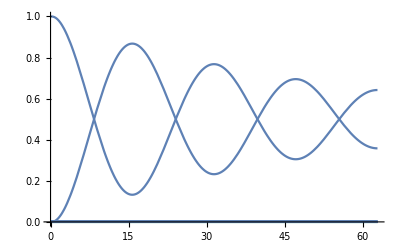

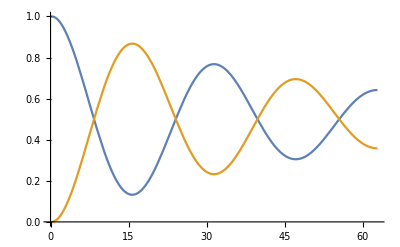

```mathematica
ωp=0.1;
r0={1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}
s=
NDSolve[{r'[t]==MatrixAsFunc[t,ωp,0].r[t],r[0]==r0},r[t],{t,0,2π/ωp}]
Plot[Evaluate[Re[r[t]]/. s],{t,0,2π/ωp},PlotRange->All]
Plot[{Evaluate[Re[r[t]]/. s][[1,1]],Evaluate[Re[r[t]]/. s][[1,4]]},{t,0,2π/ωp},PlotRange->All]
```

{1,0,0,0}

{{r[t]→InterpolatingFunction[…][t]}}

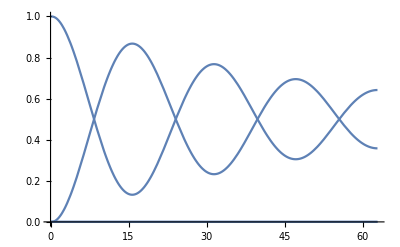

```mathematica
Matrix4D[t_,ω_,θ_]:=({{-Sin[2 t ω]^2, -1/2 ⅈ Cos[(t θ ω)/π] Sin[4 t ω], 1/2 ⅈ Cos[(t θ ω)/π] Sin[4 t ω], Cos[(t θ ω)/π]^2 Sin[2 t ω]^2}, {1/2 ⅈ Cos[(t θ ω)/π] Sin[4 t ω], -1-Cos[2 t ω]^2, -Cos[(t θ ω)/π]^2 Sin[2 t ω]^2, -1/2 ⅈ Cos[(t θ ω)/π] Sin[4 t ω]}, {-1/2 ⅈ Cos[(t θ ω)/π] Sin[4 t ω], -Cos[(t θ ω)/π]^2 Sin[2 t ω]^2, -1-Cos[2 t ω]^2, 1/2 ⅈ Cos[(t θ ω)/π] Sin[4 t ω]}, {Cos[(t θ ω)/π]^2 Sin[2 t ω]^2, 1/2 ⅈ Cos[(t θ ω)/π] Sin[4 t ω], -1/2 ⅈ Cos[(t θ ω)/π] Sin[4 t ω], -Sin[2 t ω]^2}})
ωp=0.1;
r04D={1,0,0,0}
s4D=
NDSolve[{r'[t]==Matrix4D[t,ωp,0].r[t],r[0]==r04D},r[t],{t,0,2π/ωp}]
Plot[Evaluate[Re[r[t]]/. s4D],{t,0,2π/ωp},PlotRange->All]
```

```mathematica
MatrixExp[DiagonalMatrix[Eigenvalues[Matrix4D[t,ω,0]]]t]
```

{{ⅇ^(-2 t),0,0,0},{0,ⅇ^(-2 t),0,0},{0,0,1,0},{0,0,0,1}}

{{-Sin[2 t ω]^2,-1/2 ⅈ Sin[4 t ω],1/2 ⅈ Sin[4 t ω],Sin[2 t ω]^2},{1/2 ⅈ Sin[4 t ω],-1-Cos[2 t ω]^2,-Sin[2 t ω]^2,-1/2 ⅈ Sin[4 t ω]},{-1/2 ⅈ Sin[4 t ω],-Sin[2 t ω]^2,-1-Cos[2 t ω]^2,1/2 ⅈ Sin[4 t ω]},{Sin[2 t ω]^2,1/2 ⅈ Sin[4 t ω],-1/2 ⅈ Sin[4 t ω],-Sin[2 t ω]^2}}

{{-Sin[2 t ω]^2,-1/2 ⅈ Sin[4 t ω],1/2 ⅈ Sin[4 t ω],Sin[2 t ω]^2},{1/2 ⅈ Sin[4 t ω],1/2 (-3-Cos[4 t ω]),-Sin[2 t ω]^2,-1/2 ⅈ Sin[4 t ω]},{-1/2 ⅈ Sin[4 t ω],-Sin[2 t ω]^2,1/2 (-3-Cos[4 t ω]),1/2 ⅈ Sin[4 t ω]},{Sin[2 t ω]^2,1/2 ⅈ Sin[4 t ω],-1/2 ⅈ Sin[4 t ω],-Sin[2 t ω]^2}}

{1+Sin[2 t ω]^2 Sinh[t] (-Cosh[t]+Sinh[t]),1/2 ⅈ ⅇ^-t Sin[4 t ω] Sinh[t],-1/2 ⅈ ⅇ^-t Sin[4 t ω] Sinh[t],ⅇ^-t Sin[2 t ω]^2 Sinh[t]}

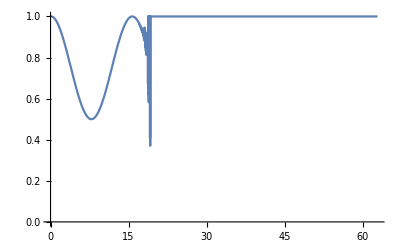

```mathematica
Matrix4D[t,ω,0]
ωp=0.1;
Transpose[Eigenvectors[Matrix4D[t,ω,0]]].DiagonalMatrix[Eigenvalues[Matrix4D[t,ω,0]]].Inverse[Transpose[Eigenvectors[Matrix4D[t,ω,0]]]]//FullSimplify
Transpose[Eigenvectors[Matrix4D[t,ω,0]]].{{ⅇ^(-2 t),0,0,0},{0,ⅇ^(-2 t),0,0},{0,0,1,0},{0,0,0,1}}.Inverse[Transpose[Eigenvectors[Matrix4D[t,ω,0]]]].{1,0,0,0}//FullSimplify
Plot[1+Sin[2 t ωp]^2 Sinh[t] (-Cosh[t]+Sinh[t]),{t,0,2π/ωp},PlotRange->{0,1}]
```

```mathematica
Transpose[Eigenvectors[Matrix4D[t,ω,0]]]//FullSimplify
Inverse[Transpose[Eigenvectors[Matrix4D[t,ω,0]]]].D[Transpose[Eigenvectors[Matrix4D[t,ω,0]]],t]//FullSimplify//MatrixForm

DiagonalMatrix[Eigenvalues[Matrix4D[t,ω,0]]]+Inverse[Transpose[Eigenvectors[Matrix4D[t,ω,0]]]].D[Transpose[Eigenvectors[Matrix4D[t,ω,0]]],t]//FullSimplify//MatrixForm
```

{{-1,0,1,2 ⅈ Cot[2 t ω]},{2 ⅈ Cot[2 t ω],1,0,-1},{0,1,0,1},{1,0,1,0}}

(-ω Cot[t ω]+ω Tan[t ω] | 0 | 0 | 2 ⅈ ω
-2 ⅈ ω | 0 | 0 | 2 ω Cot[2 t ω]
2 ω Cot[2 t ω] | 0 | 0 | -2 ⅈ ω
2 ⅈ ω | 0 | 0 | -2 ω Cot[2 t ω])

(-2-ω Cot[t ω]+ω Tan[t ω] | 0 | 0 | 2 ⅈ ω
-2 ⅈ ω | -2 | 0 | 2 ω Cot[2 t ω]
2 ω Cot[2 t ω] | 0 | 0 | -2 ⅈ ω
2 ⅈ ω | 0 | 0 | -2 ω Cot[2 t ω])

{1,0,0,0}

{{r[t]→InterpolatingFunction[…][t]}}

-Graphics-

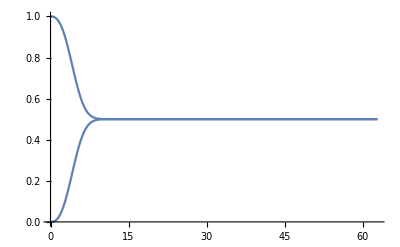

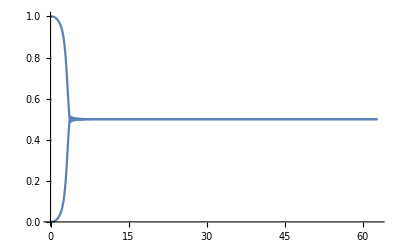

```mathematica
Matrix4D[t_,ω_,θ_]:=({{-Sin[2 t ω]^2, -1/2 ⅈ Cos[(t θ ω)/π] Sin[4 t ω], 1/2 ⅈ Cos[(t θ ω)/π] Sin[4 t ω], Cos[(t θ ω)/π]^2 Sin[2 t ω]^2}, {1/2 ⅈ Cos[(t θ ω)/π] Sin[4 t ω], -1-Cos[2 t ω]^2, -Cos[(t θ ω)/π]^2 Sin[2 t ω]^2, -1/2 ⅈ Cos[(t θ ω)/π] Sin[4 t ω]}, {-1/2 ⅈ Cos[(t θ ω)/π] Sin[4 t ω], -Cos[(t θ ω)/π]^2 Sin[2 t ω]^2, -1-Cos[2 t ω]^2, 1/2 ⅈ Cos[(t θ ω)/π] Sin[4 t ω]}, {Cos[(t θ ω)/π]^2 Sin[2 t ω]^2, 1/2 ⅈ Cos[(t θ ω)/π] Sin[4 t ω], -1/2 ⅈ Cos[(t θ ω)/π] Sin[4 t ω], -Sin[2 t ω]^2}})
ωp=0.1;
r04D={1,0,0,0}
s4D=
NDSolve[{r'[t]==Matrix4D[t,ωp,0].r[t],r[0]==r04D},r[t],{t,0,2π/ωp}]
Plot[Evaluate[Re[r[t]]/. s4D],{t,0,2π/ωp},PlotRange->All]
(*Integrate[Matrix4D[tp,ω,0],{tp,0,t}]//FullSimplify//MatrixForm*)
Matrix4DInteg[t_,ω_]:=({{(-4 t ω+Sin[4 t ω])/(8 ω), -(ⅈ Sin[2 t ω]^2)/(4 ω), (ⅈ Sin[2 t ω]^2)/(4 ω), t/2-Sin[4 t ω]/(8 ω)}, {(ⅈ Sin[2 t ω]^2)/(4 ω), -(12 t ω+Sin[4 t ω])/(8 ω), (-4 t ω+Sin[4 t ω])/(8 ω), -(ⅈ Sin[2 t ω]^2)/(4 ω)}, {-(ⅈ Sin[2 t ω]^2)/(4 ω), (-4 t ω+Sin[4 t ω])/(8 ω), -(12 t ω+Sin[4 t ω])/(8 ω), (ⅈ Sin[2 t ω]^2)/(4 ω)}, {t/2-Sin[4 t ω]/(8 ω), (ⅈ Sin[2 t ω]^2)/(4 ω), -(ⅈ Sin[2 t ω]^2)/(4 ω), (-4 t ω+Sin[4 t ω])/(8 ω)}});
Plot[MatrixExp[Matrix4DInteg[t,ωp]].r04D,{t,0,2π/ωp},PlotRange->All]
Matrix4DInteg2[t_,ω_]:=({{(-4 t ω+Sin[4 t ω])/(8 ω), (ⅈ (8 ω (t-8 ω^2)+4 ω (t+16 ω^2) Cos[4 t ω]-3 Sin[4 t ω]))/(512 ω^4), (ⅈ (-8 t ω+64 ω^3-4 ω (t+16 ω^2) Cos[4 t ω]+3 Sin[4 t ω]))/(512 ω^4), t/2-Sin[4 t ω]/(8 ω)}, {(ⅈ (8 t ω+4 t ω Cos[4 t ω]+128 ω^3 Sin[2 t ω]^2-3 Sin[4 t ω]))/(512 ω^4), -(12 t ω+Sin[4 t ω])/(8 ω), (-4 t ω+Sin[4 t ω])/(8 ω), -(ⅈ (8 t ω+4 t ω Cos[4 t ω]+128 ω^3 Sin[2 t ω]^2-3 Sin[4 t ω]))/(512 ω^4)}, {-(ⅈ (8 t ω+4 t ω Cos[4 t ω]+128 ω^3 Sin[2 t ω]^2-3 Sin[4 t ω]))/(512 ω^4), (-4 t ω+Sin[4 t ω])/(8 ω), -(12 t ω+Sin[4 t ω])/(8 ω), (ⅈ (8 t ω+4 t ω Cos[4 t ω]+128 ω^3 Sin[2 t ω]^2-3 Sin[4 t ω]))/(512 ω^4)}, {t/2-Sin[4 t ω]/(8 ω), (ⅈ (-8 t ω+64 ω^3-4 ω (t+16 ω^2) Cos[4 t ω]+3 Sin[4 t ω]))/(512 ω^4), (ⅈ (8 ω (t-8 ω^2)+4 ω (t+16 ω^2) Cos[4 t ω]-3 Sin[4 t ω]))/(512 ω^4), (-4 t ω+Sin[4 t ω])/(8 ω)}})
Plot[MatrixExp[Matrix4DInteg2[t,ωp]].r04D,{t,0,2π/ωp},PlotRange->All]
```

```mathematica
(*1/2 Integrate[Integrate[Comm[Matrix4DInteg[t1,ω],Matrix4DInteg[t2,ω]],{t2,0,t1}],{t1,0,t}]*)
({{(-4 t ω+Sin[4 t ω])/(8 ω), -(ⅈ Sin[2 t ω]^2)/(4 ω), (ⅈ Sin[2 t ω]^2)/(4 ω), t/2-Sin[4 t ω]/(8 ω)}, {(ⅈ Sin[2 t ω]^2)/(4 ω), -(12 t ω+Sin[4 t ω])/(8 ω), (-4 t ω+Sin[4 t ω])/(8 ω), -(ⅈ Sin[2 t ω]^2)/(4 ω)}, {-(ⅈ Sin[2 t ω]^2)/(4 ω), (-4 t ω+Sin[4 t ω])/(8 ω), -(12 t ω+Sin[4 t ω])/(8 ω), (ⅈ Sin[2 t ω]^2)/(4 ω)}, {t/2-Sin[4 t ω]/(8 ω), (ⅈ Sin[2 t ω]^2)/(4 ω), -(ⅈ Sin[2 t ω]^2)/(4 ω), (-4 t ω+Sin[4 t ω])/(8 ω)}})+{{0,(ⅈ (8 t ω+4 t ω Cos[4 t ω]-3 Sin[4 t ω]))/(512 ω^4),-(ⅈ (8 t ω+4 t ω Cos[4 t ω]-3 Sin[4 t ω]))/(512 ω^4),0},{(ⅈ (8 t ω+4 t ω Cos[4 t ω]-3 Sin[4 t ω]))/(512 ω^4),0,0,-(ⅈ (8 t ω+4 t ω Cos[4 t ω]-3 Sin[4 t ω]))/(512 ω^4)},{-(ⅈ (8 t ω+4 t ω Cos[4 t ω]-3 Sin[4 t ω]))/(512 ω^4),0,0,(ⅈ (8 t ω+4 t ω Cos[4 t ω]-3 Sin[4 t ω]))/(512 ω^4)},{0,-(ⅈ (8 t ω+4 t ω Cos[4 t ω]-3 Sin[4 t ω]))/(512 ω^4),(ⅈ (8 t ω+4 t ω Cos[4 t ω]-3 Sin[4 t ω]))/(512 ω^4),0}}//FullSimplify//MatrixForm
```

((-4 t ω+Sin[4 t ω])/(8 ω) | (ⅈ (8 ω (t-8 ω^2)+4 ω (t+16 ω^2) Cos[4 t ω]-3 Sin[4 t ω]))/(512 ω^4) | (ⅈ (-8 t ω+64 ω^3-4 ω (t+16 ω^2) Cos[4 t ω]+3 Sin[4 t ω]))/(512 ω^4) | t/2-Sin[4 t ω]/(8 ω)
(ⅈ (8 t ω+4 t ω Cos[4 t ω]+128 ω^3 Sin[2 t ω]^2-3 Sin[4 t ω]))/(512 ω^4) | -(12 t ω+Sin[4 t ω])/(8 ω) | (-4 t ω+Sin[4 t ω])/(8 ω) | -(ⅈ (8 t ω+4 t ω Cos[4 t ω]+128 ω^3 Sin[2 t ω]^2-3 Sin[4 t ω]))/(512 ω^4)
-(ⅈ (8 t ω+4 t ω Cos[4 t ω]+128 ω^3 Sin[2 t ω]^2-3 Sin[4 t ω]))/(512 ω^4) | (-4 t ω+Sin[4 t ω])/(8 ω) | -(12 t ω+Sin[4 t ω])/(8 ω) | (ⅈ (8 t ω+4 t ω Cos[4 t ω]+128 ω^3 Sin[2 t ω]^2-3 Sin[4 t ω]))/(512 ω^4)
t/2-Sin[4 t ω]/(8 ω) | (ⅈ (-8 t ω+64 ω^3-4 ω (t+16 ω^2) Cos[4 t ω]+3 Sin[4 t ω]))/(512 ω^4) | (ⅈ (8 ω (t-8 ω^2)+4 ω (t+16 ω^2) Cos[4 t ω]-3 Sin[4 t ω]))/(512 ω^4) | (-4 t ω+Sin[4 t ω])/(8 ω))

```mathematica
Matrix4D[t,ω,0]//Eigenvalues
Matrix4D[t,ω,0]//FullSimplify//MatrixForm
```

{-2,-2,0,0}

(-Sin[2 t ω]^2 | -1/2 ⅈ Sin[4 t ω] | 1/2 ⅈ Sin[4 t ω] | Sin[2 t ω]^2
1/2 ⅈ Sin[4 t ω] | -1-Cos[2 t ω]^2 | -Sin[2 t ω]^2 | -1/2 ⅈ Sin[4 t ω]
-1/2 ⅈ Sin[4 t ω] | -Sin[2 t ω]^2 | -1-Cos[2 t ω]^2 | 1/2 ⅈ Sin[4 t ω]
Sin[2 t ω]^2 | 1/2 ⅈ Sin[4 t ω] | -1/2 ⅈ Sin[4 t ω] | -Sin[2 t ω]^2)

{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

{{r[t]→InterpolatingFunction[…][t]}}

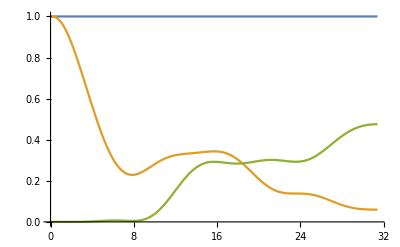

```mathematica
ωp=0.2;
r0={1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}
s=
NDSolve[{r'[t]==MatrixAsFunc[t,ωp,π/2].r[t],r[0]==r0},r[t],{t,0,2π/ωp}]
Plot[{1,Evaluate[Re[r[t]]/. s][[1,1]],Evaluate[Re[r[t]]/. s][[1,16]]},{t,0,2π/ωp},PlotRange->All]
```

{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

{{r[t]→InterpolatingFunction[{{0., 628.319}}, <>][t]}}

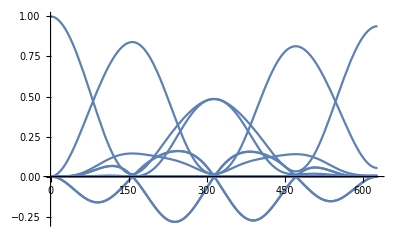

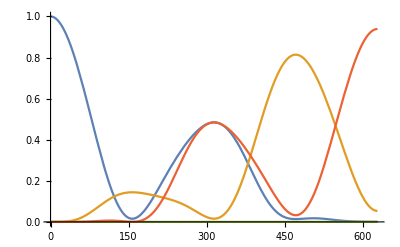

```mathematica
ωp=0.01;
r0={1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}
s=
NDSolve[{r'[t]==MatrixAsFunc[t,ωp,π/2].r[t],r[0]==r0},r[t],{t,0,2π/ωp}]
Plot[Evaluate[Re[r[t]]/. s],{t,0,2π/ωp},PlotRange->All]
Plot[{Evaluate[Re[r[t]]/. s][[1,1]],Evaluate[Re[r[t]]/. s][[1,9]],Evaluate[Re[r[t]]/. s][[1,14]],Evaluate[Re[r[t]]/. s][[1,16]]},{t,0,2π/ωp},PlotRange->All]
```

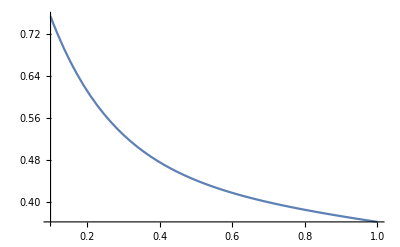

```mathematica
qGateSolve[κ_,ω_]:=Module[{s,g},
s=
NDSolve[{r'[t]==κ*MatrixAsFunc[t,ω,π/2].r[t],r[0]==Basis[16,1]},r,{t,0,2π/ω}];
Re[Evaluate[r[2π/ω]/.s][[1,16]]]
]

Plot[qGateSolve[2,ω],{ω,0.1,1}]
```

Now lets compare it with three qubit code

```mathematica
g={KroneckerProduct[PauliMatrix[3],PauliMatrix[3],IdentityMatrix[2]],KroneckerProduct[PauliMatrix[3],IdentityMatrix[2],PauliMatrix[3]]};
H=KroneckerProduct[PauliMatrix[1],PauliMatrix[1],PauliMatrix[1]];
X=KroneckerProduct[PauliMatrix[1],IdentityMatrix[2],PauliMatrix[3]];
ψ0=Basis[8,1];
θ=π/2;
V[t_,ω_]:=MatrixExp[I*(θ*ω*t)/(2π)*H].MatrixExp[I*ω*t*X];
g1[t_,ω_]:=V[t,ω].(g[[1]].ConjugateTranspose[V[t,ω]]);
g2[t_,ω_]:=V[t,ω].(g[[2]].ConjugateTranspose[V[t,ω]]);
qGateNDSolve[κ_,ω_]:=Module[{s,g},
s=
NDSolve[{ρ'[t]==κ*(g1[t,ω].ρ[t].g1[t,ω]-ρ[t])+κ*(g2[t,ω].ρ[t].g2[t,ω]-ρ[t]),ρ[0]==Outer[Times,ψ0,ψ0]},ρ,{t,0,2π/ω}];
Re[Evaluate[ρ[2π/ω]/.s][[1]][[8,8]]]
]
```

```mathematica
Transpose[{Range[0.004,1,0.02],qGateNDSolve[2,#]&/@Range[0.004,1,0.02]}]
```

Inverse::luc: Result for Inverse of badly conditioned matrix {{4.19606×10^-18-1.22457×10^-17 ⅈ,0.+0. ⅈ,-8.69895×10^-17-1.16239×10^-17 ⅈ,0.+0. ⅈ,6.17522×10^-17+1.4×10^-16 ⅈ,0.+0. ⅈ,-6.17522×10^-17+1.4×10^-16 ⅈ,0.+0. ⅈ},«6»,{-4.19606×10^-18+«24» ⅈ,«6»,0.+«1»}} may contain significant numerical errors.

Inverse::sing: Matrix {{0.341821+0.618998 ⅈ,0.+0. ⅈ,0.224441-0.670542 ⅈ,0.+0. ⅈ,0.146334+0.691799 ⅈ,0.+0. ⅈ,0.146334-0.691799 ⅈ,0.+0. ⅈ},«7»} is singular.

Inverse::luc: Result for Inverse of badly conditioned matrix {{4.19606×10^-18-1.22457×10^-17 ⅈ,0.+0. ⅈ,-8.69895×10^-17-1.16239×10^-17 ⅈ,0.+0. ⅈ,6.17522×10^-17+1.4×10^-16 ⅈ,0.+0. ⅈ,-6.17522×10^-17+1.4×10^-16 ⅈ,0.+0. ⅈ},«6»,{-4.19606×10^-18+«24» ⅈ,«6»,0.+«1»}} may contain significant numerical errors.

Inverse::sing: Matrix {{0.341821+0.618998 ⅈ,0.+0. ⅈ,0.224441-0.670542 ⅈ,0.+0. ⅈ,0.146334+0.691799 ⅈ,0.+0. ⅈ,0.146334-0.691799 ⅈ,0.+0. ⅈ},«7»} is singular.

Inverse::luc: Result for Inverse of badly conditioned matrix {{4.19606×10^-18-1.22457×10^-17 ⅈ,0.+0. ⅈ,-8.69895×10^-17-1.16239×10^-17 ⅈ,0.+0. ⅈ,6.17522×10^-17+1.4×10^-16 ⅈ,0.+0. ⅈ,-6.17522×10^-17+1.4×10^-16 ⅈ,0.+0. ⅈ},«6»,{-4.19606×10^-18+«24» ⅈ,«6»,0.+«1»}} may contain significant numerical errors.

General::stop: Further output of Inverse::luc will be suppressed during this calculation.

Inverse::sing: Matrix {{0.341821+0.618998 ⅈ,0.+0. ⅈ,0.224441-0.670542 ⅈ,0.+0. ⅈ,0.146334+0.691799 ⅈ,0.+0. ⅈ,0.146334-0.691799 ⅈ,0.+0. ⅈ},«7»} is singular.

General::stop: Further output of Inverse::sing will be suppressed during this calculation.

NDSolve::ndnum: Encountered non-numerical value for a derivative at t == 0..

ReplaceAll::reps: {NDSolve[{ρ'[t]==2 (Dot[«9»]+Times[«2»])+2 (Dot[«9»]+Times[«2»]),ρ[0]=={{1,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0}}},ρ,{t,0,74.7998}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partw: Part 8 of ρ[74.7998] does not exist.

NDSolve::mxst: Maximum number of 1701725 steps reached at the point t == 0.0272373.

InterpolatingFunction::dmval: Input value {25.7508} lies outside the range of data in the interpolating function. Extrapolation will be used.

NDSolve::ndnum: Encountered non-numerical value for a derivative at t == 0..

ReplaceAll::reps: {NDSolve[{ρ'[t]==2 (Dot[«9»]+Times[«2»])+2 (Dot[«9»]+Times[«2»]),ρ[0]=={{1,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0}}},ρ,{t,0,8.44514}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partw: Part 8 of ρ[8.44514] does not exist.

NDSolve::ndnum: Encountered non-numerical value for a derivative at t == 0..

General::stop: Further output of NDSolve::ndnum will be suppressed during this calculation.

ReplaceAll::reps: {NDSolve[{ρ'[t]==2 (Dot[«9»]+Times[«2»])+2 (Dot[«9»]+Times[«2»]),ρ[0]=={{1,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0}}},ρ,{t,0,7.10768}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Part::partw: Part 8 of ρ[7.10768] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

{{0.004,0.993558},{0.024,0.962461},{0.044,0.933128},{0.064,0.905451},{0.084,Re[ρ[74.7998]⟦8,8⟧]},{0.104,0.854655},{0.124,0.831351},{0.144,0.809332},{0.164,0.788517},{0.184,0.768834},{0.204,0.750215},{0.224,0.732594},{0.244,3.66246×10^10},{0.264,0.700122},{0.284,0.68516},{0.304,0.670981},{0.324,0.657539},{0.344,0.644791},{0.364,0.632696},{0.384,0.621217},{0.404,0.610318},{0.424,0.599965},{0.444,0.590128},{0.464,0.580776},{0.484,0.571882},{0.504,0.563421},{0.524,0.555366},{0.544,0.547696},{0.564,0.540389},{0.584,0.533425},{0.604,0.526784},{0.624,0.520449},{0.644,0.514402},{0.664,0.508628},{0.684,0.503111},{0.704,0.497837},{0.724,0.492794},{0.744,Re[ρ[8.44514]⟦8,8⟧]},{0.764,0.483347},{0.784,0.478921},{0.804,0.474678},{0.824,0.470609},{0.844,0.466705},{0.864,0.462957},{0.884,Re[ρ[7.10768]⟦8,8⟧]},{0.904,0.455893},{0.924,0.452563},{0.944,Re[ρ[6.65592]⟦8,8⟧]},{0.964,0.446271},{0.984,0.443297}}

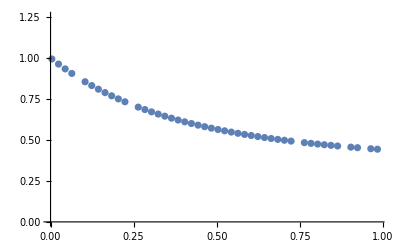

```mathematica
ListPlot[{{0.004,0.9935584327586713},{0.024,0.962460712459448},{0.044,0.9331281149964498},{0.064,0.9054507768860011},{0.10400000000000001,0.8546545879085871},{0.124,0.8313513479308707},{0.14400000000000002,0.8093315163468611},{0.164,0.7885165538981105},{0.184,0.7688341995744656},{0.20400000000000001,0.7502146653061683},{0.224,0.7325937979630538},{0.244,3.6624630544697945*^10},{0.264,0.7001216455252},{0.28400000000000003,0.6851598254860404},{0.304,0.6709809718725024},{0.324,0.6575390986916183},{0.34400000000000003,0.6447910674853616},{0.364,0.6326964801886777},{0.384,0.6212173449266705},{0.404,0.6103182359941128},{0.424,0.599965469188428},{0.444,0.5901280110314023},{0.464,0.5807762970198591},{0.484,0.5718823744826532},{0.504,0.5634205077794051},{0.524,0.5553661179800257},{0.544,0.5476962286937335},{0.5640000000000001,0.5403894084739594},{0.584,0.5334250884958707},{0.604,0.526784305251709},{0.624,0.5204489657243885},{0.644,0.514401994846228},{0.664,0.5086276478726974},{0.684,0.5031108802776454},{0.7040000000000001,0.4978373510735491},{0.724,0.4927938245023971},{0.764,0.4833469762536251},{0.784,0.47892060457222524},{0.804,0.47467810832157553},{0.8240000000000001,0.4706094361044651},{0.844,0.46670526645149957},{0.864,0.46295670807311123},{0.904,0.4558934409979708},{0.924,0.45256342273457173},{0.964,0.4462714583241168},{0.984,0.4432965808703515}}]
```

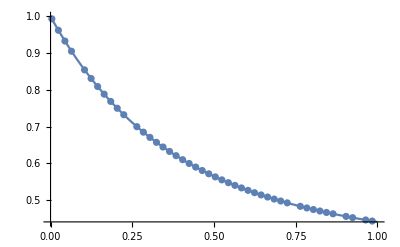

```mathematica
Show[{Plot[qGateSolve[4,ω],{ω,0,1}],ListPlot[{{0.004,0.9935584327586713},{0.024,0.962460712459448},{0.044,0.9331281149964498},{0.064,0.9054507768860011},{0.10400000000000001,0.8546545879085871},{0.124,0.8313513479308707},{0.14400000000000002,0.8093315163468611},{0.164,0.7885165538981105},{0.184,0.7688341995744656},{0.20400000000000001,0.7502146653061683},{0.224,0.7325937979630538},{0.244,3.6624630544697945*^10},{0.264,0.7001216455252},{0.28400000000000003,0.6851598254860404},{0.304,0.6709809718725024},{0.324,0.6575390986916183},{0.34400000000000003,0.6447910674853616},{0.364,0.6326964801886777},{0.384,0.6212173449266705},{0.404,0.6103182359941128},{0.424,0.599965469188428},{0.444,0.5901280110314023},{0.464,0.5807762970198591},{0.484,0.5718823744826532},{0.504,0.5634205077794051},{0.524,0.5553661179800257},{0.544,0.5476962286937335},{0.5640000000000001,0.5403894084739594},{0.584,0.5334250884958707},{0.604,0.526784305251709},{0.624,0.5204489657243885},{0.644,0.514401994846228},{0.664,0.5086276478726974},{0.684,0.5031108802776454},{0.7040000000000001,0.4978373510735491},{0.724,0.4927938245023971},{0.764,0.4833469762536251},{0.784,0.47892060457222524},{0.804,0.47467810832157553},{0.8240000000000001,0.4706094361044651},{0.844,0.46670526645149957},{0.864,0.46295670807311123},{0.904,0.4558934409979708},{0.924,0.45256342273457173},{0.964,0.4462714583241168},{0.984,0.4432965808703515}}]}]
```

```mathematica
qGateSolve[κ_,ω_]:=Module[{s,g},
s=
NDSolve[{r'[t]==κ*MatrixAsFunc[t,ω,π/2].r[t],r[0]==Basis[16,1]},r,{t,0,2π/ω}];
Re[Evaluate[r[2π/ω]/.s][[1,16]]]
]
qAvgGate[κ_,ω_]:=Module[{s,g},
s=
NDSolve[{r'[t]==κ*MatrixAsFunc[t,ω,π/2].r[t],r[0]==Basis[16,1]},r,{t,0,2π/ω}];
Re[Evaluate[r[2π/ω]/.s][[1,1]]]+Re[Evaluate[r[2π/ω]/.s][[1,16]]]
]
qanalyticalExact[κ_,ω_,θ_]:=(1+Exp[-(4π*ω)/κ]*(1-(ω*θ^2)/(κ*2π)))/2
```

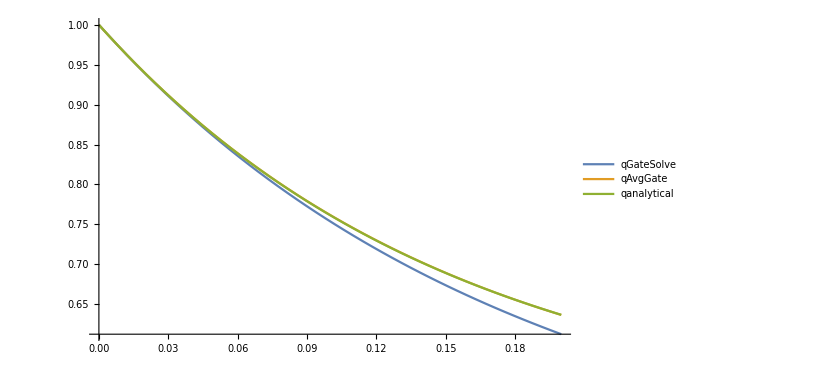

```mathematica
Plot[{qGateSolve[2,ω],qAvgGate[2,ω],qanalyticalExact[2,ω,π/2]},{ω,0,0.2},PlotLegends->{"qGateSolve","qAvgGate","qanalytical"}]
```

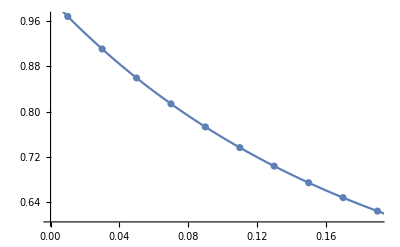

```mathematica
Show[{ListPlot[{Range[0.01,0.2,0.02],{0.9685353337161209,0.9108573791072314,0.8594742984760221,0.8136341395797559,0.7726803633675295,0.7360404826951322,0.7032118040121552,0.673756392207741,0.6472872739116545,0.6234658897618709}}//Transpose],Plot[qGateSolve[2,ω],{ω,0,0.2}]}]
```

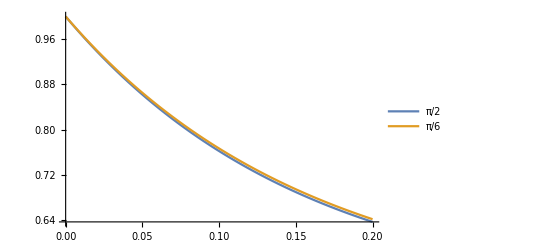

```mathematica
qGateSolveθ[κ_,ω_,θ_]:=Module[{s,g},
s=
NDSolve[{r'[t]==κ*MatrixAsFunc[t,ω,θ].r[t],r[0]==Basis[16,1]},r,{t,0,2π/ω}];
Re[Evaluate[r[2π/ω]/.s][[1,1]]]+Re[Evaluate[r[2π/ω]/.s][[1,16]]]
]
qGateSolveθHρH[κ_,ω_,θ_]:=Module[{s,g},
s=
NDSolve[{r'[t]==κ*MatrixAsFunc[t,ω,θ].r[t],r[0]==Basis[16,1]},r,{t,0,2π/ω}];
Re[Evaluate[r[2π/ω]/.s][[1,16]]]
]
Plot[{qGateSolveθ[2,ω,π/2],qGateSolveθ[2,ω,π/6]},{ω,0,0.2},PlotLegends->{"π/2","π/6"}]
```